```mathematica
ClearAll["Global`*"]
```

### Pauli Matrices and Gell-Mann Matrices

Pauli Matrices

```mathematica
Subscript[σ, x] = ({{0, 1}, {1, 0}}) ;
```

```mathematica
Subscript[σ, y] = ({{0, -ⅈ}, {ⅈ, 0}});
```

```mathematica
Subscript[σ, z] = ({{1, 0}, {0, -1}});
```

```mathematica
Subscript[σ, I] = ({{1, 0}, {0, 1}});
```

```mathematica
SubPlus[σ] =MatrixForm[ 1/2*(Subscript[σ, x] + ⅈ*Subscript[σ, y])];
```

```mathematica
SubMinus[σ] =MatrixForm[1/2*(Subscript[σ, x] - ⅈ*Subscript[σ, y])];
```

Gell-Mann Matrices

```mathematica
Subscript[Σ, x] = ({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}}) ;
Subscript[Σ, y] = ({{0, -ⅈ, 0}, {ⅈ, 0, -ⅈ}, {0, ⅈ, 0}});
Subscript[Σ, z] =({{1, 0, 0}, {0, 0, 0}, {0, 0, -1}});
Subscript[Σ, I] = ({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}});
```

```mathematica
SubPlus[Σ] = MatrixForm[1/2*(Subscript[Σ, x] + ⅈ*Subscript[Σ, y])];
```

```mathematica
SubMinus[Σ] = MatrixForm[1/2*(Subscript[Σ, x] - ⅈ*Subscript[Σ, y])];
```

### Qubit and Qutrit Representation

General representation of a qubit- There are two energy states in a qubit and they can be described by two column vectors.

-Graphics-

```mathematica
Subscript[z, 0]=Transpose[{{0,1}}];
Subscript[z, 1]=Transpose[{{1,0}}];
```

General representation of a qutrit- There are three energy states in a qutrit and they can be described by three column vectors.

-Graphics-

```mathematica
Subscript[Z, 0]=Transpose[{{0,0,1}}];
Subscript[Z, 1]=Transpose[{{0,1,0}}];
Subscript[Z, 2]=Transpose[{{1,0,0}}];
```

## Quantum Thermal Transistor by Malavazi et al.

-Graphics-

### Extended Pauli matrices and Gell-Mann matrices for the system ‘S’

```mathematica
Subscript[σ, z L]=KroneckerProduct[Subscript[σ, z],Subscript[Σ, I],Subscript[σ, I]] ;
Subscript[σ, y L]=KroneckerProduct[Subscript[σ, y],Subscript[Σ, I],Subscript[σ, I]] ;
Subscript[σ, x L]=KroneckerProduct[Subscript[σ, x],Subscript[Σ, I],Subscript[σ, I]] ;
Subscript[σ, z M]=KroneckerProduct[Subscript[σ, I],Subscript[Σ, z],Subscript[σ, I]] ;
Subscript[σ, y M]=KroneckerProduct[Subscript[σ, I],Subscript[Σ, y],Subscript[σ, I]] ;
Subscript[σ, x M]=KroneckerProduct[Subscript[σ, I],Subscript[Σ, x],Subscript[σ, I]] ;
Subscript[σ, z R]=KroneckerProduct[Subscript[σ, I],Subscript[Σ, I],Subscript[σ, z]] ;
Subscript[σ, y R]=KroneckerProduct[Subscript[σ, I],Subscript[Σ, I],Subscript[σ, y]] ;
Subscript[σ, x R]=KroneckerProduct[Subscript[σ, I],Subscript[Σ, I],Subscript[σ, x]] ;
```

### System Hamiltonian

local free Hamiltonians

```mathematica
Subscript[H, L]=ℏ*Subscript[ω, L]*Subscript[z, 1].Subscript[z, 1] ᵀ;
```

```mathematica
Subscript[H, R]=ℏ*Subscript[ω, R]*Subscript[z, 1].Subscript[z, 1] ᵀ;
```

```mathematica
Subscript[H, M]=ℏ*Subscript[ω, M]*Subscript[Z, 1].Subscript[Z, 1] ᵀ+(2*ℏ*Subscript[ω, M])*Subscript[Z, 2].Subscript[Z, 2] ᵀ;
```

interaction Hamiltonian

```mathematica
Subscript[χ, L]=(Subscript[Z, 1].Subscript[Z, 1] ᵀ-Subscript[Z, 0].Subscript[Z, 0] ᵀ)+(Subscript[Z, 2].Subscript[Z, 2] ᵀ-Subscript[Z, 0].Subscript[Z, 0] ᵀ);
```

```mathematica
Subscript[χ, R]=(Subscript[Z, 1].Subscript[Z, 1] ᵀ-Subscript[Z, 0].Subscript[Z, 0] ᵀ)+(Subscript[Z, 2].Subscript[Z, 2] ᵀ-Subscript[Z, 0].Subscript[Z, 0] ᵀ);
```

```mathematica
V=ℏ*Subscript[g, LM]*KroneckerProduct[Subscript[σ, z],Subscript[χ, L],Subscript[σ, I]]+ℏ*Subscript[g, MR]*KroneckerProduct[Subscript[σ, I],Subscript[χ, R],Subscript[σ, z]];
```

total Hamiltonian

```mathematica
Subscript[H, S]=KroneckerProduct[Subscript[H, L],Subscript[Σ, I],Subscript[σ, I]]+KroneckerProduct[Subscript[σ, I],Subscript[Σ, I],Subscript[H, R]]+KroneckerProduct[Subscript[σ, I],Subscript[H, M],Subscript[σ, I]]+V;
```

12-energy states in H_S

```mathematica
{Eval,Evec}=Eigensystem[Subscript[H, S]];
```

```mathematica
list1=Partition[Riffle[Eval,Evec],2];
list2=Sort[list1,OrderedQ[{#1[[2]],#2[[2]]}]&];
list2//MatrixForm
```

(2 ℏ (g_LM+g_MR) | {0,0,0,0,0,0,0,0,0,0,0,1}
ℏ (2 g_LM-2 g_MR+ω_R) | {0,0,0,0,0,0,0,0,0,0,1,0}
ℏ (-g_LM-g_MR+ω_M) | {0,0,0,0,0,0,0,0,0,1,0,0}
ℏ (-g_LM+g_MR+ω_M+ω_R) | {0,0,0,0,0,0,0,0,1,0,0,0}
ℏ (-g_LM-g_MR+2 ω_M) | {0,0,0,0,0,0,0,1,0,0,0,0}
ℏ (-g_LM+g_MR+2 ω_M+ω_R) | {0,0,0,0,0,0,1,0,0,0,0,0}
ℏ (-2 g_LM+2 g_MR+ω_L) | {0,0,0,0,0,1,0,0,0,0,0,0}
ℏ (-2 g_LM-2 g_MR+ω_L+ω_R) | {0,0,0,0,1,0,0,0,0,0,0,0}
ℏ (g_LM-g_MR+ω_L+ω_M) | {0,0,0,1,0,0,0,0,0,0,0,0}
ℏ (g_LM+g_MR+ω_L+ω_M+ω_R) | {0,0,1,0,0,0,0,0,0,0,0,0}
ℏ (g_LM-g_MR+ω_L+2 ω_M) | {0,1,0,0,0,0,0,0,0,0,0,0}
ℏ (g_LM+g_MR+ω_L+2 ω_M+ω_R) | {1,0,0,0,0,0,0,0,0,0,0,0})

Total system states using tensor product of individual states

```mathematica
Subscript[S, i_,j_,k_]:=Flatten[KroneckerProduct[Subscript[z, i],Subscript[Z, j],Subscript[z, k]]]
Subscript[E, i_,j_,k_]:=First[Select[list1,#[[2]]==Subscript[S, i,j,k]&]][[1]]
```

```mathematica
Subscript[S, 0,0,0]
```

{0,0,0,0,0,0,0,0,0,0,0,1}

```mathematica
Subscript[S, 0,0,1]
```

{0,0,0,0,0,0,0,0,0,0,1,0}

```mathematica
Subscript[S, 0,1,0]
```

{0,0,0,0,0,0,0,0,0,1,0,0}

```mathematica
Subscript[S, 0,1,1]
```

{0,0,0,0,0,0,0,0,1,0,0,0}

```mathematica
Subscript[S, 0,2,0]
```

{0,0,0,0,0,0,0,1,0,0,0,0}

```mathematica
Subscript[S, 0,2,1]
```

{0,0,0,0,0,0,1,0,0,0,0,0}

```mathematica
Subscript[S, 1,0,0]
```

{0,0,0,0,0,1,0,0,0,0,0,0}

```mathematica
Subscript[S, 1,0,1]
```

{0,0,0,0,1,0,0,0,0,0,0,0}

```mathematica
Subscript[S, 1,1,0]
```

{0,0,0,1,0,0,0,0,0,0,0,0}

```mathematica
Subscript[S, 1,1,1]
```

{0,0,1,0,0,0,0,0,0,0,0,0}

```mathematica
Subscript[S, 1,2,0]
```

{0,1,0,0,0,0,0,0,0,0,0,0}

```mathematica
Subscript[S, 1,2,1]
```

{1,0,0,0,0,0,0,0,0,0,0,0}

Eigenstates of the system

```mathematica
Subscript[λ, 1]=Transpose[{{1,0,0,0,0,0,0,0,0,0,0,0}}];
Subscript[λ, 2]=Transpose[{{0,1,0,0,0,0,0,0,0,0,0,0}}];
Subscript[λ, 3]=Transpose[{{0,0,1,0,0,0,0,0,0,0,0,0}}];
Subscript[λ, 4]=Transpose[{{0,0,0,1,0,0,0,0,0,0,0,0}}];
Subscript[λ, 5]=Transpose[{{0,0,0,0,1,0,0,0,0,0,0,0}}];
Subscript[λ, 6]=Transpose[{{0,0,0,0,0,1,0,0,0,0,0,0}}];
Subscript[λ, 7]=Transpose[{{0,0,0,0,0,0,1,0,0,0,0,0}}];
Subscript[λ, 8]=Transpose[{{0,0,0,0,0,0,0,1,0,0,0,0}}];
Subscript[λ, 9]=Transpose[{{0,0,0,0,0,0,0,0,1,0,0,0}}];
Subscript[λ, 10]=Transpose[{{0,0,0,0,0,0,0,0,0,1,0,0}}];
Subscript[λ, 11]=Transpose[{{0,0,0,0,0,0,0,0,0,0,1,0}}];
Subscript[λ, 12]=Transpose[{{0,0,0,0,0,0,0,0,0,0,0,1}}];
```

Eigenvalues in matrix form

```mathematica
HsEVal =Reverse[Flatten[Table[Subscript[E, i,j,r],{i,0,1},{j,0,2},{r,0,1}]]]//MatrixForm
```

(ℏ (g_LM+g_MR+ω_L+2 ω_M+ω_R)
ℏ (g_LM-g_MR+ω_L+2 ω_M)
ℏ (g_LM+g_MR+ω_L+ω_M+ω_R)
ℏ (g_LM-g_MR+ω_L+ω_M)
ℏ (-2 g_LM-2 g_MR+ω_L+ω_R)
ℏ (-2 g_LM+2 g_MR+ω_L)
ℏ (-g_LM+g_MR+2 ω_M+ω_R)
ℏ (-g_LM-g_MR+2 ω_M)
ℏ (-g_LM+g_MR+ω_M+ω_R)
ℏ (-g_LM-g_MR+ω_M)
ℏ (2 g_LM-2 g_MR+ω_R)
2 ℏ (g_LM+g_MR))

### Jump Operators

For qubits (same as x-Pauli matrix)

```mathematica
Subscript[S, L]=Subscript[z, 1].Subscript[z, 0] ᵀ+Subscript[z, 0].Subscript[z, 1] ᵀ;
```

```mathematica
Subscript[𝕊, L]=KroneckerProduct[Subscript[S, L],Subscript[Σ, I],Subscript[σ, I]];
```

```mathematica
Subscript[S, R]=Subscript[z, 1].Subscript[z, 0] ᵀ+Subscript[z, 0].Subscript[z, 1] ᵀ;
```

```mathematica
Subscript[𝕊, R]=KroneckerProduct[Subscript[σ, I],Subscript[Σ, I],Subscript[S, R]];
```

For qutrit ( similar to x-Gell-Mann matrix )

```mathematica
Subscript[S, M]=(Subscript[Z, 1].Subscript[Z, 0] ᵀ+Subscript[Z, 0].Subscript[Z, 1] ᵀ)+(Subscript[Z, 2].Subscript[Z, 1] ᵀ+Subscript[Z, 1].Subscript[Z, 2] ᵀ);
```

```mathematica
Subscript[𝕊, M]=KroneckerProduct[Subscript[σ, I],Subscript[S, M],Subscript[σ, I]];
```

Projection Operators

```mathematica
Subscript[πMatrix, i_] := Subscript[λ, i].Subscript[λ, i] ᵀ
```

Jump Operator

```mathematica
Subscript[AMatrix, α_,Subscript[ω, j_,i_]]:= Subscript[πMatrix, i].Subscript[𝕊, α].Subscript[πMatrix, j]
```

### Density Matrix

```mathematica
ρMatrix[t]=Table[Subscript[ρ, i,j][t],{i,1,12},{j,1,12}];
MatrixForm[%]
```

(ρ_(1,1)[t] | ρ_(1,2)[t] | ρ_(1,3)[t] | ρ_(1,4)[t] | ρ_(1,5)[t] | ρ_(1,6)[t] | ρ_(1,7)[t] | ρ_(1,8)[t] | ρ_(1,9)[t] | ρ_(1,10)[t] | ρ_(1,11)[t] | ρ_(1,12)[t]
ρ_(2,1)[t] | ρ_(2,2)[t] | ρ_(2,3)[t] | ρ_(2,4)[t] | ρ_(2,5)[t] | ρ_(2,6)[t] | ρ_(2,7)[t] | ρ_(2,8)[t] | ρ_(2,9)[t] | ρ_(2,10)[t] | ρ_(2,11)[t] | ρ_(2,12)[t]
ρ_(3,1)[t] | ρ_(3,2)[t] | ρ_(3,3)[t] | ρ_(3,4)[t] | ρ_(3,5)[t] | ρ_(3,6)[t] | ρ_(3,7)[t] | ρ_(3,8)[t] | ρ_(3,9)[t] | ρ_(3,10)[t] | ρ_(3,11)[t] | ρ_(3,12)[t]
ρ_(4,1)[t] | ρ_(4,2)[t] | ρ_(4,3)[t] | ρ_(4,4)[t] | ρ_(4,5)[t] | ρ_(4,6)[t] | ρ_(4,7)[t] | ρ_(4,8)[t] | ρ_(4,9)[t] | ρ_(4,10)[t] | ρ_(4,11)[t] | ρ_(4,12)[t]
ρ_(5,1)[t] | ρ_(5,2)[t] | ρ_(5,3)[t] | ρ_(5,4)[t] | ρ_(5,5)[t] | ρ_(5,6)[t] | ρ_(5,7)[t] | ρ_(5,8)[t] | ρ_(5,9)[t] | ρ_(5,10)[t] | ρ_(5,11)[t] | ρ_(5,12)[t]
ρ_(6,1)[t] | ρ_(6,2)[t] | ρ_(6,3)[t] | ρ_(6,4)[t] | ρ_(6,5)[t] | ρ_(6,6)[t] | ρ_(6,7)[t] | ρ_(6,8)[t] | ρ_(6,9)[t] | ρ_(6,10)[t] | ρ_(6,11)[t] | ρ_(6,12)[t]
ρ_(7,1)[t] | ρ_(7,2)[t] | ρ_(7,3)[t] | ρ_(7,4)[t] | ρ_(7,5)[t] | ρ_(7,6)[t] | ρ_(7,7)[t] | ρ_(7,8)[t] | ρ_(7,9)[t] | ρ_(7,10)[t] | ρ_(7,11)[t] | ρ_(7,12)[t]
ρ_(8,1)[t] | ρ_(8,2)[t] | ρ_(8,3)[t] | ρ_(8,4)[t] | ρ_(8,5)[t] | ρ_(8,6)[t] | ρ_(8,7)[t] | ρ_(8,8)[t] | ρ_(8,9)[t] | ρ_(8,10)[t] | ρ_(8,11)[t] | ρ_(8,12)[t]
ρ_(9,1)[t] | ρ_(9,2)[t] | ρ_(9,3)[t] | ρ_(9,4)[t] | ρ_(9,5)[t] | ρ_(9,6)[t] | ρ_(9,7)[t] | ρ_(9,8)[t] | ρ_(9,9)[t] | ρ_(9,10)[t] | ρ_(9,11)[t] | ρ_(9,12)[t]
ρ_(10,1)[t] | ρ_(10,2)[t] | ρ_(10,3)[t] | ρ_(10,4)[t] | ρ_(10,5)[t] | ρ_(10,6)[t] | ρ_(10,7)[t] | ρ_(10,8)[t] | ρ_(10,9)[t] | ρ_(10,10)[t] | ρ_(10,11)[t] | ρ_(10,12)[t]
ρ_(11,1)[t] | ρ_(11,2)[t] | ρ_(11,3)[t] | ρ_(11,4)[t] | ρ_(11,5)[t] | ρ_(11,6)[t] | ρ_(11,7)[t] | ρ_(11,8)[t] | ρ_(11,9)[t] | ρ_(11,10)[t] | ρ_(11,11)[t] | ρ_(11,12)[t]
ρ_(12,1)[t] | ρ_(12,2)[t] | ρ_(12,3)[t] | ρ_(12,4)[t] | ρ_(12,5)[t] | ρ_(12,6)[t] | ρ_(12,7)[t] | ρ_(12,8)[t] | ρ_(12,9)[t] | ρ_(12,10)[t] | ρ_(12,11)[t] | ρ_(12,12)[t])

### Possible Transition Frequencies

```mathematica
ωMatrix={Flatten[Table[Subscript[ω, i,j],{i,1,12},{j,i+1,12}]]}
```

{{ω_(1,2),ω_(1,3),ω_(1,4),ω_(1,5),ω_(1,6),ω_(1,7),ω_(1,8),ω_(1,9),ω_(1,10),ω_(1,11),ω_(1,12),ω_(2,3),ω_(2,4),ω_(2,5),ω_(2,6),ω_(2,7),ω_(2,8),ω_(2,9),ω_(2,10),ω_(2,11),ω_(2,12),ω_(3,4),ω_(3,5),ω_(3,6),ω_(3,7),ω_(3,8),ω_(3,9),ω_(3,10),ω_(3,11),ω_(3,12),ω_(4,5),ω_(4,6),ω_(4,7),ω_(4,8),ω_(4,9),ω_(4,10),ω_(4,11),ω_(4,12),ω_(5,6),ω_(5,7),ω_(5,8),ω_(5,9),ω_(5,10),ω_(5,11),ω_(5,12),ω_(6,7),ω_(6,8),ω_(6,9),ω_(6,10),ω_(6,11),ω_(6,12),ω_(7,8),ω_(7,9),ω_(7,10),ω_(7,11),ω_(7,12),ω_(8,9),ω_(8,10),ω_(8,11),ω_(8,12),ω_(9,10),ω_(9,11),ω_(9,12),ω_(10,11),ω_(10,12),ω_(11,12)}}

```mathematica
Length[Flatten[ωMatrix]]
```

66

```mathematica
ωVals=Flatten[Simplify[Table[(HsEVal[[1,i]]-HsEVal[[1,j]])/ℏ,{i,1,12},{j,i+1,12}]]];
```

### Lindblad Super Operator

```mathematica
Subscript[ℒ, P_]:=Subscript[ℒ, P]=∑_(γ=1)^66 (Subscript[𝒥, P][Part[ωMatrix,1,γ]](1+Subscript[n, P][Part[ωMatrix,1,γ]])(Subscript[AMatrix, P,Part[ωMatrix,1,γ]].ρMatrix[t].Subscript[AMatrix, P,Part[ωMatrix,1,γ]] ᵀ-1/2 Subscript[AMatrix, P,Part[ωMatrix,1,γ]] ᵀ.Subscript[AMatrix, P,Part[ωMatrix,1,γ]].ρMatrix[t]-1/2 ρMatrix[t].Subscript[AMatrix, P,Part[ωMatrix,1,γ]] ᵀ.Subscript[AMatrix, P,Part[ωMatrix,1,γ]])+(Subscript[𝒥, P][Part[ωMatrix,1,γ]] Subscript[n, P][Part[ωMatrix,1,γ]](Subscript[AMatrix, P,Part[ωMatrix,1,γ]] ᵀ.ρMatrix[t].Subscript[AMatrix, P,Part[ωMatrix,1,γ]]-1/2 Subscript[AMatrix, P,Part[ωMatrix,1,γ]].Subscript[AMatrix, P,Part[ωMatrix,1,γ]] ᵀ.ρMatrix[t]-1/2 ρMatrix[t].Subscript[AMatrix, P,Part[ωMatrix,1,γ]].Subscript[AMatrix, P,Part[ωMatrix,1,γ]] ᵀ)));
```

### Master Equation

```mathematica
dρ=MatrixForm[Subscript[ℒ, L]+Subscript[ℒ, M]+Subscript[ℒ, R]-(ⅈ/ℏ(Subscript[H, S].ρMatrix[t]-ρMatrix[t].Subscript[H, S]))]//.{-Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] +(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>Subscript[Γ, P,j,i],Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] -(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>-Subscript[Γ, P,j,i]};
```

```mathematica
MatrixForm[%]
```

```mathematica
dρ[[1,1]][[1]]
```

-Γ_(L,1,7)-Γ_(M,1,3)-Γ_(R,1,2)

```mathematica
dρ[[1,2]][[2]]
```

-Γ_(L,2,8)-Γ_(M,2,4)+Γ_(R,1,2)

```mathematica
dρ[[1,3]][[3]]
```

-Γ_(L,3,9)+Γ_(M,1,3)-Γ_(M,3,5)-Γ_(R,3,4)

```mathematica
dρ[[1,4]][[4]]
```

-Γ_(L,4,10)+Γ_(M,2,4)-Γ_(M,4,6)+Γ_(R,3,4)

```mathematica
dρ[[1,5]][[5]]
```

-Γ_(L,5,11)+Γ_(M,3,5)-Γ_(R,5,6)

```mathematica
dρ[[1,6]][[6]]
```

-Γ_(L,6,12)+Γ_(M,4,6)+Γ_(R,5,6)

```mathematica
dρ[[1,7]][[7]]
```

Γ_(L,1,7)-Γ_(M,7,9)-Γ_(R,7,8)

```mathematica
dρ[[1,8]][[8]]
```

Γ_(L,2,8)-Γ_(M,8,10)+Γ_(R,7,8)

```mathematica
dρ[[1,9]][[9]]
```

Γ_(L,3,9)+Γ_(M,7,9)-Γ_(M,9,11)-Γ_(R,9,10)

```mathematica
dρ[[1,10]][[10]]
```

Γ_(L,4,10)+Γ_(M,8,10)-Γ_(M,10,12)+Γ_(R,9,10)

```mathematica
dρ[[1,11]][[11]]
```

Γ_(L,5,11)+Γ_(M,9,11)-Γ_(R,11,12)

```mathematica
dρ[[1,12]][[12]]
```

Γ_(L,6,12)+Γ_(M,10,12)+Γ_(R,11,12)

#### Thermal Energy Flows

```mathematica
HsMatrix=DiagonalMatrix[ℏ{Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3],Subscript[ω, 4],Subscript[ω, 5],Subscript[ω, 6],Subscript[ω, 7],Subscript[ω, 8],Subscript[ω, 9],Subscript[ω, 10],Subscript[ω, 11],Subscript[ω, 12]}]
```

{{ℏ ω_1,0,0,0,0,0,0,0,0,0,0,0},{0,ℏ ω_2,0,0,0,0,0,0,0,0,0,0},{0,0,ℏ ω_3,0,0,0,0,0,0,0,0,0},{0,0,0,ℏ ω_4,0,0,0,0,0,0,0,0},{0,0,0,0,ℏ ω_5,0,0,0,0,0,0,0},{0,0,0,0,0,ℏ ω_6,0,0,0,0,0,0},{0,0,0,0,0,0,ℏ ω_7,0,0,0,0,0},{0,0,0,0,0,0,0,ℏ ω_8,0,0,0,0},{0,0,0,0,0,0,0,0,ℏ ω_9,0,0,0},{0,0,0,0,0,0,0,0,0,ℏ ω_10,0,0},{0,0,0,0,0,0,0,0,0,0,ℏ ω_11,0},{0,0,0,0,0,0,0,0,0,0,0,ℏ ω_12}}

```mathematica
Subscript[J, P_]:=Subscript[J, P]=Tr[Subscript[ℒ, P].HsMatrix]//.{-Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] +(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>Subscript[Γ, Q,j,i],Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] -(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>-Subscript[Γ, Q,j,i]};
```

```mathematica
Subscript[J, L]
```

-ℏ ω_1 Γ_(L,1,7)+ℏ ω_7 Γ_(L,1,7)-ℏ ω_2 Γ_(L,2,8)+ℏ ω_8 Γ_(L,2,8)-ℏ ω_3 Γ_(L,3,9)+ℏ ω_9 Γ_(L,3,9)-ℏ ω_4 Γ_(L,4,10)+ℏ ω_10 Γ_(L,4,10)-ℏ ω_5 Γ_(L,5,11)+ℏ ω_11 Γ_(L,5,11)-ℏ ω_6 Γ_(L,6,12)+ℏ ω_12 Γ_(L,6,12)

```mathematica
Subscript[J, M]
```

-ℏ ω_1 Γ_(M,1,3)-ℏ ω_2 Γ_(M,2,4)+ℏ ω_3 (Γ_(M,1,3)-Γ_(M,3,5))+ℏ ω_5 Γ_(M,3,5)+ℏ ω_4 (Γ_(M,2,4)-Γ_(M,4,6))+ℏ ω_6 Γ_(M,4,6)-ℏ ω_7 Γ_(M,7,9)-ℏ ω_8 Γ_(M,8,10)+ℏ ω_9 (Γ_(M,7,9)-Γ_(M,9,11))+ℏ ω_11 Γ_(M,9,11)+ℏ ω_10 (Γ_(M,8,10)-Γ_(M,10,12))+ℏ ω_12 Γ_(M,10,12)

```mathematica
Subscript[J, R]
```

-ℏ ω_1 Γ_(R,1,2)+ℏ ω_2 Γ_(R,1,2)-ℏ ω_3 Γ_(R,3,4)+ℏ ω_4 Γ_(R,3,4)-ℏ ω_5 Γ_(R,5,6)+ℏ ω_6 Γ_(R,5,6)-ℏ ω_7 Γ_(R,7,8)+ℏ ω_8 Γ_(R,7,8)-ℏ ω_9 Γ_(R,9,10)+ℏ ω_10 Γ_(R,9,10)-ℏ ω_11 Γ_(R,11,12)+ℏ ω_12 Γ_(R,11,12)

## Simulations

#### Bose - Einstein Distribution

```mathematica
NBEassum=Subscript[n, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

#### Bath Spectral Density

```mathematica
Jassum=Subscript[𝒥, P_][ω_]-> Subscript[μ, P]*Subscript[μ, P]*ω*ⅇ^((-Abs[ω])/Subscript[κ, P]);
```

#### Stationary State Solutions of master equation

```mathematica
RHS=Subscript[ℒ, L]+Subscript[ℒ, M]+Subscript[ℒ, R]-(ⅈ/ℏ(Subscript[H, S].ρMatrix[t]-ρMatrix[t].Subscript[H, S]));
```

```mathematica
LHS=D[ρMatrix[t], t];
```

```mathematica
sol=Flatten[Solve[LHS==RHS,Flatten[Table[Subscript[ρ, i,j]'[t],{i,1,12},{j,1,12}]]]/.Rule->Equal];
```

Separate diagonal and off diagonal equations,

```mathematica
soldiag=sol[[1;; ;;13]];
soloffdiag=Delete[sol,Table[{1+13i},{i,0,11}]];
```

Off diagonal Solutions

```mathematica
Flatten[{soloffdiag/.{Subscript[ρ, i_,j_]'[t]-> 0,Subscript[ρ, i_,j_][t]-> Subscript[ρ, i,j]}}];
soloffdiagstat=Solve[%,DeleteCases[Flatten[Table[Subscript[ρ, i,j]-i,j Subscript[ρ, i,j],{i,1,12},{j,1,12}]],0]]
```

{{ρ_(1,2)→0,ρ_(1,3)→0,ρ_(1,4)→0,ρ_(1,5)→0,ρ_(1,6)→0,ρ_(1,7)→0,ρ_(1,8)→0,ρ_(1,9)→0,ρ_(1,10)→0,ρ_(1,11)→0,ρ_(1,12)→0,ρ_(2,1)→0,ρ_(2,3)→0,ρ_(2,4)→0,ρ_(2,5)→0,ρ_(2,6)→0,ρ_(2,7)→0,ρ_(2,8)→0,ρ_(2,9)→0,ρ_(2,10)→0,ρ_(2,11)→0,ρ_(2,12)→0,ρ_(3,1)→0,ρ_(3,2)→0,ρ_(3,4)→0,ρ_(3,5)→0,ρ_(3,6)→0,ρ_(3,7)→0,ρ_(3,8)→0,ρ_(3,9)→0,ρ_(3,10)→0,ρ_(3,11)→0,ρ_(3,12)→0,ρ_(4,1)→0,ρ_(4,2)→0,ρ_(4,3)→0,ρ_(4,5)→0,ρ_(4,6)→0,ρ_(4,7)→0,ρ_(4,8)→0,ρ_(4,9)→0,ρ_(4,10)→0,ρ_(4,11)→0,ρ_(4,12)→0,ρ_(5,1)→0,ρ_(5,2)→0,ρ_(5,3)→0,ρ_(5,4)→0,ρ_(5,6)→0,ρ_(5,7)→0,ρ_(5,8)→0,ρ_(5,9)→0,ρ_(5,10)→0,ρ_(5,11)→0,ρ_(5,12)→0,ρ_(6,1)→0,ρ_(6,2)→0,ρ_(6,3)→0,ρ_(6,4)→0,ρ_(6,5)→0,ρ_(6,7)→0,ρ_(6,8)→0,ρ_(6,9)→0,ρ_(6,10)→0,ρ_(6,11)→0,ρ_(6,12)→0,ρ_(7,1)→0,ρ_(7,2)→0,ρ_(7,3)→0,ρ_(7,4)→0,ρ_(7,5)→0,ρ_(7,6)→0,ρ_(7,8)→0,ρ_(7,9)→0,ρ_(7,10)→0,ρ_(7,11)→0,ρ_(7,12)→0,ρ_(8,1)→0,ρ_(8,2)→0,ρ_(8,3)→0,ρ_(8,4)→0,ρ_(8,5)→0,ρ_(8,6)→0,ρ_(8,7)→0,ρ_(8,9)→0,ρ_(8,10)→0,ρ_(8,11)→0,ρ_(8,12)→0,ρ_(9,1)→0,ρ_(9,2)→0,ρ_(9,3)→0,ρ_(9,4)→0,ρ_(9,5)→0,ρ_(9,6)→0,ρ_(9,7)→0,ρ_(9,8)→0,ρ_(9,10)→0,ρ_(9,11)→0,ρ_(9,12)→0,ρ_(10,1)→0,ρ_(10,2)→0,ρ_(10,3)→0,ρ_(10,4)→0,ρ_(10,5)→0,ρ_(10,6)→0,ρ_(10,7)→0,ρ_(10,8)→0,ρ_(10,9)→0,ρ_(10,11)→0,ρ_(10,12)→0,ρ_(11,1)→0,ρ_(11,2)→0,ρ_(11,3)→0,ρ_(11,4)→0,ρ_(11,5)→0,ρ_(11,6)→0,ρ_(11,7)→0,ρ_(11,8)→0,ρ_(11,9)→0,ρ_(11,10)→0,ρ_(11,12)→0,ρ_(12,1)→0,ρ_(12,2)→0,ρ_(12,3)→0,ρ_(12,4)→0,ρ_(12,5)→0,ρ_(12,6)→0,ρ_(12,7)→0,ρ_(12,8)→0,ρ_(12,9)→0,ρ_(12,10)→0,ρ_(12,11)→0}}

```mathematica
Flatten[{soloffdiag/.Subscript[ρ, i_,j_][t]-> i,j Subscript[ρ, i,j]}]
```

{ρ_(1,2)'[t]==0,ρ_(1,3)'[t]==0,ρ_(1,4)'[t]==0,ρ_(1,5)'[t]==0,ρ_(1,6)'[t]==0,ρ_(1,7)'[t]==0,ρ_(1,8)'[t]==0,ρ_(1,9)'[t]==0,ρ_(1,10)'[t]==0,ρ_(1,11)'[t]==0,ρ_(1,12)'[t]==0,ρ_(2,1)'[t]==0,ρ_(2,3)'[t]==0,ρ_(2,4)'[t]==0,ρ_(2,5)'[t]==0,ρ_(2,6)'[t]==0,ρ_(2,7)'[t]==0,ρ_(2,8)'[t]==0,ρ_(2,9)'[t]==0,ρ_(2,10)'[t]==0,ρ_(2,11)'[t]==0,ρ_(2,12)'[t]==0,ρ_(3,1)'[t]==0,ρ_(3,2)'[t]==0,ρ_(3,4)'[t]==0,ρ_(3,5)'[t]==0,ρ_(3,6)'[t]==0,ρ_(3,7)'[t]==0,ρ_(3,8)'[t]==0,ρ_(3,9)'[t]==0,ρ_(3,10)'[t]==0,ρ_(3,11)'[t]==0,ρ_(3,12)'[t]==0,ρ_(4,1)'[t]==0,ρ_(4,2)'[t]==0,ρ_(4,3)'[t]==0,ρ_(4,5)'[t]==0,ρ_(4,6)'[t]==0,ρ_(4,7)'[t]==0,ρ_(4,8)'[t]==0,ρ_(4,9)'[t]==0,ρ_(4,10)'[t]==0,ρ_(4,11)'[t]==0,ρ_(4,12)'[t]==0,ρ_(5,1)'[t]==0,ρ_(5,2)'[t]==0,ρ_(5,3)'[t]==0,ρ_(5,4)'[t]==0,ρ_(5,6)'[t]==0,ρ_(5,7)'[t]==0,ρ_(5,8)'[t]==0,ρ_(5,9)'[t]==0,ρ_(5,10)'[t]==0,ρ_(5,11)'[t]==0,ρ_(5,12)'[t]==0,ρ_(6,1)'[t]==0,ρ_(6,2)'[t]==0,ρ_(6,3)'[t]==0,ρ_(6,4)'[t]==0,ρ_(6,5)'[t]==0,ρ_(6,7)'[t]==0,ρ_(6,8)'[t]==0,ρ_(6,9)'[t]==0,ρ_(6,10)'[t]==0,ρ_(6,11)'[t]==0,ρ_(6,12)'[t]==0,ρ_(7,1)'[t]==0,ρ_(7,2)'[t]==0,ρ_(7,3)'[t]==0,ρ_(7,4)'[t]==0,ρ_(7,5)'[t]==0,ρ_(7,6)'[t]==0,ρ_(7,8)'[t]==0,ρ_(7,9)'[t]==0,ρ_(7,10)'[t]==0,ρ_(7,11)'[t]==0,ρ_(7,12)'[t]==0,ρ_(8,1)'[t]==0,ρ_(8,2)'[t]==0,ρ_(8,3)'[t]==0,ρ_(8,4)'[t]==0,ρ_(8,5)'[t]==0,ρ_(8,6)'[t]==0,ρ_(8,7)'[t]==0,ρ_(8,9)'[t]==0,ρ_(8,10)'[t]==0,ρ_(8,11)'[t]==0,ρ_(8,12)'[t]==0,ρ_(9,1)'[t]==0,ρ_(9,2)'[t]==0,ρ_(9,3)'[t]==0,ρ_(9,4)'[t]==0,ρ_(9,5)'[t]==0,ρ_(9,6)'[t]==0,ρ_(9,7)'[t]==0,ρ_(9,8)'[t]==0,ρ_(9,10)'[t]==0,ρ_(9,11)'[t]==0,ρ_(9,12)'[t]==0,ρ_(10,1)'[t]==0,ρ_(10,2)'[t]==0,ρ_(10,3)'[t]==0,ρ_(10,4)'[t]==0,ρ_(10,5)'[t]==0,ρ_(10,6)'[t]==0,ρ_(10,7)'[t]==0,ρ_(10,8)'[t]==0,ρ_(10,9)'[t]==0,ρ_(10,11)'[t]==0,ρ_(10,12)'[t]==0,ρ_(11,1)'[t]==0,ρ_(11,2)'[t]==0,ρ_(11,3)'[t]==0,ρ_(11,4)'[t]==0,ρ_(11,5)'[t]==0,ρ_(11,6)'[t]==0,ρ_(11,7)'[t]==0,ρ_(11,8)'[t]==0,ρ_(11,9)'[t]==0,ρ_(11,10)'[t]==0,ρ_(11,12)'[t]==0,ρ_(12,1)'[t]==0,ρ_(12,2)'[t]==0,ρ_(12,3)'[t]==0,ρ_(12,4)'[t]==0,ρ_(12,5)'[t]==0,ρ_(12,6)'[t]==0,ρ_(12,7)'[t]==0,ρ_(12,8)'[t]==0,ρ_(12,9)'[t]==0,ρ_(12,10)'[t]==0,ρ_(12,11)'[t]==0}

Diagonal Solutions using NDSolve

Assumptions for the calculations

```mathematica
ωassum1=Flatten[{Table[Subscript[ω, i,j]->(HsEVal[[1,i]]-HsEVal[[1,j]] )/ℏ,{i,1,12},{j,1,12}]}];
ωassum2={Table[Subscript[ω, i]-> HsEVal[[1,i]]/ℏ,{i,1,12}]};
unitassum = {k->1,ℏ->1};
μassum=Subscript[μ, P_]->0.01;
κassum=Subscript[κ, P_]->30;
ωLconv=1;
Tconv=1;
tmax=5000000;
```

```mathematica
Tassum={Subscript[T, L]->10Tconv,Subscript[T, M]-> 5Tconv,Subscript[T, R]-> 0.2 Tconv,Subscript[ω, L]->ωLconv,Subscript[ω, R]->2ωLconv,Subscript[ω, M]->3ωLconv,Subscript[g, LM]->20ωLconv,Subscript[g, MR]->20ωLconv};
dynamics=NDSolve[Flatten[{sol//.Flatten[{Jassum,NBEassum,Tassum,unitassum,μassum,κassum,ωassum1}],Table[Subscript[ρ, i,j][0]==i,j i,1 1,{i,1,12},{j,1,12}]}],Flatten[Table[Subscript[ρ, i,j],{i,1,12},{j,1,12}]],{t,0,tmax}];
```

#### Density Matrix Element Plots

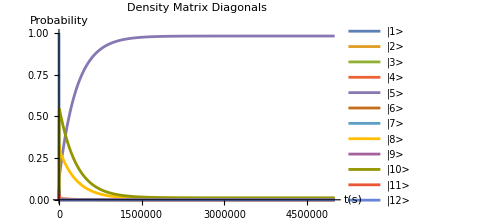

```mathematica
Flatten[{Table[Subscript[ρ, i,i][t],{i,1,12}]}/.dynamics];
Plot[%,{t,0,tmax},PlotRange-> Full,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLegends->{Style["|1> "],Style["|2> "],Style["|3>"],Style["|4>"],Style["|5>"],Style["|6>"],Style["|7>"],Style["|8>"],Style["|9>"],Style["|10>"],Style["|11> "],Style["|12>"]},ImageSize->Medium]
```

#### Transition Rates

```mathematica
Subscript[Γ, P_,j_,i_]=-Subscript[ρ, i,i][t] Subscript[𝒥, P][Subscript[ω, j,i]]Subscript[n, P][Subscript[ω, j,i]]+Subscript[ρ, j,j][t]Subscript[𝒥, P][Subscript[ω, j,i]](1+Subscript[n, P][Subscript[ω, j,i]]);
```

#### Steady State Solutions for density matrices and energy flows

```mathematica
varFunc[TL_,TM_,TR_,ωL_,ωR_,ωM_,gs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{NBEassum,Jassum,ωassum1,ωassum2,μassum,κassum,unitassum,Subscript[T, L]-> TL,Subscript[T, R]-> TR,Subscript[T, M]-> TM,Subscript[ω, L]->ωL,Subscript[ω, R]->ωR,Subscript[ω, M]->ωM,Subscript[g, LM]->gs,Subscript[g, MR]->gs}];
temp1=N[sol//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, i_,j_]'[t]-> 0,Subscript[ρ, i_,j_][t]-> Subscript[ρ, i,j]},1==∑_(i=1)^12 Subscript[ρ, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, i,j],{i,1,12},{j,1,12}]]]]];
Re[{Flatten[Table[Subscript[ρ, i,i],{i,1,12}]/.temp3],Flatten[{Subscript[J, L],Subscript[J, M],Subscript[J, R]}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp3]}]]
```

```mathematica
varFunc[10,5,0.2 ,1,2,3,20,unitassum]
```

{{1.01678×10^-7,0.0000993129,3.33882×10^-7,0.000151857,0.980897,0.000100438,9.32787×10^-6,0.0065321,0.000046426,0.0119018,0.000261052,1.52762×10^-8},{6.9921×10^-6,-8.6008×10^-9,-6.9835×10^-6}}

#### Plots for adjusting T_M (at steady state):

#### Energy Inflows

```mathematica
varEngyFunc[TL_,TM_,TR_,ωL_,ωR_,ωM_,gs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{NBEassum,Jassum,ωassum1,ωassum2,μassum,κassum,unitassum,Subscript[T, L]-> TL,Subscript[T, R]-> TR,Subscript[T, M]-> TM,Subscript[ω, L]->ωL,Subscript[ω, R]->ωR,Subscript[ω, M]->ωM,Subscript[g, LM]->gs,Subscript[g, MR]->gs}];
temp1=N[sol//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, i_,j_]'[t]-> 0,Subscript[ρ, i_,j_][t]-> Subscript[ρ, i,j]},1==∑_(i=1)^12 Subscript[ρ, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, i,j],{i,1,12},{j,1,12}]]]]];
Re[Flatten[{Subscript[J, L],Subscript[J, M],Subscript[J, R]}//.Flatten[{Subscript[ρ, i_,j_][t]->Subscript[ρ, i,j],temp0}]/.temp3]]]
```

```mathematica
PlotEngyFlowsWithTM[Tmin_,Tmax_,Tres_,TL_,TR_,ωL_,ωR_,ωM_,gs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T,T,T},{T,Tmin,Tmax,Tres}];
tempy1=10^5 Table[varEngyFunc[TL,TM,TR,ωL,ωR,ωM,gs,unitassum],{TM,Tmin,Tmax,Tres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy1[[;;,i]]}],{i,1,3}];
ListPlot[temp,AxesStyle->Directive[Black,23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T_M",23.5,FontFamily->"Times New Roman"],Style["10^-5J_P/ℏΔ^2",23.5,FontFamily->"Times New Roman"]},Joined->True,PlotStyle->{{Thickness->Large,Red},{Thickness->Large,Darker[Green]},{Thickness->Large,Blue}},PlotRange->plotrange,PlotLegends->Placed[{Style["J_L",23.5,FontFamily->"Times New Roman"],Style["J_M",23.5,FontFamily->"Times New Roman"],Style["J_R",23.5,FontFamily->"Times New Roman"]},Below],ImageSize->Large]]
```

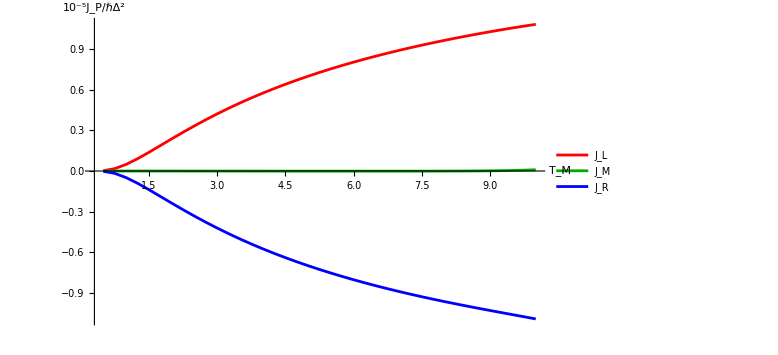

```mathematica
J1=PlotEngyFlowsWithTM[0.5,10,0.25,10,0.2 ,1,2,3,20,Full]
```

#### Amplification Factor (at steady state)

```mathematica
PlotAFWithTM[Tmin_,Tmax_,Tres_,TL_,TR_,ωL_,ωR_,ωM_,gs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T,T,T},{T,Tmin,Tmax,Tres}];
tempy1=10^5 Table[varEngyFunc[TL,TM,TR,ωL,ωR,ωM,gs,unitassum],{TM,Tmin,Tmax,Tres}];
tempy2=10^5 Table[varEngyFunc[TL,TM,TR,ωL,ωR,ωM,gs,unitassum],{TM,Tmin-Tres,Tmax-Tres,Tres}];
temp=Table[MapThread[List,{tempx[[;;,1]],Abs[(tempy1[[;;,1]]-tempy2[[;;,1]])/(tempy1[[;;,2]]-tempy2[[;;,2]])]}]];
ListLogPlot[temp,AxesStyle->Directive[Black,23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T_M",23.5,FontFamily->"Times New Roman"],Style["|α_L|",23.5,FontFamily->"Times New Roman"]},Joined->True,PlotStyle->{Thickness->Large,Black},PlotRange->plotrange,LabelStyle->Directive[23.5,FontFamily->"Times New Roman"],ImageSize->Large]]
```

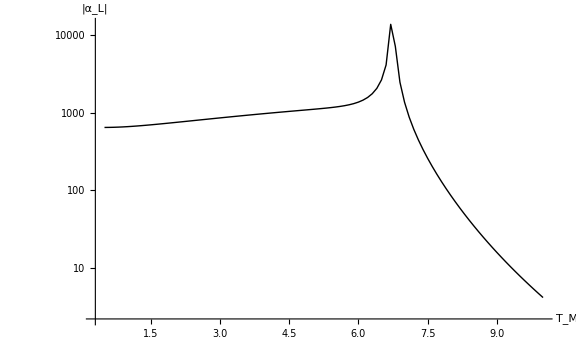

```mathematica
A1=PlotAFWithTM[0.5,10,0.1,10,0.2 ,1,2,3,20,Full]
```

## Equivalent Model for the Quantum Thermal Transistor

### Extended Pauli matrices for the 16-dimensional system

```mathematica
Subscript[σ, z L]=KroneckerProduct[Subscript[σ, z],Subscript[σ, I],Subscript[σ, I],Subscript[σ, I]] ;
Subscript[σ, y L]=KroneckerProduct[Subscript[σ, y],Subscript[σ, I],Subscript[σ, I],Subscript[σ, I]] ;
Subscript[σ, x L]=KroneckerProduct[Subscript[σ, x],Subscript[σ, I],Subscript[σ, I],Subscript[σ, I]] ;
Subscript[σ, z M1]=KroneckerProduct[Subscript[σ, I],Subscript[σ, z],Subscript[σ, I],Subscript[σ, I]] ;
Subscript[σ, y M1]=KroneckerProduct[Subscript[σ, I],Subscript[σ, y],Subscript[σ, I],Subscript[σ, I]] ;
Subscript[σ, x M1]=KroneckerProduct[Subscript[σ, I],Subscript[σ, x],Subscript[σ, I],Subscript[σ, I]] ;
Subscript[σ, z M2]=KroneckerProduct[Subscript[σ, I],Subscript[σ, I],Subscript[σ, z],Subscript[σ, I]] ;
Subscript[σ, y M2]=KroneckerProduct[Subscript[σ, I],Subscript[σ, I],Subscript[σ, y],Subscript[σ, I]] ;
Subscript[σ, x M2]=KroneckerProduct[Subscript[σ, I],Subscript[σ, I],Subscript[σ, x],Subscript[σ, I]] ;
Subscript[σ, z R]=KroneckerProduct[Subscript[σ, I],Subscript[σ, I],Subscript[σ, I],Subscript[σ, z]] ;
Subscript[σ, y R]=KroneckerProduct[Subscript[σ, I],Subscript[σ, I],Subscript[σ, I],Subscript[σ, y]] ;
Subscript[σ, x R]=KroneckerProduct[Subscript[σ, I],Subscript[σ, I],Subscript[σ, I],Subscript[σ, x]] ;
```

### System Hamiltonian

local free Hamiltonians

```mathematica
Subscript[H, L]=ℏ*Subscript[ω, L]*Subscript[z, 1].Subscript[z, 1] ᵀ;
```

```mathematica
Subscript[H, R]=ℏ*Subscript[ω, R]*Subscript[z, 1].Subscript[z, 1] ᵀ;
```

```mathematica
Subscript[H, M1]=ℏ*Subscript[ω, M]*Subscript[z, 1].Subscript[z, 1] ᵀ;
```

```mathematica
Subscript[H, M2]=ℏ*Subscript[ω, M]*Subscript[z, 1].Subscript[z, 1] ᵀ;
```

interaction Hamiltonian

```mathematica
Subscript[V, L-M1]=(ℏ*Subscript[g, LM]*Subscript[σ, z L]. Subscript[σ, z M1]);
Subscript[V, M2-R]=(ℏ*Subscript[g, MR]*Subscript[σ, z M2]. Subscript[σ, z R]);
```

```mathematica
U=2*KroneckerProduct[Subscript[z, 0].Subscript[z, 0] ᵀ,Subscript[z, 1].Subscript[z, 1] ᵀ]-KroneckerProduct[Subscript[z, 0].Subscript[z, 0] ᵀ,Subscript[z, 0].Subscript[z, 0] ᵀ];
```

```mathematica
W=2*KroneckerProduct[Subscript[z, 1].Subscript[z, 1] ᵀ,Subscript[z, 0].Subscript[z, 0] ᵀ]-KroneckerProduct[Subscript[z, 0].Subscript[z, 0] ᵀ,Subscript[z, 0].Subscript[z, 0] ᵀ];
```

```mathematica
Subscript[V, M]=ℏ*Subscript[g, M]*KroneckerProduct[Subscript[σ, z],U,Subscript[σ, I]]+ℏ*Subscript[g, M]*KroneckerProduct[Subscript[σ, I],W,Subscript[σ, z]];
```

total Hamiltonian

```mathematica
Subscript[H, S̄]=KroneckerProduct[Subscript[H, L],Subscript[σ, I],Subscript[σ, I],Subscript[σ, I]]+KroneckerProduct[Subscript[σ, I],Subscript[H, M1],Subscript[σ, I],Subscript[σ, I]]+KroneckerProduct[Subscript[σ, I],Subscript[σ, I],Subscript[H, M2],Subscript[σ, I]]+KroneckerProduct[Subscript[σ, I],Subscript[σ, I],Subscript[σ, I],Subscript[H, R]]+Subscript[V, L-M1]+Subscript[V, M2-R]+Subscript[V, M];
```

```mathematica
{OverBar[Eval],OverBar[Evec]}=Eigensystem[Subscript[H, S̄]];
```

Sort the eigenvalues and eigenstates of the total Hamiltonian

```mathematica
OverBar[list1]=Partition[Riffle[OverBar[Eval],OverBar[Evec]],2];
OverBar[list2]=Sort[OverBar[list1],OrderedQ[{#1[[2]],#2[[2]]}]&];
OverBar[list2]//MatrixForm
```

(ℏ (g_LM+2 g_M+g_MR) | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}
ℏ (g_LM-g_MR+ω_R) | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0}
ℏ (g_LM-2 g_M-g_MR+ω_M) | {0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0}
ℏ (g_LM-2 g_M+g_MR+ω_M+ω_R) | {0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0}
ℏ (-g_LM-2 g_M+g_MR+ω_M) | {0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0}
ℏ (-g_LM+2 g_M-g_MR+ω_M+ω_R) | {0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0}
ℏ (-g_LM-g_MR+2 ω_M) | {0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0}
ℏ (-g_LM+g_MR+2 ω_M+ω_R) | {0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0}
ℏ (-g_LM+g_MR+ω_L) | {0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0}
ℏ (-g_LM-2 g_M-g_MR+ω_L+ω_R) | {0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0}
ℏ (-g_LM+2 g_M-g_MR+ω_L+ω_M) | {0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0}
ℏ (-g_LM+2 g_M+g_MR+ω_L+ω_M+ω_R) | {0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0}
ℏ (g_LM-2 g_M+g_MR+ω_L+ω_M) | {0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0}
ℏ (g_LM+2 g_M-g_MR+ω_L+ω_M+ω_R) | {0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}
ℏ (g_LM-g_MR+ω_L+2 ω_M) | {0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
ℏ (g_LM+g_MR+ω_L+2 ω_M+ω_R) | {1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0})

Total system states using tensor product of individual states

```mathematica
Subscript[S̄, i_,j_,k_,l_]:=Flatten[KroneckerProduct[Subscript[z, i],Subscript[z, j],Subscript[z, k],Subscript[z, l]]]
```

```mathematica
Subscript[Ē, i_,j_,k_,l_]:=First[Select[OverBar[list1],#[[2]]==Subscript[S̄, i,j,k,l]&]][[1]]
```

```mathematica
Subscript[λ̄, 16]={Subscript[S̄, 0,0,0,0]}ᵀ
Subscript[λ̄, 15]={Subscript[S̄, 0,0,0,1]}ᵀ
Subscript[λ̄, 14]={Subscript[S̄, 0,0,1,0]}ᵀ
Subscript[λ̄, 13]={Subscript[S̄, 0,0,1,1]}ᵀ
Subscript[λ̄, 12]={Subscript[S̄, 0,1,0,0]}ᵀ
Subscript[λ̄, 11]={Subscript[S̄, 0,1,0,1]}ᵀ
Subscript[λ̄, 10]={Subscript[S̄, 0,1,1,0]}ᵀ
Subscript[λ̄, 9]={Subscript[S̄, 0,1,1,1]}ᵀ
Subscript[λ̄, 8]={Subscript[S̄, 1,0,0,0]}ᵀ
Subscript[λ̄, 7]={Subscript[S̄, 1,0,0,1]}ᵀ
Subscript[λ̄, 6]={Subscript[S̄, 1,0,1,0]}ᵀ
Subscript[λ̄, 5]={Subscript[S̄, 1,0,1,1]}ᵀ
Subscript[λ̄, 4]={Subscript[S̄, 1,1,0,0]}ᵀ
Subscript[λ̄, 3]={Subscript[S̄, 1,1,0,1]}ᵀ
Subscript[λ̄, 2]={Subscript[S̄, 1,1,1,0]}ᵀ
Subscript[λ̄, 1]={Subscript[S̄, 1,1,1,1]}ᵀ
```

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1},{0},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1},{0},{0},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{1},{0},{0},{0},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{0},{1},{0},{0},{0},{0},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{0},{1},{0},{0},{0},{0},{0},{0},{0}}

{{0},{0},{0},{0},{0},{0},{0},{1},{0},{0},{0},{0},{0},{0},{0},{0}}

{{0},{0},{0},{0},{0},{0},{1},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

{{0},{0},{0},{0},{0},{1},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

{{0},{0},{0},{0},{1},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

{{0},{0},{0},{1},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

{{0},{0},{1},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

{{0},{1},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

{{1},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0},{0}}

Eigenvalues in matrix form

```mathematica
OverBar[HsEVal]=Reverse[Flatten[Table[Subscript[Ē, i,j,k,l],{i,0,1},{j,0,1},{k,0,1},{l,0,1}]]]//MatrixForm
```

(ℏ (g_LM+g_MR+ω_L+2 ω_M+ω_R)
ℏ (g_LM-g_MR+ω_L+2 ω_M)
ℏ (g_LM+2 g_M-g_MR+ω_L+ω_M+ω_R)
ℏ (g_LM-2 g_M+g_MR+ω_L+ω_M)
ℏ (-g_LM+2 g_M+g_MR+ω_L+ω_M+ω_R)
ℏ (-g_LM+2 g_M-g_MR+ω_L+ω_M)
ℏ (-g_LM-2 g_M-g_MR+ω_L+ω_R)
ℏ (-g_LM+g_MR+ω_L)
ℏ (-g_LM+g_MR+2 ω_M+ω_R)
ℏ (-g_LM-g_MR+2 ω_M)
ℏ (-g_LM+2 g_M-g_MR+ω_M+ω_R)
ℏ (-g_LM-2 g_M+g_MR+ω_M)
ℏ (g_LM-2 g_M+g_MR+ω_M+ω_R)
ℏ (g_LM-2 g_M-g_MR+ω_M)
ℏ (g_LM-g_MR+ω_R)
ℏ (g_LM+2 g_M+g_MR))

#### Jump Operators

Induced by bath B_L in qubit L

```mathematica
JumpsL=Table[Table[ConstantArray[0,{16,16}],{j,1,16-i}],{i,1,16}];
```

```mathematica
JumpsL[[1,9-1]][[9,1]]=1;
JumpsL[[2,10-2]][[10,2]]=1;
JumpsL[[3,11-3]][[11,3]]=1/(√2);
JumpsL[[4,12-4]][[12,4]]=1/(√2);
JumpsL[[5,13-5]][[13,5]]=1/(√2);
JumpsL[[6,14-6]][[14,6]]=1/(√2);
JumpsL[[7,15-7]][[15,7]]=1;
JumpsL[[8,16-8]][[16,8]]=1;
```

```mathematica
Subscript[OverBar[AMatrix], L,Subscript[ω, j_,i_]]:=JumpsL[[j,i-j]]
```

Induced by bath B_M in qubit M1

```mathematica
JumpsM1=Table[Table[ConstantArray[0,{16,16}],{j,1,16-i}],{i,1,16}];
```

```mathematica
JumpsM1[[1,5-1]][[5,1]]=1/(√2);
JumpsM1[[2,6-2]][[6,2]]=1/(√2);
JumpsM1[[3,7-3]][[7,3]]=1/(√2);
JumpsM1[[4,8-4]][[8,4]]=1/(√2);
JumpsM1[[9,13-9]][[13,9]]=1/(√2);
JumpsM1[[10,14-10]][[14,10]]=1/(√2);
JumpsM1[[11,15-11]][[15,11]]=1/(√2);
JumpsM1[[12,16-12]][[16,12]]=1/(√2);
```

```mathematica
Subscript[OverBar[AMatrix], M1,Subscript[ω, j_,i_]]:=JumpsM1[[j,i-j]]
```

Induced by bath B_M in qubit M2

```mathematica
JumpsM2=Table[Table[ConstantArray[0,{16,16}],{j,1,16-i}],{i,1,16}];
```

```mathematica
JumpsM2[[1,3-1]][[3,1]]=1/(√2);
JumpsM2[[2,4-2]][[4,2]]=1/(√2);
JumpsM2[[5,7-5]][[7,5]]=1/(√2);
JumpsM2[[6,8-6]][[8,6]]=1/(√2);
JumpsM2[[9,11-9]][[11,9]]=1/(√2);
JumpsM2[[10,12-10]][[12,10]]=1/(√2);
JumpsM2[[13,15-13]][[15,13]]=1/(√2);
JumpsM2[[14,16-14]][[16,14]]=1/(√2);
```

```mathematica
Subscript[OverBar[AMatrix], M2,Subscript[ω, j_,i_]]:=JumpsM2[[j,i-j]]
```

Induced by bath B_R in qubit R

```mathematica
JumpsR=Table[Table[ConstantArray[0,{16,16}],{j,1,16-i}],{i,1,16}];
```

```mathematica
JumpsR[[1,2-1]][[2,1]]=1;
JumpsR[[3,4-3]][[4,3]]=1/(√2);
JumpsR[[5,6-5]][[6,5]]=1/(√2);
JumpsR[[7,8-7]][[8,7]]=1;
JumpsR[[9,10-9]][[10,9]]=1;
JumpsR[[11,12-11]][[12,11]]=1/(√2);
JumpsR[[13,14-13]][[14,13]]=1/(√2);
JumpsR[[15,16-15]][[16,15]]=1;
```

```mathematica
Subscript[OverBar[AMatrix], R,Subscript[ω, j_,i_]]:=JumpsR[[j,i-j]]
```

#### Density Matrix

```mathematica
OverBar[ρMatrix][t]=Table[Subscript[ρ̄, i,j][t],{i,1,16},{j,1,16}];
MatrixForm[%]
```

((ρ̄)_(1,1)[t] | (ρ̄)_(1,2)[t] | (ρ̄)_(1,3)[t] | (ρ̄)_(1,4)[t] | (ρ̄)_(1,5)[t] | (ρ̄)_(1,6)[t] | (ρ̄)_(1,7)[t] | (ρ̄)_(1,8)[t] | (ρ̄)_(1,9)[t] | (ρ̄)_(1,10)[t] | (ρ̄)_(1,11)[t] | (ρ̄)_(1,12)[t] | (ρ̄)_(1,13)[t] | (ρ̄)_(1,14)[t] | (ρ̄)_(1,15)[t] | (ρ̄)_(1,16)[t]
(ρ̄)_(2,1)[t] | (ρ̄)_(2,2)[t] | (ρ̄)_(2,3)[t] | (ρ̄)_(2,4)[t] | (ρ̄)_(2,5)[t] | (ρ̄)_(2,6)[t] | (ρ̄)_(2,7)[t] | (ρ̄)_(2,8)[t] | (ρ̄)_(2,9)[t] | (ρ̄)_(2,10)[t] | (ρ̄)_(2,11)[t] | (ρ̄)_(2,12)[t] | (ρ̄)_(2,13)[t] | (ρ̄)_(2,14)[t] | (ρ̄)_(2,15)[t] | (ρ̄)_(2,16)[t]
(ρ̄)_(3,1)[t] | (ρ̄)_(3,2)[t] | (ρ̄)_(3,3)[t] | (ρ̄)_(3,4)[t] | (ρ̄)_(3,5)[t] | (ρ̄)_(3,6)[t] | (ρ̄)_(3,7)[t] | (ρ̄)_(3,8)[t] | (ρ̄)_(3,9)[t] | (ρ̄)_(3,10)[t] | (ρ̄)_(3,11)[t] | (ρ̄)_(3,12)[t] | (ρ̄)_(3,13)[t] | (ρ̄)_(3,14)[t] | (ρ̄)_(3,15)[t] | (ρ̄)_(3,16)[t]
(ρ̄)_(4,1)[t] | (ρ̄)_(4,2)[t] | (ρ̄)_(4,3)[t] | (ρ̄)_(4,4)[t] | (ρ̄)_(4,5)[t] | (ρ̄)_(4,6)[t] | (ρ̄)_(4,7)[t] | (ρ̄)_(4,8)[t] | (ρ̄)_(4,9)[t] | (ρ̄)_(4,10)[t] | (ρ̄)_(4,11)[t] | (ρ̄)_(4,12)[t] | (ρ̄)_(4,13)[t] | (ρ̄)_(4,14)[t] | (ρ̄)_(4,15)[t] | (ρ̄)_(4,16)[t]
(ρ̄)_(5,1)[t] | (ρ̄)_(5,2)[t] | (ρ̄)_(5,3)[t] | (ρ̄)_(5,4)[t] | (ρ̄)_(5,5)[t] | (ρ̄)_(5,6)[t] | (ρ̄)_(5,7)[t] | (ρ̄)_(5,8)[t] | (ρ̄)_(5,9)[t] | (ρ̄)_(5,10)[t] | (ρ̄)_(5,11)[t] | (ρ̄)_(5,12)[t] | (ρ̄)_(5,13)[t] | (ρ̄)_(5,14)[t] | (ρ̄)_(5,15)[t] | (ρ̄)_(5,16)[t]
(ρ̄)_(6,1)[t] | (ρ̄)_(6,2)[t] | (ρ̄)_(6,3)[t] | (ρ̄)_(6,4)[t] | (ρ̄)_(6,5)[t] | (ρ̄)_(6,6)[t] | (ρ̄)_(6,7)[t] | (ρ̄)_(6,8)[t] | (ρ̄)_(6,9)[t] | (ρ̄)_(6,10)[t] | (ρ̄)_(6,11)[t] | (ρ̄)_(6,12)[t] | (ρ̄)_(6,13)[t] | (ρ̄)_(6,14)[t] | (ρ̄)_(6,15)[t] | (ρ̄)_(6,16)[t]
(ρ̄)_(7,1)[t] | (ρ̄)_(7,2)[t] | (ρ̄)_(7,3)[t] | (ρ̄)_(7,4)[t] | (ρ̄)_(7,5)[t] | (ρ̄)_(7,6)[t] | (ρ̄)_(7,7)[t] | (ρ̄)_(7,8)[t] | (ρ̄)_(7,9)[t] | (ρ̄)_(7,10)[t] | (ρ̄)_(7,11)[t] | (ρ̄)_(7,12)[t] | (ρ̄)_(7,13)[t] | (ρ̄)_(7,14)[t] | (ρ̄)_(7,15)[t] | (ρ̄)_(7,16)[t]
(ρ̄)_(8,1)[t] | (ρ̄)_(8,2)[t] | (ρ̄)_(8,3)[t] | (ρ̄)_(8,4)[t] | (ρ̄)_(8,5)[t] | (ρ̄)_(8,6)[t] | (ρ̄)_(8,7)[t] | (ρ̄)_(8,8)[t] | (ρ̄)_(8,9)[t] | (ρ̄)_(8,10)[t] | (ρ̄)_(8,11)[t] | (ρ̄)_(8,12)[t] | (ρ̄)_(8,13)[t] | (ρ̄)_(8,14)[t] | (ρ̄)_(8,15)[t] | (ρ̄)_(8,16)[t]
(ρ̄)_(9,1)[t] | (ρ̄)_(9,2)[t] | (ρ̄)_(9,3)[t] | (ρ̄)_(9,4)[t] | (ρ̄)_(9,5)[t] | (ρ̄)_(9,6)[t] | (ρ̄)_(9,7)[t] | (ρ̄)_(9,8)[t] | (ρ̄)_(9,9)[t] | (ρ̄)_(9,10)[t] | (ρ̄)_(9,11)[t] | (ρ̄)_(9,12)[t] | (ρ̄)_(9,13)[t] | (ρ̄)_(9,14)[t] | (ρ̄)_(9,15)[t] | (ρ̄)_(9,16)[t]
(ρ̄)_(10,1)[t] | (ρ̄)_(10,2)[t] | (ρ̄)_(10,3)[t] | (ρ̄)_(10,4)[t] | (ρ̄)_(10,5)[t] | (ρ̄)_(10,6)[t] | (ρ̄)_(10,7)[t] | (ρ̄)_(10,8)[t] | (ρ̄)_(10,9)[t] | (ρ̄)_(10,10)[t] | (ρ̄)_(10,11)[t] | (ρ̄)_(10,12)[t] | (ρ̄)_(10,13)[t] | (ρ̄)_(10,14)[t] | (ρ̄)_(10,15)[t] | (ρ̄)_(10,16)[t]
(ρ̄)_(11,1)[t] | (ρ̄)_(11,2)[t] | (ρ̄)_(11,3)[t] | (ρ̄)_(11,4)[t] | (ρ̄)_(11,5)[t] | (ρ̄)_(11,6)[t] | (ρ̄)_(11,7)[t] | (ρ̄)_(11,8)[t] | (ρ̄)_(11,9)[t] | (ρ̄)_(11,10)[t] | (ρ̄)_(11,11)[t] | (ρ̄)_(11,12)[t] | (ρ̄)_(11,13)[t] | (ρ̄)_(11,14)[t] | (ρ̄)_(11,15)[t] | (ρ̄)_(11,16)[t]
(ρ̄)_(12,1)[t] | (ρ̄)_(12,2)[t] | (ρ̄)_(12,3)[t] | (ρ̄)_(12,4)[t] | (ρ̄)_(12,5)[t] | (ρ̄)_(12,6)[t] | (ρ̄)_(12,7)[t] | (ρ̄)_(12,8)[t] | (ρ̄)_(12,9)[t] | (ρ̄)_(12,10)[t] | (ρ̄)_(12,11)[t] | (ρ̄)_(12,12)[t] | (ρ̄)_(12,13)[t] | (ρ̄)_(12,14)[t] | (ρ̄)_(12,15)[t] | (ρ̄)_(12,16)[t]
(ρ̄)_(13,1)[t] | (ρ̄)_(13,2)[t] | (ρ̄)_(13,3)[t] | (ρ̄)_(13,4)[t] | (ρ̄)_(13,5)[t] | (ρ̄)_(13,6)[t] | (ρ̄)_(13,7)[t] | (ρ̄)_(13,8)[t] | (ρ̄)_(13,9)[t] | (ρ̄)_(13,10)[t] | (ρ̄)_(13,11)[t] | (ρ̄)_(13,12)[t] | (ρ̄)_(13,13)[t] | (ρ̄)_(13,14)[t] | (ρ̄)_(13,15)[t] | (ρ̄)_(13,16)[t]
(ρ̄)_(14,1)[t] | (ρ̄)_(14,2)[t] | (ρ̄)_(14,3)[t] | (ρ̄)_(14,4)[t] | (ρ̄)_(14,5)[t] | (ρ̄)_(14,6)[t] | (ρ̄)_(14,7)[t] | (ρ̄)_(14,8)[t] | (ρ̄)_(14,9)[t] | (ρ̄)_(14,10)[t] | (ρ̄)_(14,11)[t] | (ρ̄)_(14,12)[t] | (ρ̄)_(14,13)[t] | (ρ̄)_(14,14)[t] | (ρ̄)_(14,15)[t] | (ρ̄)_(14,16)[t]
(ρ̄)_(15,1)[t] | (ρ̄)_(15,2)[t] | (ρ̄)_(15,3)[t] | (ρ̄)_(15,4)[t] | (ρ̄)_(15,5)[t] | (ρ̄)_(15,6)[t] | (ρ̄)_(15,7)[t] | (ρ̄)_(15,8)[t] | (ρ̄)_(15,9)[t] | (ρ̄)_(15,10)[t] | (ρ̄)_(15,11)[t] | (ρ̄)_(15,12)[t] | (ρ̄)_(15,13)[t] | (ρ̄)_(15,14)[t] | (ρ̄)_(15,15)[t] | (ρ̄)_(15,16)[t]
(ρ̄)_(16,1)[t] | (ρ̄)_(16,2)[t] | (ρ̄)_(16,3)[t] | (ρ̄)_(16,4)[t] | (ρ̄)_(16,5)[t] | (ρ̄)_(16,6)[t] | (ρ̄)_(16,7)[t] | (ρ̄)_(16,8)[t] | (ρ̄)_(16,9)[t] | (ρ̄)_(16,10)[t] | (ρ̄)_(16,11)[t] | (ρ̄)_(16,12)[t] | (ρ̄)_(16,13)[t] | (ρ̄)_(16,14)[t] | (ρ̄)_(16,15)[t] | (ρ̄)_(16,16)[t])

#### Possible Transition Frequencies

```mathematica
OverBar[ωMatrix]={Flatten[Table[Subscript[ω, i,j],{i,1,16},{j,i+1,16}]]}
```

{{ω_(1,2),ω_(1,3),ω_(1,4),ω_(1,5),ω_(1,6),ω_(1,7),ω_(1,8),ω_(1,9),ω_(1,10),ω_(1,11),ω_(1,12),ω_(1,13),ω_(1,14),ω_(1,15),ω_(1,16),ω_(2,3),ω_(2,4),ω_(2,5),ω_(2,6),ω_(2,7),ω_(2,8),ω_(2,9),ω_(2,10),ω_(2,11),ω_(2,12),ω_(2,13),ω_(2,14),ω_(2,15),ω_(2,16),ω_(3,4),ω_(3,5),ω_(3,6),ω_(3,7),ω_(3,8),ω_(3,9),ω_(3,10),ω_(3,11),ω_(3,12),ω_(3,13),ω_(3,14),ω_(3,15),ω_(3,16),ω_(4,5),ω_(4,6),ω_(4,7),ω_(4,8),ω_(4,9),ω_(4,10),ω_(4,11),ω_(4,12),ω_(4,13),ω_(4,14),ω_(4,15),ω_(4,16),ω_(5,6),ω_(5,7),ω_(5,8),ω_(5,9),ω_(5,10),ω_(5,11),ω_(5,12),ω_(5,13),ω_(5,14),ω_(5,15),ω_(5,16),ω_(6,7),ω_(6,8),ω_(6,9),ω_(6,10),ω_(6,11),ω_(6,12),ω_(6,13),ω_(6,14),ω_(6,15),ω_(6,16),ω_(7,8),ω_(7,9),ω_(7,10),ω_(7,11),ω_(7,12),ω_(7,13),ω_(7,14),ω_(7,15),ω_(7,16),ω_(8,9),ω_(8,10),ω_(8,11),ω_(8,12),ω_(8,13),ω_(8,14),ω_(8,15),ω_(8,16),ω_(9,10),ω_(9,11),ω_(9,12),ω_(9,13),ω_(9,14),ω_(9,15),ω_(9,16),ω_(10,11),ω_(10,12),ω_(10,13),ω_(10,14),ω_(10,15),ω_(10,16),ω_(11,12),ω_(11,13),ω_(11,14),ω_(11,15),ω_(11,16),ω_(12,13),ω_(12,14),ω_(12,15),ω_(12,16),ω_(13,14),ω_(13,15),ω_(13,16),ω_(14,15),ω_(14,16),ω_(15,16)}}

```mathematica
Length[Flatten[OverBar[ωMatrix]]]
```

120

```mathematica
OverBar[ωVals]=Flatten[Simplify[Table[(OverBar[HsEVal][[1,i]]-OverBar[HsEVal][[1,j]])/ℏ,{i,1,16},{j,i+1,16}]]];
```

```mathematica
Length[Flatten[OverBar[ωVals]]]
```

120

### Lindblad Super Operator

For direct Coupling

```mathematica
Subscript[ℒ̄, P_]:=Subscript[ℒ̄, P]=∑_(α=1)^120 (Subscript[𝒥, P][Part[OverBar[ωMatrix],1,α]](1+Subscript[n, P][Part[OverBar[ωMatrix],1,α]])(Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]].OverBar[ρMatrix][t].Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]] ᵀ- 1/2*Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]] ᵀ.Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]].OverBar[ρMatrix][t]-1/2 OverBar[ρMatrix][t].Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]] ᵀ.Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]])+(Subscript[𝒥, P][Part[OverBar[ωMatrix],1,α]] Subscript[n, P][Part[OverBar[ωMatrix],1,α]](Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]] ᵀ.OverBar[ρMatrix][t].Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]]-1/2* Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]].Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]] ᵀ.OverBar[ρMatrix][t]-1/2 OverBar[ρMatrix][t].Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]].Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]] ᵀ)));
```

### Master Equation

```mathematica
OverBar[dρ]=MatrixForm[Subscript[ℒ̄, L]+Subscript[ℒ̄, M1]+Subscript[ℒ̄, M2]+Subscript[ℒ̄, R]-(ⅈ/ℏ(Subscript[H, S̄].OverBar[ρMatrix][t]-OverBar[ρMatrix][t].Subscript[H, S̄]))]//.{-Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] +(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>Subscript[Γ̄, P,j,i],Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] -(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>-Subscript[Γ̄, P,j,i],- 1/2 Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] +1/2(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>1/2 Subscript[Γ̄, P,j,i],1/2 Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] -1/2(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>-1/2 Subscript[Γ̄, P,j,i]};
```

```mathematica
MatrixForm[%]
```

```mathematica
OverBar[dρ][[1,1]][[1]]
```

-(Γ̄)_(L,1,9)-1/2 (Γ̄)_(M1,1,5)-1/2 (Γ̄)_(M2,1,3)-(Γ̄)_(R,1,2)

```mathematica
OverBar[dρ][[1,2]][[2]]
```

-(Γ̄)_(L,2,10)-1/2 (Γ̄)_(M1,2,6)-1/2 (Γ̄)_(M2,2,4)+(Γ̄)_(R,1,2)

```mathematica
OverBar[dρ][[1,3]][[3]]
```

-1/2 (Γ̄)_(L,3,11)-1/2 (Γ̄)_(M1,3,7)+1/2 (Γ̄)_(M2,1,3)-1/2 (Γ̄)_(R,3,4)

```mathematica
OverBar[dρ][[1,4]][[4]]
```

-1/2 (Γ̄)_(L,4,12)-1/2 (Γ̄)_(M1,4,8)+1/2 (Γ̄)_(M2,2,4)+1/2 (Γ̄)_(R,3,4)

```mathematica
OverBar[dρ][[1,5]][[5]]
```

-1/2 (Γ̄)_(L,5,13)+1/2 (Γ̄)_(M1,1,5)-1/2 (Γ̄)_(M2,5,7)-1/2 (Γ̄)_(R,5,6)

```mathematica
OverBar[dρ][[1,6]][[6]]
```

-1/2 (Γ̄)_(L,6,14)+1/2 (Γ̄)_(M1,2,6)-1/2 (Γ̄)_(M2,6,8)+1/2 (Γ̄)_(R,5,6)

```mathematica
OverBar[dρ][[1,7]][[7]]
```

-(Γ̄)_(L,7,15)+1/2 (Γ̄)_(M1,3,7)+1/2 (Γ̄)_(M2,5,7)-(Γ̄)_(R,7,8)

```mathematica
OverBar[dρ][[1,8]][[8]]
```

-(Γ̄)_(L,8,16)+1/2 (Γ̄)_(M1,4,8)+1/2 (Γ̄)_(M2,6,8)+(Γ̄)_(R,7,8)

```mathematica
OverBar[dρ][[1,9]][[9]]
```

(Γ̄)_(L,1,9)-1/2 (Γ̄)_(M1,9,13)-1/2 (Γ̄)_(M2,9,11)-(Γ̄)_(R,9,10)

```mathematica
OverBar[dρ][[1,10]][[10]]
```

(Γ̄)_(L,2,10)-1/2 (Γ̄)_(M1,10,14)-1/2 (Γ̄)_(M2,10,12)+(Γ̄)_(R,9,10)

```mathematica
OverBar[dρ][[1,11]][[11]]
```

1/2 (Γ̄)_(L,3,11)-1/2 (Γ̄)_(M1,11,15)+1/2 (Γ̄)_(M2,9,11)-1/2 (Γ̄)_(R,11,12)

```mathematica
OverBar[dρ][[1,12]][[12]]
```

1/2 (Γ̄)_(L,4,12)-1/2 (Γ̄)_(M1,12,16)+1/2 (Γ̄)_(M2,10,12)+1/2 (Γ̄)_(R,11,12)

```mathematica
OverBar[dρ][[1,13]][[13]]
```

1/2 (Γ̄)_(L,5,13)+1/2 (Γ̄)_(M1,9,13)-1/2 (Γ̄)_(M2,13,15)-1/2 (Γ̄)_(R,13,14)

```mathematica
OverBar[dρ][[1,14]][[14]]
```

1/2 (Γ̄)_(L,6,14)+1/2 (Γ̄)_(M1,10,14)-1/2 (Γ̄)_(M2,14,16)+1/2 (Γ̄)_(R,13,14)

```mathematica
OverBar[dρ][[1,15]][[15]]
```

(Γ̄)_(L,7,15)+1/2 (Γ̄)_(M1,11,15)+1/2 (Γ̄)_(M2,13,15)-(Γ̄)_(R,15,16)

```mathematica
OverBar[dρ][[1,16]][[16]]
```

(Γ̄)_(L,8,16)+1/2 (Γ̄)_(M1,12,16)+1/2 (Γ̄)_(M2,14,16)+(Γ̄)_(R,15,16)

### Thermal Energy Flows

```mathematica
OverBar[HsMatrix]=DiagonalMatrix[ℏ{Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3],Subscript[ω, 4],Subscript[ω, 5],Subscript[ω, 6],Subscript[ω, 7],Subscript[ω, 8],Subscript[ω, 9],Subscript[ω, 10],Subscript[ω, 11],Subscript[ω, 12],Subscript[ω, 13],Subscript[ω, 14],Subscript[ω, 15],Subscript[ω, 16]}];
```

```mathematica
Subscript[J̄, P_]:=Subscript[J̄, P]=Tr[Subscript[ℒ̄, P].OverBar[HsMatrix]]//.{(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]-Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] :>Subscript[Γ̄, Q,j,i],-((1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t])+Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] :>-Subscript[Γ̄, Q,j,i],1/2(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]-1/2 Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] :>1/2 Subscript[Γ̄, Q,j,i],1/2 Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] -1/2(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>-1/2 Subscript[Γ̄, Q,j,i]};
```

```mathematica
Subscript[J̄, L]
```

-ℏ ω_1 (Γ̄)_(L,1,9)+ℏ ω_9 (Γ̄)_(L,1,9)-ℏ ω_2 (Γ̄)_(L,2,10)+ℏ ω_10 (Γ̄)_(L,2,10)-1/2 ℏ ω_3 (Γ̄)_(L,3,11)+1/2 ℏ ω_11 (Γ̄)_(L,3,11)-1/2 ℏ ω_4 (Γ̄)_(L,4,12)+1/2 ℏ ω_12 (Γ̄)_(L,4,12)-1/2 ℏ ω_5 (Γ̄)_(L,5,13)+1/2 ℏ ω_13 (Γ̄)_(L,5,13)-1/2 ℏ ω_6 (Γ̄)_(L,6,14)+1/2 ℏ ω_14 (Γ̄)_(L,6,14)-ℏ ω_7 (Γ̄)_(L,7,15)+ℏ ω_15 (Γ̄)_(L,7,15)-ℏ ω_8 (Γ̄)_(L,8,16)+ℏ ω_16 (Γ̄)_(L,8,16)

```mathematica
Subscript[J̄, R]
```

-ℏ ω_1 (Γ̄)_(R,1,2)+ℏ ω_2 (Γ̄)_(R,1,2)-1/2 ℏ ω_3 (Γ̄)_(R,3,4)+1/2 ℏ ω_4 (Γ̄)_(R,3,4)-1/2 ℏ ω_5 (Γ̄)_(R,5,6)+1/2 ℏ ω_6 (Γ̄)_(R,5,6)-ℏ ω_7 (Γ̄)_(R,7,8)+ℏ ω_8 (Γ̄)_(R,7,8)-ℏ ω_9 (Γ̄)_(R,9,10)+ℏ ω_10 (Γ̄)_(R,9,10)-1/2 ℏ ω_11 (Γ̄)_(R,11,12)+1/2 ℏ ω_12 (Γ̄)_(R,11,12)-1/2 ℏ ω_13 (Γ̄)_(R,13,14)+1/2 ℏ ω_14 (Γ̄)_(R,13,14)-ℏ ω_15 (Γ̄)_(R,15,16)+ℏ ω_16 (Γ̄)_(R,15,16)

```mathematica
Subscript[J̄, M]=Tr[(Subscript[ℒ̄, M1]+Subscript[ℒ̄, M2]).OverBar[HsMatrix]]//.{-Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] +(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>Subscript[Γ̄, Q,j,i],Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] -(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>-Subscript[Γ̄, Q,j,i],1/2(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]-1/2 Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] :>1/2 Subscript[Γ̄, Q,j,i],1/2 Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] -1/2(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>-1/2 Subscript[Γ̄, Q,j,i]}
```

ℏ ω_1 (-1/2 (Γ̄)_(M1,1,5)-1/2 (Γ̄)_(M2,1,3))+ℏ ω_3 (-1/2 (Γ̄)_(M1,3,7)+1/2 (Γ̄)_(M2,1,3))+ℏ ω_2 (-1/2 (Γ̄)_(M1,2,6)-1/2 (Γ̄)_(M2,2,4))+ℏ ω_4 (-1/2 (Γ̄)_(M1,4,8)+1/2 (Γ̄)_(M2,2,4))+ℏ ω_5 (1/2 (Γ̄)_(M1,1,5)-1/2 (Γ̄)_(M2,5,7))+ℏ ω_7 (1/2 (Γ̄)_(M1,3,7)+1/2 (Γ̄)_(M2,5,7))+ℏ ω_6 (1/2 (Γ̄)_(M1,2,6)-1/2 (Γ̄)_(M2,6,8))+ℏ ω_8 (1/2 (Γ̄)_(M1,4,8)+1/2 (Γ̄)_(M2,6,8))+ℏ ω_9 (-1/2 (Γ̄)_(M1,9,13)-1/2 (Γ̄)_(M2,9,11))+ℏ ω_11 (-1/2 (Γ̄)_(M1,11,15)+1/2 (Γ̄)_(M2,9,11))+ℏ ω_10 (-1/2 (Γ̄)_(M1,10,14)-1/2 (Γ̄)_(M2,10,12))+ℏ ω_12 (-1/2 (Γ̄)_(M1,12,16)+1/2 (Γ̄)_(M2,10,12))+ℏ ω_13 (1/2 (Γ̄)_(M1,9,13)-1/2 (Γ̄)_(M2,13,15))+ℏ ω_15 (1/2 (Γ̄)_(M1,11,15)+1/2 (Γ̄)_(M2,13,15))+ℏ ω_14 (1/2 (Γ̄)_(M1,10,14)-1/2 (Γ̄)_(M2,14,16))+ℏ ω_16 (1/2 (Γ̄)_(M1,12,16)+1/2 (Γ̄)_(M2,14,16))

## Simulations

#### Bose - Einstein Distribution

```mathematica
NBEassum=Subscript[n, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

#### Bath Spectral Density

```mathematica
Jassum=Subscript[𝒥, P_][ω_]-> Subscript[μ, P]*Subscript[μ, P]*ω*ⅇ^((-Abs[ω])/Subscript[κ, P]);
```

#### Stationary State Solutions of master equation

```mathematica
OverBar[RHS]=Subscript[ℒ̄, L]+Subscript[ℒ̄, M1]+Subscript[ℒ̄, M2]+Subscript[ℒ̄, R]-(ⅈ/ℏ(Subscript[H, S̄].OverBar[ρMatrix][t]-OverBar[ρMatrix][t].Subscript[H, S̄]));
```

```mathematica
OverBar[LHS]=D[OverBar[ρMatrix][t], t];
MatrixForm[%]
```

((ρ̄)_(1,1)'[t] | (ρ̄)_(1,2)'[t] | (ρ̄)_(1,3)'[t] | (ρ̄)_(1,4)'[t] | (ρ̄)_(1,5)'[t] | (ρ̄)_(1,6)'[t] | (ρ̄)_(1,7)'[t] | (ρ̄)_(1,8)'[t] | (ρ̄)_(1,9)'[t] | (ρ̄)_(1,10)'[t] | (ρ̄)_(1,11)'[t] | (ρ̄)_(1,12)'[t] | (ρ̄)_(1,13)'[t] | (ρ̄)_(1,14)'[t] | (ρ̄)_(1,15)'[t] | (ρ̄)_(1,16)'[t]
(ρ̄)_(2,1)'[t] | (ρ̄)_(2,2)'[t] | (ρ̄)_(2,3)'[t] | (ρ̄)_(2,4)'[t] | (ρ̄)_(2,5)'[t] | (ρ̄)_(2,6)'[t] | (ρ̄)_(2,7)'[t] | (ρ̄)_(2,8)'[t] | (ρ̄)_(2,9)'[t] | (ρ̄)_(2,10)'[t] | (ρ̄)_(2,11)'[t] | (ρ̄)_(2,12)'[t] | (ρ̄)_(2,13)'[t] | (ρ̄)_(2,14)'[t] | (ρ̄)_(2,15)'[t] | (ρ̄)_(2,16)'[t]
(ρ̄)_(3,1)'[t] | (ρ̄)_(3,2)'[t] | (ρ̄)_(3,3)'[t] | (ρ̄)_(3,4)'[t] | (ρ̄)_(3,5)'[t] | (ρ̄)_(3,6)'[t] | (ρ̄)_(3,7)'[t] | (ρ̄)_(3,8)'[t] | (ρ̄)_(3,9)'[t] | (ρ̄)_(3,10)'[t] | (ρ̄)_(3,11)'[t] | (ρ̄)_(3,12)'[t] | (ρ̄)_(3,13)'[t] | (ρ̄)_(3,14)'[t] | (ρ̄)_(3,15)'[t] | (ρ̄)_(3,16)'[t]
(ρ̄)_(4,1)'[t] | (ρ̄)_(4,2)'[t] | (ρ̄)_(4,3)'[t] | (ρ̄)_(4,4)'[t] | (ρ̄)_(4,5)'[t] | (ρ̄)_(4,6)'[t] | (ρ̄)_(4,7)'[t] | (ρ̄)_(4,8)'[t] | (ρ̄)_(4,9)'[t] | (ρ̄)_(4,10)'[t] | (ρ̄)_(4,11)'[t] | (ρ̄)_(4,12)'[t] | (ρ̄)_(4,13)'[t] | (ρ̄)_(4,14)'[t] | (ρ̄)_(4,15)'[t] | (ρ̄)_(4,16)'[t]
(ρ̄)_(5,1)'[t] | (ρ̄)_(5,2)'[t] | (ρ̄)_(5,3)'[t] | (ρ̄)_(5,4)'[t] | (ρ̄)_(5,5)'[t] | (ρ̄)_(5,6)'[t] | (ρ̄)_(5,7)'[t] | (ρ̄)_(5,8)'[t] | (ρ̄)_(5,9)'[t] | (ρ̄)_(5,10)'[t] | (ρ̄)_(5,11)'[t] | (ρ̄)_(5,12)'[t] | (ρ̄)_(5,13)'[t] | (ρ̄)_(5,14)'[t] | (ρ̄)_(5,15)'[t] | (ρ̄)_(5,16)'[t]
(ρ̄)_(6,1)'[t] | (ρ̄)_(6,2)'[t] | (ρ̄)_(6,3)'[t] | (ρ̄)_(6,4)'[t] | (ρ̄)_(6,5)'[t] | (ρ̄)_(6,6)'[t] | (ρ̄)_(6,7)'[t] | (ρ̄)_(6,8)'[t] | (ρ̄)_(6,9)'[t] | (ρ̄)_(6,10)'[t] | (ρ̄)_(6,11)'[t] | (ρ̄)_(6,12)'[t] | (ρ̄)_(6,13)'[t] | (ρ̄)_(6,14)'[t] | (ρ̄)_(6,15)'[t] | (ρ̄)_(6,16)'[t]
(ρ̄)_(7,1)'[t] | (ρ̄)_(7,2)'[t] | (ρ̄)_(7,3)'[t] | (ρ̄)_(7,4)'[t] | (ρ̄)_(7,5)'[t] | (ρ̄)_(7,6)'[t] | (ρ̄)_(7,7)'[t] | (ρ̄)_(7,8)'[t] | (ρ̄)_(7,9)'[t] | (ρ̄)_(7,10)'[t] | (ρ̄)_(7,11)'[t] | (ρ̄)_(7,12)'[t] | (ρ̄)_(7,13)'[t] | (ρ̄)_(7,14)'[t] | (ρ̄)_(7,15)'[t] | (ρ̄)_(7,16)'[t]
(ρ̄)_(8,1)'[t] | (ρ̄)_(8,2)'[t] | (ρ̄)_(8,3)'[t] | (ρ̄)_(8,4)'[t] | (ρ̄)_(8,5)'[t] | (ρ̄)_(8,6)'[t] | (ρ̄)_(8,7)'[t] | (ρ̄)_(8,8)'[t] | (ρ̄)_(8,9)'[t] | (ρ̄)_(8,10)'[t] | (ρ̄)_(8,11)'[t] | (ρ̄)_(8,12)'[t] | (ρ̄)_(8,13)'[t] | (ρ̄)_(8,14)'[t] | (ρ̄)_(8,15)'[t] | (ρ̄)_(8,16)'[t]
(ρ̄)_(9,1)'[t] | (ρ̄)_(9,2)'[t] | (ρ̄)_(9,3)'[t] | (ρ̄)_(9,4)'[t] | (ρ̄)_(9,5)'[t] | (ρ̄)_(9,6)'[t] | (ρ̄)_(9,7)'[t] | (ρ̄)_(9,8)'[t] | (ρ̄)_(9,9)'[t] | (ρ̄)_(9,10)'[t] | (ρ̄)_(9,11)'[t] | (ρ̄)_(9,12)'[t] | (ρ̄)_(9,13)'[t] | (ρ̄)_(9,14)'[t] | (ρ̄)_(9,15)'[t] | (ρ̄)_(9,16)'[t]
(ρ̄)_(10,1)'[t] | (ρ̄)_(10,2)'[t] | (ρ̄)_(10,3)'[t] | (ρ̄)_(10,4)'[t] | (ρ̄)_(10,5)'[t] | (ρ̄)_(10,6)'[t] | (ρ̄)_(10,7)'[t] | (ρ̄)_(10,8)'[t] | (ρ̄)_(10,9)'[t] | (ρ̄)_(10,10)'[t] | (ρ̄)_(10,11)'[t] | (ρ̄)_(10,12)'[t] | (ρ̄)_(10,13)'[t] | (ρ̄)_(10,14)'[t] | (ρ̄)_(10,15)'[t] | (ρ̄)_(10,16)'[t]
(ρ̄)_(11,1)'[t] | (ρ̄)_(11,2)'[t] | (ρ̄)_(11,3)'[t] | (ρ̄)_(11,4)'[t] | (ρ̄)_(11,5)'[t] | (ρ̄)_(11,6)'[t] | (ρ̄)_(11,7)'[t] | (ρ̄)_(11,8)'[t] | (ρ̄)_(11,9)'[t] | (ρ̄)_(11,10)'[t] | (ρ̄)_(11,11)'[t] | (ρ̄)_(11,12)'[t] | (ρ̄)_(11,13)'[t] | (ρ̄)_(11,14)'[t] | (ρ̄)_(11,15)'[t] | (ρ̄)_(11,16)'[t]
(ρ̄)_(12,1)'[t] | (ρ̄)_(12,2)'[t] | (ρ̄)_(12,3)'[t] | (ρ̄)_(12,4)'[t] | (ρ̄)_(12,5)'[t] | (ρ̄)_(12,6)'[t] | (ρ̄)_(12,7)'[t] | (ρ̄)_(12,8)'[t] | (ρ̄)_(12,9)'[t] | (ρ̄)_(12,10)'[t] | (ρ̄)_(12,11)'[t] | (ρ̄)_(12,12)'[t] | (ρ̄)_(12,13)'[t] | (ρ̄)_(12,14)'[t] | (ρ̄)_(12,15)'[t] | (ρ̄)_(12,16)'[t]
(ρ̄)_(13,1)'[t] | (ρ̄)_(13,2)'[t] | (ρ̄)_(13,3)'[t] | (ρ̄)_(13,4)'[t] | (ρ̄)_(13,5)'[t] | (ρ̄)_(13,6)'[t] | (ρ̄)_(13,7)'[t] | (ρ̄)_(13,8)'[t] | (ρ̄)_(13,9)'[t] | (ρ̄)_(13,10)'[t] | (ρ̄)_(13,11)'[t] | (ρ̄)_(13,12)'[t] | (ρ̄)_(13,13)'[t] | (ρ̄)_(13,14)'[t] | (ρ̄)_(13,15)'[t] | (ρ̄)_(13,16)'[t]
(ρ̄)_(14,1)'[t] | (ρ̄)_(14,2)'[t] | (ρ̄)_(14,3)'[t] | (ρ̄)_(14,4)'[t] | (ρ̄)_(14,5)'[t] | (ρ̄)_(14,6)'[t] | (ρ̄)_(14,7)'[t] | (ρ̄)_(14,8)'[t] | (ρ̄)_(14,9)'[t] | (ρ̄)_(14,10)'[t] | (ρ̄)_(14,11)'[t] | (ρ̄)_(14,12)'[t] | (ρ̄)_(14,13)'[t] | (ρ̄)_(14,14)'[t] | (ρ̄)_(14,15)'[t] | (ρ̄)_(14,16)'[t]
(ρ̄)_(15,1)'[t] | (ρ̄)_(15,2)'[t] | (ρ̄)_(15,3)'[t] | (ρ̄)_(15,4)'[t] | (ρ̄)_(15,5)'[t] | (ρ̄)_(15,6)'[t] | (ρ̄)_(15,7)'[t] | (ρ̄)_(15,8)'[t] | (ρ̄)_(15,9)'[t] | (ρ̄)_(15,10)'[t] | (ρ̄)_(15,11)'[t] | (ρ̄)_(15,12)'[t] | (ρ̄)_(15,13)'[t] | (ρ̄)_(15,14)'[t] | (ρ̄)_(15,15)'[t] | (ρ̄)_(15,16)'[t]
(ρ̄)_(16,1)'[t] | (ρ̄)_(16,2)'[t] | (ρ̄)_(16,3)'[t] | (ρ̄)_(16,4)'[t] | (ρ̄)_(16,5)'[t] | (ρ̄)_(16,6)'[t] | (ρ̄)_(16,7)'[t] | (ρ̄)_(16,8)'[t] | (ρ̄)_(16,9)'[t] | (ρ̄)_(16,10)'[t] | (ρ̄)_(16,11)'[t] | (ρ̄)_(16,12)'[t] | (ρ̄)_(16,13)'[t] | (ρ̄)_(16,14)'[t] | (ρ̄)_(16,15)'[t] | (ρ̄)_(16,16)'[t])

```mathematica
OverBar[sol]=Flatten[Solve[OverBar[LHS]==OverBar[RHS],Flatten[Table[Subscript[ρ̄, i,j]'[t],{i,1,16},{j,1,16}]]]/.Rule->Equal];
```

Separate diagonal and off diagonal equations,

```mathematica
OverBar[soldiag]=OverBar[sol][[1;; ;;17]];
OverBar[soloffdiag]=Delete[OverBar[sol],Table[{1+17i},{i,0,15}]];
```

Off diagonal Solutions

```mathematica
Flatten[{OverBar[soloffdiag]/.{Subscript[ρ̄, i_,j_]'[t]-> 0,Subscript[ρ̄, i_,j_][t]-> Subscript[ρ̄, i,j]}}];
OverBar[soloffdiagstat]=Solve[%,DeleteCases[Flatten[Table[Subscript[ρ̄, i,j]-i,j Subscript[ρ̄, i,j],{i,1,16},{j,1,16}]],0]]
```

{{(ρ̄)_(1,2)→0,(ρ̄)_(1,3)→0,(ρ̄)_(1,4)→0,(ρ̄)_(1,5)→0,(ρ̄)_(1,6)→0,(ρ̄)_(1,7)→0,(ρ̄)_(1,8)→0,(ρ̄)_(1,9)→0,(ρ̄)_(1,10)→0,(ρ̄)_(1,11)→0,(ρ̄)_(1,12)→0,(ρ̄)_(1,13)→0,(ρ̄)_(1,14)→0,(ρ̄)_(1,15)→0,(ρ̄)_(1,16)→0,(ρ̄)_(2,1)→0,(ρ̄)_(2,3)→0,(ρ̄)_(2,4)→0,(ρ̄)_(2,5)→0,(ρ̄)_(2,6)→0,(ρ̄)_(2,7)→0,(ρ̄)_(2,8)→0,(ρ̄)_(2,9)→0,(ρ̄)_(2,10)→0,(ρ̄)_(2,11)→0,(ρ̄)_(2,12)→0,(ρ̄)_(2,13)→0,(ρ̄)_(2,14)→0,(ρ̄)_(2,15)→0,(ρ̄)_(2,16)→0,(ρ̄)_(3,1)→0,(ρ̄)_(3,2)→0,(ρ̄)_(3,4)→0,(ρ̄)_(3,5)→0,(ρ̄)_(3,6)→0,(ρ̄)_(3,7)→0,(ρ̄)_(3,8)→0,(ρ̄)_(3,9)→0,(ρ̄)_(3,10)→0,(ρ̄)_(3,11)→0,(ρ̄)_(3,12)→0,(ρ̄)_(3,13)→0,(ρ̄)_(3,14)→0,(ρ̄)_(3,15)→0,(ρ̄)_(3,16)→0,(ρ̄)_(4,1)→0,(ρ̄)_(4,2)→0,(ρ̄)_(4,3)→0,(ρ̄)_(4,5)→0,(ρ̄)_(4,6)→0,(ρ̄)_(4,7)→0,(ρ̄)_(4,8)→0,(ρ̄)_(4,9)→0,(ρ̄)_(4,10)→0,(ρ̄)_(4,11)→0,(ρ̄)_(4,12)→0,(ρ̄)_(4,13)→0,(ρ̄)_(4,14)→0,(ρ̄)_(4,15)→0,(ρ̄)_(4,16)→0,(ρ̄)_(5,1)→0,(ρ̄)_(5,2)→0,(ρ̄)_(5,3)→0,(ρ̄)_(5,4)→0,(ρ̄)_(5,6)→0,(ρ̄)_(5,7)→0,(ρ̄)_(5,8)→0,(ρ̄)_(5,9)→0,(ρ̄)_(5,10)→0,(ρ̄)_(5,11)→0,(ρ̄)_(5,12)→0,(ρ̄)_(5,13)→0,(ρ̄)_(5,14)→0,(ρ̄)_(5,15)→0,(ρ̄)_(5,16)→0,(ρ̄)_(6,1)→0,(ρ̄)_(6,2)→0,(ρ̄)_(6,3)→0,(ρ̄)_(6,4)→0,(ρ̄)_(6,5)→0,(ρ̄)_(6,7)→0,(ρ̄)_(6,8)→0,(ρ̄)_(6,9)→0,(ρ̄)_(6,10)→0,(ρ̄)_(6,11)→0,(ρ̄)_(6,12)→0,(ρ̄)_(6,13)→0,(ρ̄)_(6,14)→0,(ρ̄)_(6,15)→0,(ρ̄)_(6,16)→0,(ρ̄)_(7,1)→0,(ρ̄)_(7,2)→0,(ρ̄)_(7,3)→0,(ρ̄)_(7,4)→0,(ρ̄)_(7,5)→0,(ρ̄)_(7,6)→0,(ρ̄)_(7,8)→0,(ρ̄)_(7,9)→0,(ρ̄)_(7,10)→0,(ρ̄)_(7,11)→0,(ρ̄)_(7,12)→0,(ρ̄)_(7,13)→0,(ρ̄)_(7,14)→0,(ρ̄)_(7,15)→0,(ρ̄)_(7,16)→0,(ρ̄)_(8,1)→0,(ρ̄)_(8,2)→0,(ρ̄)_(8,3)→0,(ρ̄)_(8,4)→0,(ρ̄)_(8,5)→0,(ρ̄)_(8,6)→0,(ρ̄)_(8,7)→0,(ρ̄)_(8,9)→0,(ρ̄)_(8,10)→0,(ρ̄)_(8,11)→0,(ρ̄)_(8,12)→0,(ρ̄)_(8,13)→0,(ρ̄)_(8,14)→0,(ρ̄)_(8,15)→0,(ρ̄)_(8,16)→0,(ρ̄)_(9,1)→0,(ρ̄)_(9,2)→0,(ρ̄)_(9,3)→0,(ρ̄)_(9,4)→0,(ρ̄)_(9,5)→0,(ρ̄)_(9,6)→0,(ρ̄)_(9,7)→0,(ρ̄)_(9,8)→0,(ρ̄)_(9,10)→0,(ρ̄)_(9,11)→0,(ρ̄)_(9,12)→0,(ρ̄)_(9,13)→0,(ρ̄)_(9,14)→0,(ρ̄)_(9,15)→0,(ρ̄)_(9,16)→0,(ρ̄)_(10,1)→0,(ρ̄)_(10,2)→0,(ρ̄)_(10,3)→0,(ρ̄)_(10,4)→0,(ρ̄)_(10,5)→0,(ρ̄)_(10,6)→0,(ρ̄)_(10,7)→0,(ρ̄)_(10,8)→0,(ρ̄)_(10,9)→0,(ρ̄)_(10,11)→0,(ρ̄)_(10,12)→0,(ρ̄)_(10,13)→0,(ρ̄)_(10,14)→0,(ρ̄)_(10,15)→0,(ρ̄)_(10,16)→0,(ρ̄)_(11,1)→0,(ρ̄)_(11,2)→0,(ρ̄)_(11,3)→0,(ρ̄)_(11,4)→0,(ρ̄)_(11,5)→0,(ρ̄)_(11,6)→0,(ρ̄)_(11,7)→0,(ρ̄)_(11,8)→0,(ρ̄)_(11,9)→0,(ρ̄)_(11,10)→0,(ρ̄)_(11,12)→0,(ρ̄)_(11,13)→0,(ρ̄)_(11,14)→0,(ρ̄)_(11,15)→0,(ρ̄)_(11,16)→0,(ρ̄)_(12,1)→0,(ρ̄)_(12,2)→0,(ρ̄)_(12,3)→0,(ρ̄)_(12,4)→0,(ρ̄)_(12,5)→0,(ρ̄)_(12,6)→0,(ρ̄)_(12,7)→0,(ρ̄)_(12,8)→0,(ρ̄)_(12,9)→0,(ρ̄)_(12,10)→0,(ρ̄)_(12,11)→0,(ρ̄)_(12,13)→0,(ρ̄)_(12,14)→0,(ρ̄)_(12,15)→0,(ρ̄)_(12,16)→0,(ρ̄)_(13,1)→0,(ρ̄)_(13,2)→0,(ρ̄)_(13,3)→0,(ρ̄)_(13,4)→0,(ρ̄)_(13,5)→0,(ρ̄)_(13,6)→0,(ρ̄)_(13,7)→0,(ρ̄)_(13,8)→0,(ρ̄)_(13,9)→0,(ρ̄)_(13,10)→0,(ρ̄)_(13,11)→0,(ρ̄)_(13,12)→0,(ρ̄)_(13,14)→0,(ρ̄)_(13,15)→0,(ρ̄)_(13,16)→0,(ρ̄)_(14,1)→0,(ρ̄)_(14,2)→0,(ρ̄)_(14,3)→0,(ρ̄)_(14,4)→0,(ρ̄)_(14,5)→0,(ρ̄)_(14,6)→0,(ρ̄)_(14,7)→0,(ρ̄)_(14,8)→0,(ρ̄)_(14,9)→0,(ρ̄)_(14,10)→0,(ρ̄)_(14,11)→0,(ρ̄)_(14,12)→0,(ρ̄)_(14,13)→0,(ρ̄)_(14,15)→0,(ρ̄)_(14,16)→0,(ρ̄)_(15,1)→0,(ρ̄)_(15,2)→0,(ρ̄)_(15,3)→0,(ρ̄)_(15,4)→0,(ρ̄)_(15,5)→0,(ρ̄)_(15,6)→0,(ρ̄)_(15,7)→0,(ρ̄)_(15,8)→0,(ρ̄)_(15,9)→0,(ρ̄)_(15,10)→0,(ρ̄)_(15,11)→0,(ρ̄)_(15,12)→0,(ρ̄)_(15,13)→0,(ρ̄)_(15,14)→0,(ρ̄)_(15,16)→0,(ρ̄)_(16,1)→0,(ρ̄)_(16,2)→0,(ρ̄)_(16,3)→0,(ρ̄)_(16,4)→0,(ρ̄)_(16,5)→0,(ρ̄)_(16,6)→0,(ρ̄)_(16,7)→0,(ρ̄)_(16,8)→0,(ρ̄)_(16,9)→0,(ρ̄)_(16,10)→0,(ρ̄)_(16,11)→0,(ρ̄)_(16,12)→0,(ρ̄)_(16,13)→0,(ρ̄)_(16,14)→0,(ρ̄)_(16,15)→0}}

```mathematica
Flatten[{OverBar[soloffdiag]/.Subscript[ρ̄, i_,j_][t]-> i,j Subscript[ρ̄, i,j]}]
```

{(ρ̄)_(1,2)'[t]==0,(ρ̄)_(1,3)'[t]==0,(ρ̄)_(1,4)'[t]==0,(ρ̄)_(1,5)'[t]==0,(ρ̄)_(1,6)'[t]==0,(ρ̄)_(1,7)'[t]==0,(ρ̄)_(1,8)'[t]==0,(ρ̄)_(1,9)'[t]==0,(ρ̄)_(1,10)'[t]==0,(ρ̄)_(1,11)'[t]==0,(ρ̄)_(1,12)'[t]==0,(ρ̄)_(1,13)'[t]==0,(ρ̄)_(1,14)'[t]==0,(ρ̄)_(1,15)'[t]==0,(ρ̄)_(1,16)'[t]==0,(ρ̄)_(2,1)'[t]==0,(ρ̄)_(2,3)'[t]==0,(ρ̄)_(2,4)'[t]==0,(ρ̄)_(2,5)'[t]==0,(ρ̄)_(2,6)'[t]==0,(ρ̄)_(2,7)'[t]==0,(ρ̄)_(2,8)'[t]==0,(ρ̄)_(2,9)'[t]==0,(ρ̄)_(2,10)'[t]==0,(ρ̄)_(2,11)'[t]==0,(ρ̄)_(2,12)'[t]==0,(ρ̄)_(2,13)'[t]==0,(ρ̄)_(2,14)'[t]==0,(ρ̄)_(2,15)'[t]==0,(ρ̄)_(2,16)'[t]==0,(ρ̄)_(3,1)'[t]==0,(ρ̄)_(3,2)'[t]==0,(ρ̄)_(3,4)'[t]==0,(ρ̄)_(3,5)'[t]==0,(ρ̄)_(3,6)'[t]==0,(ρ̄)_(3,7)'[t]==0,(ρ̄)_(3,8)'[t]==0,(ρ̄)_(3,9)'[t]==0,(ρ̄)_(3,10)'[t]==0,(ρ̄)_(3,11)'[t]==0,(ρ̄)_(3,12)'[t]==0,(ρ̄)_(3,13)'[t]==0,(ρ̄)_(3,14)'[t]==0,(ρ̄)_(3,15)'[t]==0,(ρ̄)_(3,16)'[t]==0,(ρ̄)_(4,1)'[t]==0,(ρ̄)_(4,2)'[t]==0,(ρ̄)_(4,3)'[t]==0,(ρ̄)_(4,5)'[t]==0,(ρ̄)_(4,6)'[t]==0,(ρ̄)_(4,7)'[t]==0,(ρ̄)_(4,8)'[t]==0,(ρ̄)_(4,9)'[t]==0,(ρ̄)_(4,10)'[t]==0,(ρ̄)_(4,11)'[t]==0,(ρ̄)_(4,12)'[t]==0,(ρ̄)_(4,13)'[t]==0,(ρ̄)_(4,14)'[t]==0,(ρ̄)_(4,15)'[t]==0,(ρ̄)_(4,16)'[t]==0,(ρ̄)_(5,1)'[t]==0,(ρ̄)_(5,2)'[t]==0,(ρ̄)_(5,3)'[t]==0,(ρ̄)_(5,4)'[t]==0,(ρ̄)_(5,6)'[t]==0,(ρ̄)_(5,7)'[t]==0,(ρ̄)_(5,8)'[t]==0,(ρ̄)_(5,9)'[t]==0,(ρ̄)_(5,10)'[t]==0,(ρ̄)_(5,11)'[t]==0,(ρ̄)_(5,12)'[t]==0,(ρ̄)_(5,13)'[t]==0,(ρ̄)_(5,14)'[t]==0,(ρ̄)_(5,15)'[t]==0,(ρ̄)_(5,16)'[t]==0,(ρ̄)_(6,1)'[t]==0,(ρ̄)_(6,2)'[t]==0,(ρ̄)_(6,3)'[t]==0,(ρ̄)_(6,4)'[t]==0,(ρ̄)_(6,5)'[t]==0,(ρ̄)_(6,7)'[t]==0,(ρ̄)_(6,8)'[t]==0,(ρ̄)_(6,9)'[t]==0,(ρ̄)_(6,10)'[t]==0,(ρ̄)_(6,11)'[t]==0,(ρ̄)_(6,12)'[t]==0,(ρ̄)_(6,13)'[t]==0,(ρ̄)_(6,14)'[t]==0,(ρ̄)_(6,15)'[t]==0,(ρ̄)_(6,16)'[t]==0,(ρ̄)_(7,1)'[t]==0,(ρ̄)_(7,2)'[t]==0,(ρ̄)_(7,3)'[t]==0,(ρ̄)_(7,4)'[t]==0,(ρ̄)_(7,5)'[t]==0,(ρ̄)_(7,6)'[t]==0,(ρ̄)_(7,8)'[t]==0,(ρ̄)_(7,9)'[t]==0,(ρ̄)_(7,10)'[t]==0,(ρ̄)_(7,11)'[t]==0,(ρ̄)_(7,12)'[t]==0,(ρ̄)_(7,13)'[t]==0,(ρ̄)_(7,14)'[t]==0,(ρ̄)_(7,15)'[t]==0,(ρ̄)_(7,16)'[t]==0,(ρ̄)_(8,1)'[t]==0,(ρ̄)_(8,2)'[t]==0,(ρ̄)_(8,3)'[t]==0,(ρ̄)_(8,4)'[t]==0,(ρ̄)_(8,5)'[t]==0,(ρ̄)_(8,6)'[t]==0,(ρ̄)_(8,7)'[t]==0,(ρ̄)_(8,9)'[t]==0,(ρ̄)_(8,10)'[t]==0,(ρ̄)_(8,11)'[t]==0,(ρ̄)_(8,12)'[t]==0,(ρ̄)_(8,13)'[t]==0,(ρ̄)_(8,14)'[t]==0,(ρ̄)_(8,15)'[t]==0,(ρ̄)_(8,16)'[t]==0,(ρ̄)_(9,1)'[t]==0,(ρ̄)_(9,2)'[t]==0,(ρ̄)_(9,3)'[t]==0,(ρ̄)_(9,4)'[t]==0,(ρ̄)_(9,5)'[t]==0,(ρ̄)_(9,6)'[t]==0,(ρ̄)_(9,7)'[t]==0,(ρ̄)_(9,8)'[t]==0,(ρ̄)_(9,10)'[t]==0,(ρ̄)_(9,11)'[t]==0,(ρ̄)_(9,12)'[t]==0,(ρ̄)_(9,13)'[t]==0,(ρ̄)_(9,14)'[t]==0,(ρ̄)_(9,15)'[t]==0,(ρ̄)_(9,16)'[t]==0,(ρ̄)_(10,1)'[t]==0,(ρ̄)_(10,2)'[t]==0,(ρ̄)_(10,3)'[t]==0,(ρ̄)_(10,4)'[t]==0,(ρ̄)_(10,5)'[t]==0,(ρ̄)_(10,6)'[t]==0,(ρ̄)_(10,7)'[t]==0,(ρ̄)_(10,8)'[t]==0,(ρ̄)_(10,9)'[t]==0,(ρ̄)_(10,11)'[t]==0,(ρ̄)_(10,12)'[t]==0,(ρ̄)_(10,13)'[t]==0,(ρ̄)_(10,14)'[t]==0,(ρ̄)_(10,15)'[t]==0,(ρ̄)_(10,16)'[t]==0,(ρ̄)_(11,1)'[t]==0,(ρ̄)_(11,2)'[t]==0,(ρ̄)_(11,3)'[t]==0,(ρ̄)_(11,4)'[t]==0,(ρ̄)_(11,5)'[t]==0,(ρ̄)_(11,6)'[t]==0,(ρ̄)_(11,7)'[t]==0,(ρ̄)_(11,8)'[t]==0,(ρ̄)_(11,9)'[t]==0,(ρ̄)_(11,10)'[t]==0,(ρ̄)_(11,12)'[t]==0,(ρ̄)_(11,13)'[t]==0,(ρ̄)_(11,14)'[t]==0,(ρ̄)_(11,15)'[t]==0,(ρ̄)_(11,16)'[t]==0,(ρ̄)_(12,1)'[t]==0,(ρ̄)_(12,2)'[t]==0,(ρ̄)_(12,3)'[t]==0,(ρ̄)_(12,4)'[t]==0,(ρ̄)_(12,5)'[t]==0,(ρ̄)_(12,6)'[t]==0,(ρ̄)_(12,7)'[t]==0,(ρ̄)_(12,8)'[t]==0,(ρ̄)_(12,9)'[t]==0,(ρ̄)_(12,10)'[t]==0,(ρ̄)_(12,11)'[t]==0,(ρ̄)_(12,13)'[t]==0,(ρ̄)_(12,14)'[t]==0,(ρ̄)_(12,15)'[t]==0,(ρ̄)_(12,16)'[t]==0,(ρ̄)_(13,1)'[t]==0,(ρ̄)_(13,2)'[t]==0,(ρ̄)_(13,3)'[t]==0,(ρ̄)_(13,4)'[t]==0,(ρ̄)_(13,5)'[t]==0,(ρ̄)_(13,6)'[t]==0,(ρ̄)_(13,7)'[t]==0,(ρ̄)_(13,8)'[t]==0,(ρ̄)_(13,9)'[t]==0,(ρ̄)_(13,10)'[t]==0,(ρ̄)_(13,11)'[t]==0,(ρ̄)_(13,12)'[t]==0,(ρ̄)_(13,14)'[t]==0,(ρ̄)_(13,15)'[t]==0,(ρ̄)_(13,16)'[t]==0,(ρ̄)_(14,1)'[t]==0,(ρ̄)_(14,2)'[t]==0,(ρ̄)_(14,3)'[t]==0,(ρ̄)_(14,4)'[t]==0,(ρ̄)_(14,5)'[t]==0,(ρ̄)_(14,6)'[t]==0,(ρ̄)_(14,7)'[t]==0,(ρ̄)_(14,8)'[t]==0,(ρ̄)_(14,9)'[t]==0,(ρ̄)_(14,10)'[t]==0,(ρ̄)_(14,11)'[t]==0,(ρ̄)_(14,12)'[t]==0,(ρ̄)_(14,13)'[t]==0,(ρ̄)_(14,15)'[t]==0,(ρ̄)_(14,16)'[t]==0,(ρ̄)_(15,1)'[t]==0,(ρ̄)_(15,2)'[t]==0,(ρ̄)_(15,3)'[t]==0,(ρ̄)_(15,4)'[t]==0,(ρ̄)_(15,5)'[t]==0,(ρ̄)_(15,6)'[t]==0,(ρ̄)_(15,7)'[t]==0,(ρ̄)_(15,8)'[t]==0,(ρ̄)_(15,9)'[t]==0,(ρ̄)_(15,10)'[t]==0,(ρ̄)_(15,11)'[t]==0,(ρ̄)_(15,12)'[t]==0,(ρ̄)_(15,13)'[t]==0,(ρ̄)_(15,14)'[t]==0,(ρ̄)_(15,16)'[t]==0,(ρ̄)_(16,1)'[t]==0,(ρ̄)_(16,2)'[t]==0,(ρ̄)_(16,3)'[t]==0,(ρ̄)_(16,4)'[t]==0,(ρ̄)_(16,5)'[t]==0,(ρ̄)_(16,6)'[t]==0,(ρ̄)_(16,7)'[t]==0,(ρ̄)_(16,8)'[t]==0,(ρ̄)_(16,9)'[t]==0,(ρ̄)_(16,10)'[t]==0,(ρ̄)_(16,11)'[t]==0,(ρ̄)_(16,12)'[t]==0,(ρ̄)_(16,13)'[t]==0,(ρ̄)_(16,14)'[t]==0,(ρ̄)_(16,15)'[t]==0}

Diagonal Solutions using NDSolve

Assumptions for the calculations

```mathematica
OverBar[ωassum1]=Flatten[{Table[Subscript[ω, i,j]->(OverBar[HsEVal][[1,i]]-OverBar[HsEVal][[1,j]] )/ℏ,{i,1,16},{j,1,16}]}];
OverBar[ωassum2]={Table[Subscript[ω, i]-> OverBar[HsEVal][[1,i]]/ℏ,{i,1,16}]};
unitassum = {k-> 1,ℏ->1};
μassum=Subscript[μ, P_]->0.01;
κassum=Subscript[κ, P_]->30;
ωLconv=1;
Tconv=1;
tmax=5000000;
OverBar[Tassum]={Subscript[T, L]->10Tconv,Subscript[T, M1]-> 5Tconv,Subscript[T, M2]-> 5Tconv,Subscript[T, R]-> 0.2Tconv ,Subscript[ω, L]->ωLconv,Subscript[ω, R]->2ωLconv,Subscript[ω, M]->3ωLconv,Subscript[g, LM]->20ωLconv,Subscript[g, MR]->20ωLconv,Subscript[g, M]->20ωLconv};
```

```mathematica
OverBar[dynamics]=NDSolve[Flatten[{OverBar[sol]//.Flatten[{Jassum,NBEassum,OverBar[Tassum],unitassum,μassum,κassum,OverBar[ωassum1]}],Table[Subscript[ρ̄, i,j][0]==i,j i,3 1,{i,1,16},{j,1,16}]}],Flatten[Table[Subscript[ρ̄, i,j],{i,1,16},{j,1,16}]],{t,0,tmax}];
```

#### Density Matrix Element Plots

```mathematica
Flatten[{Table[Subscript[ρ̄, i,i][t],{i,1,16}]}/. OverBar[dynamics]];
Plot[%,{t,0,tmax},PlotRange-> Full,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLabels->{Style["|1> "],Style["|2> "],Style["|3>"],Style["|4>"],Style["|5>"],Style["|6>"],Style["|7>"],Style["|8>"],Style["|9>"],Style["|10>"],Style["|11> "],Style["|12>"],Style["|13>"],Style["|14>"],Style["|15>"],Style["|16>"]},ImageSize->Medium]
```

-Graphics-

#### Transition Rates

```mathematica
Subscript[Γ̄, P_,j_,i_]=-Subscript[ρ̄, i,i][t] Subscript[𝒥, P][Subscript[ω, j,i]]Subscript[n, P][Subscript[ω, j,i]]+Subscript[ρ̄, j,j][t]Subscript[𝒥, P][Subscript[ω, j,i]](1+Subscript[n, P][Subscript[ω, j,i]]);
```

#### Steady State Solutions for density matrices, transition rates and energy flows

```mathematica
OverBar[varFunc][TL_,TM_,TR_,ωL_,ωR_,ωM_,gs_,gMs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,NBEassum,unitassum,μassum,κassum,OverBar[ωassum1],OverBar[ωassum2],Subscript[T, L]-> TL,Subscript[T, R]-> TR,Subscript[T, M1]-> TM,Subscript[T, M2]-> TM,Subscript[ω, L]->ωL,Subscript[ω, R]->ωR,Subscript[ω, M]->ωM,Subscript[g, LM]->gs,Subscript[g, MR]->gs,Subscript[g, M]->gMs}];
temp1=N[OverBar[sol]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ̄, i_,j_]'[t]-> 0,Subscript[ρ̄, i_,j_][t]-> Subscript[ρ̄, i,j]},1==∑_(i=1)^16 Subscript[ρ̄, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ̄, i,j],{i,1,16},{j,1,16}]]]]];
Re[{Flatten[Table[Subscript[ρ̄, i,i],{i,1,16}]/.temp3],Flatten[{Subscript[J̄, L],Subscript[J̄, M],Subscript[J̄, R]}//.Flatten[{Subscript[ρ̄, i_,j_][t]->Subscript[ρ̄, i,j],temp0}]/.temp3]}]]
```

```mathematica
OverBar[varFunc][10,5,0.2 ,1,2,3,20,20,unitassum]
```

{{1.00463×10^-7,0.0000981255,3.2989×10^-7,0.000150041,3.2989×10^-7,0.000150041,0.96917,0.0000992369,9.21635×10^-6,0.006454,0.0000458709,0.0117595,0.0000458709,0.0117595,0.000257931,1.50936×10^-8},{6.9085×10^-6,-8.49797×10^-9,-6.9×10^-6}}

#### Energy Inflows

```mathematica
OverBar[varEngyFunc][TL_,TM_,TR_,ωL_,ωR_,ωM_,gs_,gMs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,NBEassum,unitassum,μassum,κassum,OverBar[ωassum1],OverBar[ωassum2],Subscript[T, L]-> TL,Subscript[T, R]-> TR,Subscript[T, M1]-> TM,Subscript[T, M2]-> TM,Subscript[ω, L]->ωL,Subscript[ω, R]->ωR,Subscript[ω, M]->ωM,Subscript[g, LM]->gs,Subscript[g, MR]->gs,Subscript[g, M]->gMs}];
temp1=N[OverBar[sol]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ̄, i_,j_]'[t]-> 0,Subscript[ρ̄, i_,j_][t]-> Subscript[ρ̄, i,j]},1==∑_(i=1)^16 Subscript[ρ̄, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ̄, i,j],{i,1,16},{j,1,16}]]]]];
Re[Flatten[{Subscript[J̄, L],Subscript[J̄, M],Subscript[J̄, R]}//.Flatten[{Subscript[ρ̄, i_,j_][t]->Subscript[ρ̄, i,j],temp0}]/.temp3]]]
```

```mathematica
OverBar[PlotEngyFlowsWithTM][Tmin_,Tmax_,Tres_,TL_,TR_,ωL_,ωR_,ωM_,gs_,gMs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T,T,T},{T,Tmin,Tmax,Tres}];
tempy1=10^5 Table[OverBar[varEngyFunc][TL,TM,TR,ωL,ωR,ωM,gs,gMs,unitassum],{TM,Tmin,Tmax,Tres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy1[[;;,i]]}],{i,1,3}];
ListPlot[temp,AxesStyle->Directive[Black,23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T_M",23.5,FontFamily->"Times New Roman"],Style["10^-5(J̄)_P/ℏΔ^2",23.5,FontFamily->"Times New Roman"]},Joined->True,PlotStyle->{{Dashed,Thickness->Large,Purple},{Dashed,Thickness->Large,Green},{Dashed,Thickness->Large,Cyan}},PlotLegends->Placed[{Style["(J̄)_L",23.5,FontFamily->"Times New Roman"],Style["(J̄)_M",23.5,FontFamily->"Times New Roman"],Style["(J̄)_R",23.5,FontFamily->"Times New Roman"]},Below],PlotRange->plotrange,ImageSize->Large]]
```

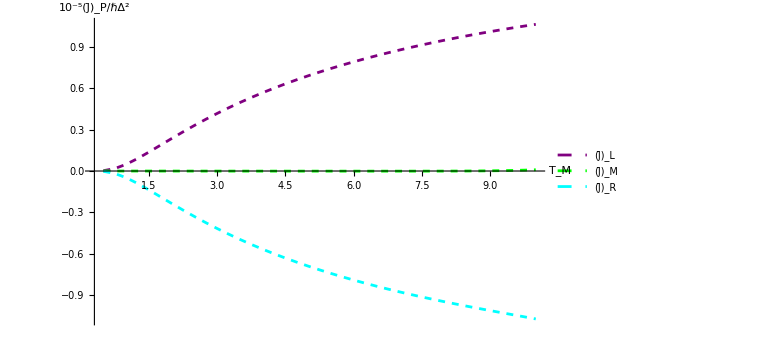

```mathematica
J2=OverBar[PlotEngyFlowsWithTM][0.5,10,0.25,10,0.2 ,1,2,3,20,20,Full]
```

#### Amplification Factor (at steady state)

```mathematica
OverBar[PlotAFWithTM][Tmin_,Tmax_,Tres_,TL_,TR_,ωL_,ωR_,ωM_,gs_,gMs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T,T,T},{T,Tmin,Tmax,Tres}];
tempy1=10^5 Table[OverBar[varEngyFunc][TL,TM,TR,ωL,ωR,ωM,gs,gMs,unitassum],{TM,Tmin,Tmax,Tres}];
tempy2=10^5 Table[OverBar[varEngyFunc][TL,TM,TR,ωL,ωR,ωM,gs,gMs,unitassum],{TM,Tmin-Tres,Tmax-Tres,Tres}];
temp=Table[MapThread[List,{tempx[[;;,1]],Abs[(tempy1[[;;,1]]-tempy2[[;;,1]])/(tempy1[[;;,2]]-tempy2[[;;,2]])]}]];
ListLogPlot[temp,AxesStyle->Directive[Black,23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T_M",23.5,FontFamily->"Times New Roman"],Style["|α_L|",23.5,FontFamily->"Times New Roman"]},Joined->True,PlotStyle->{Dashed,Thickness->Large,Pink},PlotRange->plotrange,LabelStyle->Directive[23.5,FontFamily->"Times New Roman"],ImageSize->Large]]
```

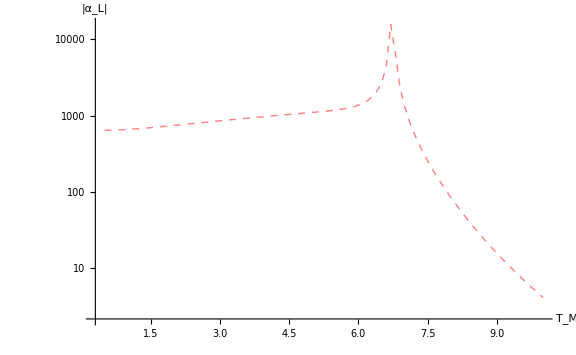

```mathematica
A2=OverBar[PlotAFWithTM][0.5,10,0.1,10,0.2 ,1,2,3,20,20,Full]
```

## Effect of g_M on transistor action

Variation in thermal flows for different g_M values

```mathematica
OverBar[varEngyFunc1][TL_,TM_,TR_,ωL_,ωR_,ωM_,gs_,gMs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,NBEassum,unitassum,μassum,κassum,OverBar[ωassum1],OverBar[ωassum2],Subscript[T, L]-> TL,Subscript[T, R]-> TR,Subscript[T, M1]-> TM,Subscript[T, M2]-> TM,Subscript[ω, L]->ωL,Subscript[ω, R]->ωR,Subscript[ω, M]->ωM,Subscript[g, LM]->gs,Subscript[g, MR]->gs,Subscript[g, M]->gMs}];
temp1=N[OverBar[sol]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ̄, i_,j_]'[t]-> 0,Subscript[ρ̄, i_,j_][t]-> Subscript[ρ̄, i,j]},1==∑_(i=1)^16 Subscript[ρ̄, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ̄, i,j],{i,1,16},{j,1,16}]]]]];
Re[Flatten[{Subscript[J̄, L]}//.Flatten[{Subscript[ρ̄, i_,j_][t]->Subscript[ρ̄, i,j],temp0}]/.temp3]]]
```

```mathematica
OverBar[PlotEngyFlowsWithTMandg][Tmin_,Tmax_,Tres_,TL_,TR_,ωL_,ωR_,ωM_,gs_,gMmin_,gMmax_,gMres_]:= 
Module[{tempx,tempy,tempz,temp},
tempx=Table[T,{T,Tmin,Tmax,Tres},{gMs,gMmin,gMmax,gMres}];
tempy=Table[gMs,{T,Tmin,Tmax,Tres},{gMs,gMmin,gMmax,gMres}];
tempz=10^5 Table[OverBar[varEngyFunc1][TL,TM,TR,ωL,ωR,ωM,gs,gMs,unitassum],{TM,Tmin,Tmax,Tres},{gMs,gMmin,gMmax,gMres}];
temp=MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[tempz][[;;]]}];
ListPlot3D[temp,PlotRange->{{Tmin,Tmax},{gMmin,gMmax},Full},
ImageSize->Large,
AxesLabel->{
		Style["T_M",FontFamily->"Times New Roman",FontSize->19.5],
		Style["g_M",FontFamily->"Times New Roman",FontSize->19.5],
      Style["J_L",FontFamily->"Times New Roman",FontSize->19.5]},
	ColorFunction->"RoseColors"]]
```

```mathematica
OverBar[PlotEngyFlowsWithTMandg][0.5,10,0.25,10,0.2 ,1,2,3,20,5,25,1]
```

-Graphics3D-

```mathematica
OverBar[PlotAFWithTMandg][Tmin_,Tmax_,Tres_,TL_,TR_,ωL_,ωR_,ωM_,gs_,gMmin_,gMmax_,gMres_]:= 
Module[{tempx,tempy,tempz1,tempz2,temp},
tempx=Table[T,{T,Tmin,Tmax,Tres},{gMs,gMmin,gMmax,gMres}];
tempy=Table[gMs,{T,Tmin,Tmax,Tres},{gMs,gMmin,gMmax,gMres}];
tempz1=Quiet[10^5 Table[OverBar[varEngyFunc][TL,TM,TR,ωL,ωR,ωM,gs,gMs,unitassum],{TM,Tmin,Tmax,Tres},{gMs,gMmin,gMmax,gMres}]];
tempz2=Quiet[10^5 Table[OverBar[varEngyFunc][TL,TM,TR,ωL,ωR,ωM,gs,gMs,unitassum],{TM,Tmin-Tres,Tmax-Tres,Tres},{gMs,gMmin,gMmax,gMres}]];
temp=Table[MapThread[List,{Flatten[tempx][[;;]],Flatten[tempy][[;;]],Flatten[Abs[(tempz1[[;;,;;,1]]-tempz2[[;;,;;,1]])/(tempz1[[;;,;;,2]]-tempz2[[;;,;;,2]])]]}]];
min=Min[temp];
max=Max[temp];
ListPlot3D[temp,ScalingFunctions->{"Linear","Linear","Log10"},PlotRange->{{Tmin,Tmax},{gMmin,gMmax},Full},ImageSize->Large,AxesStyle->Directive[Black,23.5,FontFamily->"Times New Roman"],
AxesLabel->{
		Style["T_M",FontFamily->"Times New Roman",FontSize->23.5],
		Style["g_M",FontFamily->"Times New Roman",FontSize->23.5],
      Style["α",FontFamily->"Times New Roman",FontSize->23.5]},
	ColorFunction->"BlueGreenYellow",ViewPoint->Top,PlotLegends->BarLegend["BlueGreenYellow",{min,max}]]]
```

```mathematica
AmpFactor11=OverBar[PlotAFWithTMandg][0.5,10,0.5,10,0.2 ,1,2,3,20,10,30,0.5]
```

-Graphics3D-

```mathematica
AmpFactor1=-Graphics3D-;
```

```mathematica
Show[AmpFactor1,ViewPoint->{0,0,Infinity},Axes->{True,True,False}]
```

-Graphics3D-

## Comparing two models

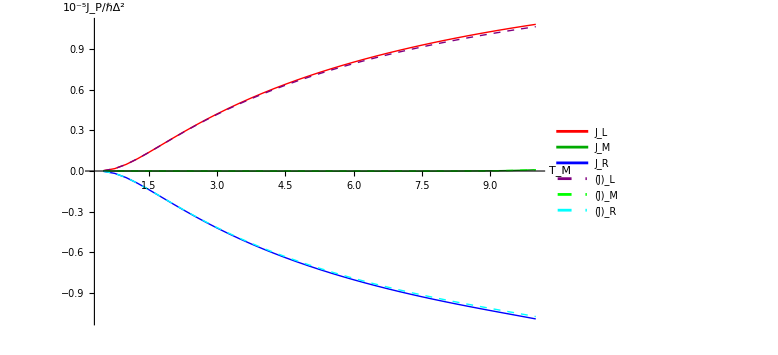

```mathematica
C1=Show[J1,J2]
```

```mathematica
Export["thermalFlows.pdf",C1,"PDF","AllowRasterization"->False];
```

```mathematica
C2=Show[A1,A2]
```

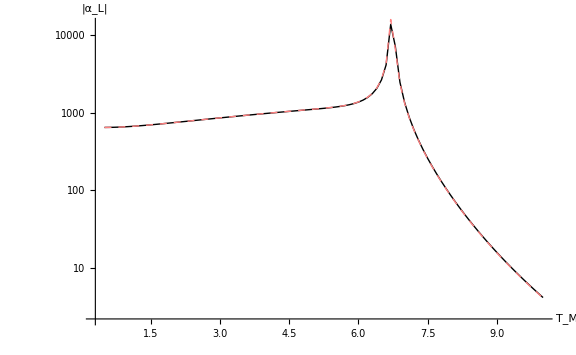

```mathematica
Export["AmplificationFactor.pdf",C2,"PDF","AllowRasterization"->False];
```

## Diode Characteristics

System Hamiltonians

Diode D1

```mathematica
Subscript[H, D1]=KroneckerProduct[Subscript[H, L],Subscript[σ, I]]+KroneckerProduct[Subscript[σ, I],Subscript[H, M1]]+Subscript[g, LM]*KroneckerProduct[Subscript[σ, z],Subscript[σ, z]];
MatrixForm[Subscript[H, D1]]
```

(g_LM+ℏ ω_L+ℏ ω_M | 0 | 0 | 0
0 | -g_LM+ℏ ω_L | 0 | 0
0 | 0 | -g_LM+ℏ ω_M | 0
0 | 0 | 0 | g_LM)

Diode D2

```mathematica
Subscript[H, D2]=KroneckerProduct[Subscript[H, M2],Subscript[σ, I]]+KroneckerProduct[Subscript[σ, I],Subscript[H, R]]+Subscript[g, MR]*KroneckerProduct[Subscript[σ, z],Subscript[σ, z]];
MatrixForm[Subscript[H, D1]]
```

(g_LM+ℏ ω_L+ℏ ω_M | 0 | 0 | 0
0 | -g_LM+ℏ ω_L | 0 | 0
0 | 0 | -g_LM+ℏ ω_M | 0
0 | 0 | 0 | g_LM)

Energy states of the diodes

Diode D1

```mathematica
{EvalD1,EvecD1}=Eigensystem[Subscript[H, D1]];
```

```mathematica
listD11=Partition[Riffle[EvalD1,EvecD1],2];
listD12=Sort[listD11,OrderedQ[{#1[[2]],#2[[2]]}]&];
listD12//MatrixForm
```

(g_LM | {0,0,0,1}
-g_LM+ℏ ω_M | {0,0,1,0}
-g_LM+ℏ ω_L | {0,1,0,0}
g_LM+ℏ ω_L+ℏ ω_M | {1,0,0,0})

Diode D2

```mathematica
{EvalD2,EvecD2}=Eigensystem[Subscript[H, D2]];
```

```mathematica
listD21=Partition[Riffle[EvalD2,EvecD2],2];
listD22=Sort[listD21,OrderedQ[{#1[[2]],#2[[2]]}]&];
listD22//MatrixForm
```

(g_MR | {0,0,0,1}
-g_MR+ℏ ω_R | {0,0,1,0}
-g_MR+ℏ ω_M | {0,1,0,0}
g_MR+ℏ ω_M+ℏ ω_R | {1,0,0,0})

Eigenvalues in matrix form

Diode D1

```mathematica
Subscript[S, D1,i_,j_]:=Flatten[KroneckerProduct[Subscript[z, i],Subscript[z, j]]]
```

```mathematica
Subscript[E, D1,i_,j_]:=First[Select[listD11,#[[2]]==Subscript[S, D1,i,j]&]][[1]]
```

```mathematica
Subscript[HsEVal, D1]=Reverse[Flatten[Table[Subscript[E, D1,i,j],{i,0,1},{j,0,1}]]]//MatrixForm
```

(g_LM+ℏ ω_L+ℏ ω_M
-g_LM+ℏ ω_L
-g_LM+ℏ ω_M
g_LM)

```mathematica
Subscript[λ, D1,1]=Transpose[{{1,0,0,0}}];
Subscript[λ, D1,2]=Transpose[{{0,1,0,0}}];
Subscript[λ, D1,3]=Transpose[{{0,0,1,0}}];
Subscript[λ, D1,4]=Transpose[{{0,0,0,1}}];
```

Diode D2

```mathematica
Subscript[S, D2,i_,j_]:=Flatten[KroneckerProduct[Subscript[z, i],Subscript[z, j]]]
```

```mathematica
Subscript[E, D2,i_,j_]:=First[Select[listD21,#[[2]]==Subscript[S, D2,i,j]&]][[1]]
```

```mathematica
Subscript[HsEVal, D2]=Reverse[Flatten[Table[Subscript[E, D2,i,j],{i,0,1},{j,0,1}]]]//MatrixForm
```

(g_MR+ℏ ω_M+ℏ ω_R
-g_MR+ℏ ω_M
-g_MR+ℏ ω_R
g_MR)

```mathematica
Subscript[λ, D2,1]=Transpose[{{1,0,0,0}}];
Subscript[λ, D2,2]=Transpose[{{0,1,0,0}}];
Subscript[λ, D2,3]=Transpose[{{0,0,1,0}}];
Subscript[λ, D2,4]=Transpose[{{0,0,0,1}}];
```

Jump Operators

Diode D1

```mathematica
Subscript[S, L]=Subscript[z, 1].Subscript[z, 0] ᵀ+Subscript[z, 0].Subscript[z, 1] ᵀ;
Subscript[𝕊, D1,L]=KroneckerProduct[Subscript[S, L],Subscript[σ, I]];
Subscript[S, M1]=Subscript[z, 1].Subscript[z, 0] ᵀ+Subscript[z, 0].Subscript[z, 1] ᵀ;
Subscript[𝕊, D1,M1]=KroneckerProduct[Subscript[σ, I],Subscript[S, M1]];
```

Diode D2

```mathematica
Subscript[S, M2]=Subscript[z, 1].Subscript[z, 0] ᵀ+Subscript[z, 0].Subscript[z, 1] ᵀ;
Subscript[𝕊, D2,M2]=KroneckerProduct[Subscript[S, M2],Subscript[σ, I]];
Subscript[S, R]=Subscript[z, 1].Subscript[z, 0] ᵀ+Subscript[z, 0].Subscript[z, 1] ᵀ;
Subscript[𝕊, D2,R]=KroneckerProduct[Subscript[σ, I],Subscript[S, R]];
```

```mathematica
Subscript[πMatrix, d_,i_] := Subscript[λ, d,i].Subscript[λ, d,i] ᵀ
Subscript[SMatrix, d_,α_,Subscript[ω, d_,j_,i_]]:= Subscript[πMatrix, d,i].Subscript[𝕊, d,α].Subscript[πMatrix, d,j]
```

Density Matrix

Diode D1

```mathematica
Subscript[ρMatrix, D1][t]=Table[Subscript[ρ, D1,i,j][t],{i,1,4},{j,1,4}];
MatrixForm[%]
```

(ρ_(D1,1,1)[t] | ρ_(D1,1,2)[t] | ρ_(D1,1,3)[t] | ρ_(D1,1,4)[t]
ρ_(D1,2,1)[t] | ρ_(D1,2,2)[t] | ρ_(D1,2,3)[t] | ρ_(D1,2,4)[t]
ρ_(D1,3,1)[t] | ρ_(D1,3,2)[t] | ρ_(D1,3,3)[t] | ρ_(D1,3,4)[t]
ρ_(D1,4,1)[t] | ρ_(D1,4,2)[t] | ρ_(D1,4,3)[t] | ρ_(D1,4,4)[t])

Diode D2

```mathematica
Subscript[ρMatrix, D2][t]=Table[Subscript[ρ, D2,i,j][t],{i,1,4},{j,1,4}];
MatrixForm[%]
```

(ρ_(D2,1,1)[t] | ρ_(D2,1,2)[t] | ρ_(D2,1,3)[t] | ρ_(D2,1,4)[t]
ρ_(D2,2,1)[t] | ρ_(D2,2,2)[t] | ρ_(D2,2,3)[t] | ρ_(D2,2,4)[t]
ρ_(D2,3,1)[t] | ρ_(D2,3,2)[t] | ρ_(D2,3,3)[t] | ρ_(D2,3,4)[t]
ρ_(D2,4,1)[t] | ρ_(D2,4,2)[t] | ρ_(D2,4,3)[t] | ρ_(D2,4,4)[t])

Possible Transition Frequencies

Diode D1

```mathematica
Subscript[ωMatrix, D1]={Flatten[Table[Subscript[ω, D1,i,j],{i,1,4},{j,i+1,4}]]}
```

{{ω_(D1,1,2),ω_(D1,1,3),ω_(D1,1,4),ω_(D1,2,3),ω_(D1,2,4),ω_(D1,3,4)}}

```mathematica
Subscript[ωVals, D1]=Flatten[Simplify[Table[(Subscript[HsEVal, D1][[1,i]]-Subscript[HsEVal, D1][[1,j]])/ℏ,{i,1,4},{j,i+1,4}]]];
```

Diode D2

```mathematica
Subscript[ωMatrix, D2]={Flatten[Table[Subscript[ω, D2,i,j],{i,1,4},{j,i+1,4}]]}
```

{{ω_(D2,1,2),ω_(D2,1,3),ω_(D2,1,4),ω_(D2,2,3),ω_(D2,2,4),ω_(D2,3,4)}}

```mathematica
Subscript[ωVals, D2]=Flatten[Simplify[Table[(Subscript[HsEVal, D2][[1,i]]-Subscript[HsEVal, D2][[1,j]])/ℏ,{i,1,4},{j,i+1,4}]]];
```

Lindblad Super Operator

```mathematica
Subscript[ℒ, d_,P_]:=Subscript[ℒ, d,P]=∑_(γ=1)^6 (Subscript[𝒥, P][Part[Subscript[ωMatrix, d],1,γ]](1+Subscript[n, P][Part[Subscript[ωMatrix, d],1,γ]])(Subscript[SMatrix, d,P,Part[Subscript[ωMatrix, d],1,γ]].Subscript[ρMatrix, d][t].Subscript[SMatrix, d,P,Part[Subscript[ωMatrix, d],1,γ]] ᵀ-1/2 Subscript[SMatrix, d,P,Part[Subscript[ωMatrix, d],1,γ]] ᵀ.Subscript[SMatrix, d,P,Part[Subscript[ωMatrix, d],1,γ]].Subscript[ρMatrix, d][t]-1/2 Subscript[ρMatrix, d][t].Subscript[SMatrix, d,P,Part[Subscript[ωMatrix, d],1,γ]] ᵀ.Subscript[SMatrix, d,P,Part[Subscript[ωMatrix, d],1,γ]])+(Subscript[𝒥, P][Part[Subscript[ωMatrix, d],1,γ]] Subscript[n, P][Part[Subscript[ωMatrix, d],1,γ]](Subscript[SMatrix, d,P,Part[Subscript[ωMatrix, d],1,γ]] ᵀ.Subscript[ρMatrix, d][t].Subscript[SMatrix, d,P,Part[Subscript[ωMatrix, d],1,γ]]-1/2 Subscript[SMatrix, d,P,Part[Subscript[ωMatrix, d],1,γ]].Subscript[SMatrix, d,P,Part[Subscript[ωMatrix, d],1,γ]] ᵀ.Subscript[ρMatrix, d][t]-1/2 Subscript[ρMatrix, d][t].Subscript[SMatrix, d,P,Part[Subscript[ωMatrix, d],1,γ]].Subscript[SMatrix, d,P,Part[Subscript[ωMatrix, d],1,γ]] ᵀ)));
```

Master Equation

Diode D1

```mathematica
Subscript[dρ, D1]=MatrixForm[Subscript[ℒ, D1,L]+Subscript[ℒ, D1,M1]-(ⅈ/ℏ(Subscript[H, D1].Subscript[ρMatrix, D1][t]-Subscript[ρMatrix, D1][t].Subscript[H, D1]))]//.{-Subscript[n, P_][Subscript[ω, d_,j_,i_]]Subscript[𝒥, P_][Subscript[ω, d_,j_,i_]]Subscript[ρ, d_,i_,i_][t] +(1+Subscript[n, P_][Subscript[ω, d_,j_,i_]])Subscript[𝒥, P_][Subscript[ω, d_,j_,i_]]Subscript[ρ, d_,j_,j_][t]:>Subscript[Γ, d,P,j,i],Subscript[n, P_][Subscript[ω, d_,j_,i_]]Subscript[𝒥, P_][Subscript[ω, d_,j_,i_]]Subscript[ρ, d_,i_,i_][t] -(1+Subscript[n, P_][Subscript[ω, d_,j_,i_]])Subscript[𝒥, P_][Subscript[ω, d_,j_,i_]]Subscript[ρ, d_,j_,j_][t]:>-Subscript[Γ, d,P,j,i]};
```

```mathematica
MatrixForm[%]
```

(-Γ_(D1,L,1,3)-Γ_(D1,M1,1,2) | -1/2 (1+n_L[ω_(D1,1,3)]) 𝒥_L[ω_(D1,1,3)] ρ_(D1,1,2)[t]-1/2 (1+n_L[ω_(D1,2,4)]) 𝒥_L[ω_(D1,2,4)] ρ_(D1,1,2)[t]-1/2 n_M1[ω_(D1,1,2)] 𝒥_M1[ω_(D1,1,2)] ρ_(D1,1,2)[t]-1/2 (1+n_M1[ω_(D1,1,2)]) 𝒥_M1[ω_(D1,1,2)] ρ_(D1,1,2)[t]-(ⅈ (-((-g_LM+ℏ ω_L) ρ_(D1,1,2)[t])+(g_LM+ℏ ω_L+ℏ ω_M) ρ_(D1,1,2)[t]))/ℏ | -1/2 n_L[ω_(D1,1,3)] 𝒥_L[ω_(D1,1,3)] ρ_(D1,1,3)[t]-1/2 (1+n_L[ω_(D1,1,3)]) 𝒥_L[ω_(D1,1,3)] ρ_(D1,1,3)[t]-1/2 (1+n_M1[ω_(D1,1,2)]) 𝒥_M1[ω_(D1,1,2)] ρ_(D1,1,3)[t]-1/2 (1+n_M1[ω_(D1,3,4)]) 𝒥_M1[ω_(D1,3,4)] ρ_(D1,1,3)[t]-(ⅈ (-((-g_LM+ℏ ω_M) ρ_(D1,1,3)[t])+(g_LM+ℏ ω_L+ℏ ω_M) ρ_(D1,1,3)[t]))/ℏ | -1/2 (1+n_L[ω_(D1,1,3)]) 𝒥_L[ω_(D1,1,3)] ρ_(D1,1,4)[t]-1/2 n_L[ω_(D1,2,4)] 𝒥_L[ω_(D1,2,4)] ρ_(D1,1,4)[t]-1/2 (1+n_M1[ω_(D1,1,2)]) 𝒥_M1[ω_(D1,1,2)] ρ_(D1,1,4)[t]-1/2 n_M1[ω_(D1,3,4)] 𝒥_M1[ω_(D1,3,4)] ρ_(D1,1,4)[t]-(ⅈ (-g_LM ρ_(D1,1,4)[t]+(g_LM+ℏ ω_L+ℏ ω_M) ρ_(D1,1,4)[t]))/ℏ
-1/2 (1+n_L[ω_(D1,1,3)]) 𝒥_L[ω_(D1,1,3)] ρ_(D1,2,1)[t]-1/2 (1+n_L[ω_(D1,2,4)]) 𝒥_L[ω_(D1,2,4)] ρ_(D1,2,1)[t]-1/2 n_M1[ω_(D1,1,2)] 𝒥_M1[ω_(D1,1,2)] ρ_(D1,2,1)[t]-1/2 (1+n_M1[ω_(D1,1,2)]) 𝒥_M1[ω_(D1,1,2)] ρ_(D1,2,1)[t]-(ⅈ ((-g_LM+ℏ ω_L) ρ_(D1,2,1)[t]-(g_LM+ℏ ω_L+ℏ ω_M) ρ_(D1,2,1)[t]))/ℏ | -Γ_(D1,L,2,4)+Γ_(D1,M1,1,2) | -1/2 n_L[ω_(D1,1,3)] 𝒥_L[ω_(D1,1,3)] ρ_(D1,2,3)[t]-1/2 (1+n_L[ω_(D1,2,4)]) 𝒥_L[ω_(D1,2,4)] ρ_(D1,2,3)[t]-1/2 n_M1[ω_(D1,1,2)] 𝒥_M1[ω_(D1,1,2)] ρ_(D1,2,3)[t]-1/2 (1+n_M1[ω_(D1,3,4)]) 𝒥_M1[ω_(D1,3,4)] ρ_(D1,2,3)[t]-(ⅈ ((-g_LM+ℏ ω_L) ρ_(D1,2,3)[t]-(-g_LM+ℏ ω_M) ρ_(D1,2,3)[t]))/ℏ | -1/2 n_L[ω_(D1,2,4)] 𝒥_L[ω_(D1,2,4)] ρ_(D1,2,4)[t]-1/2 (1+n_L[ω_(D1,2,4)]) 𝒥_L[ω_(D1,2,4)] ρ_(D1,2,4)[t]-1/2 n_M1[ω_(D1,1,2)] 𝒥_M1[ω_(D1,1,2)] ρ_(D1,2,4)[t]-1/2 n_M1[ω_(D1,3,4)] 𝒥_M1[ω_(D1,3,4)] ρ_(D1,2,4)[t]-(ⅈ (-g_LM ρ_(D1,2,4)[t]+(-g_LM+ℏ ω_L) ρ_(D1,2,4)[t]))/ℏ
-1/2 n_L[ω_(D1,1,3)] 𝒥_L[ω_(D1,1,3)] ρ_(D1,3,1)[t]-1/2 (1+n_L[ω_(D1,1,3)]) 𝒥_L[ω_(D1,1,3)] ρ_(D1,3,1)[t]-1/2 (1+n_M1[ω_(D1,1,2)]) 𝒥_M1[ω_(D1,1,2)] ρ_(D1,3,1)[t]-1/2 (1+n_M1[ω_(D1,3,4)]) 𝒥_M1[ω_(D1,3,4)] ρ_(D1,3,1)[t]-(ⅈ ((-g_LM+ℏ ω_M) ρ_(D1,3,1)[t]-(g_LM+ℏ ω_L+ℏ ω_M) ρ_(D1,3,1)[t]))/ℏ | -1/2 n_L[ω_(D1,1,3)] 𝒥_L[ω_(D1,1,3)] ρ_(D1,3,2)[t]-1/2 (1+n_L[ω_(D1,2,4)]) 𝒥_L[ω_(D1,2,4)] ρ_(D1,3,2)[t]-1/2 n_M1[ω_(D1,1,2)] 𝒥_M1[ω_(D1,1,2)] ρ_(D1,3,2)[t]-1/2 (1+n_M1[ω_(D1,3,4)]) 𝒥_M1[ω_(D1,3,4)] ρ_(D1,3,2)[t]-(ⅈ (-((-g_LM+ℏ ω_L) ρ_(D1,3,2)[t])+(-g_LM+ℏ ω_M) ρ_(D1,3,2)[t]))/ℏ | Γ_(D1,L,1,3)-Γ_(D1,M1,3,4) | -1/2 n_L[ω_(D1,1,3)] 𝒥_L[ω_(D1,1,3)] ρ_(D1,3,4)[t]-1/2 n_L[ω_(D1,2,4)] 𝒥_L[ω_(D1,2,4)] ρ_(D1,3,4)[t]-1/2 n_M1[ω_(D1,3,4)] 𝒥_M1[ω_(D1,3,4)] ρ_(D1,3,4)[t]-1/2 (1+n_M1[ω_(D1,3,4)]) 𝒥_M1[ω_(D1,3,4)] ρ_(D1,3,4)[t]-(ⅈ (-g_LM ρ_(D1,3,4)[t]+(-g_LM+ℏ ω_M) ρ_(D1,3,4)[t]))/ℏ
-1/2 (1+n_L[ω_(D1,1,3)]) 𝒥_L[ω_(D1,1,3)] ρ_(D1,4,1)[t]-1/2 n_L[ω_(D1,2,4)] 𝒥_L[ω_(D1,2,4)] ρ_(D1,4,1)[t]-1/2 (1+n_M1[ω_(D1,1,2)]) 𝒥_M1[ω_(D1,1,2)] ρ_(D1,4,1)[t]-1/2 n_M1[ω_(D1,3,4)] 𝒥_M1[ω_(D1,3,4)] ρ_(D1,4,1)[t]-(ⅈ (g_LM ρ_(D1,4,1)[t]-(g_LM+ℏ ω_L+ℏ ω_M) ρ_(D1,4,1)[t]))/ℏ | -1/2 n_L[ω_(D1,2,4)] 𝒥_L[ω_(D1,2,4)] ρ_(D1,4,2)[t]-1/2 (1+n_L[ω_(D1,2,4)]) 𝒥_L[ω_(D1,2,4)] ρ_(D1,4,2)[t]-1/2 n_M1[ω_(D1,1,2)] 𝒥_M1[ω_(D1,1,2)] ρ_(D1,4,2)[t]-1/2 n_M1[ω_(D1,3,4)] 𝒥_M1[ω_(D1,3,4)] ρ_(D1,4,2)[t]-(ⅈ (g_LM ρ_(D1,4,2)[t]-(-g_LM+ℏ ω_L) ρ_(D1,4,2)[t]))/ℏ | -1/2 n_L[ω_(D1,1,3)] 𝒥_L[ω_(D1,1,3)] ρ_(D1,4,3)[t]-1/2 n_L[ω_(D1,2,4)] 𝒥_L[ω_(D1,2,4)] ρ_(D1,4,3)[t]-1/2 n_M1[ω_(D1,3,4)] 𝒥_M1[ω_(D1,3,4)] ρ_(D1,4,3)[t]-1/2 (1+n_M1[ω_(D1,3,4)]) 𝒥_M1[ω_(D1,3,4)] ρ_(D1,4,3)[t]-(ⅈ (g_LM ρ_(D1,4,3)[t]-(-g_LM+ℏ ω_M) ρ_(D1,4,3)[t]))/ℏ | Γ_(D1,L,2,4)+Γ_(D1,M1,3,4))

Diode D2

```mathematica
Subscript[dρ, D2]=MatrixForm[Subscript[ℒ, D2,M2]+Subscript[ℒ, D2,R]-(ⅈ/ℏ(Subscript[H, D2].Subscript[ρMatrix, D2][t]-Subscript[ρMatrix, D2][t].Subscript[H, D2]))]//.{-Subscript[n, P_][Subscript[ω, d_,j_,i_]]Subscript[𝒥, P_][Subscript[ω, d_,j_,i_]]Subscript[ρ, d_,i_,i_][t] +(1+Subscript[n, P_][Subscript[ω, d_,j_,i_]])Subscript[𝒥, P_][Subscript[ω, d_,j_,i_]]Subscript[ρ, d_,j_,j_][t]:>Subscript[Γ, d,P,j,i],Subscript[n, P_][Subscript[ω, d_,j_,i_]]Subscript[𝒥, P_][Subscript[ω, d_,j_,i_]]Subscript[ρ, d_,i_,i_][t] -(1+Subscript[n, P_][Subscript[ω, d_,j_,i_]])Subscript[𝒥, P_][Subscript[ω, d_,j_,i_]]Subscript[ρ, d_,j_,j_][t]:>-Subscript[Γ, d,P,j,i]};
```

```mathematica
MatrixForm[%]
```

(-Γ_(D2,M2,1,3)-Γ_(D2,R,1,2) | -1/2 (1+n_M2[ω_(D2,1,3)]) 𝒥_M2[ω_(D2,1,3)] ρ_(D2,1,2)[t]-1/2 (1+n_M2[ω_(D2,2,4)]) 𝒥_M2[ω_(D2,2,4)] ρ_(D2,1,2)[t]-1/2 n_R[ω_(D2,1,2)] 𝒥_R[ω_(D2,1,2)] ρ_(D2,1,2)[t]-1/2 (1+n_R[ω_(D2,1,2)]) 𝒥_R[ω_(D2,1,2)] ρ_(D2,1,2)[t]-(ⅈ (-((-g_MR+ℏ ω_M) ρ_(D2,1,2)[t])+(g_MR+ℏ ω_M+ℏ ω_R) ρ_(D2,1,2)[t]))/ℏ | -1/2 n_M2[ω_(D2,1,3)] 𝒥_M2[ω_(D2,1,3)] ρ_(D2,1,3)[t]-1/2 (1+n_M2[ω_(D2,1,3)]) 𝒥_M2[ω_(D2,1,3)] ρ_(D2,1,3)[t]-1/2 (1+n_R[ω_(D2,1,2)]) 𝒥_R[ω_(D2,1,2)] ρ_(D2,1,3)[t]-1/2 (1+n_R[ω_(D2,3,4)]) 𝒥_R[ω_(D2,3,4)] ρ_(D2,1,3)[t]-(ⅈ (-((-g_MR+ℏ ω_R) ρ_(D2,1,3)[t])+(g_MR+ℏ ω_M+ℏ ω_R) ρ_(D2,1,3)[t]))/ℏ | -1/2 (1+n_M2[ω_(D2,1,3)]) 𝒥_M2[ω_(D2,1,3)] ρ_(D2,1,4)[t]-1/2 n_M2[ω_(D2,2,4)] 𝒥_M2[ω_(D2,2,4)] ρ_(D2,1,4)[t]-1/2 (1+n_R[ω_(D2,1,2)]) 𝒥_R[ω_(D2,1,2)] ρ_(D2,1,4)[t]-1/2 n_R[ω_(D2,3,4)] 𝒥_R[ω_(D2,3,4)] ρ_(D2,1,4)[t]-(ⅈ (-g_MR ρ_(D2,1,4)[t]+(g_MR+ℏ ω_M+ℏ ω_R) ρ_(D2,1,4)[t]))/ℏ
-1/2 (1+n_M2[ω_(D2,1,3)]) 𝒥_M2[ω_(D2,1,3)] ρ_(D2,2,1)[t]-1/2 (1+n_M2[ω_(D2,2,4)]) 𝒥_M2[ω_(D2,2,4)] ρ_(D2,2,1)[t]-1/2 n_R[ω_(D2,1,2)] 𝒥_R[ω_(D2,1,2)] ρ_(D2,2,1)[t]-1/2 (1+n_R[ω_(D2,1,2)]) 𝒥_R[ω_(D2,1,2)] ρ_(D2,2,1)[t]-(ⅈ ((-g_MR+ℏ ω_M) ρ_(D2,2,1)[t]-(g_MR+ℏ ω_M+ℏ ω_R) ρ_(D2,2,1)[t]))/ℏ | -Γ_(D2,M2,2,4)+Γ_(D2,R,1,2) | -1/2 n_M2[ω_(D2,1,3)] 𝒥_M2[ω_(D2,1,3)] ρ_(D2,2,3)[t]-1/2 (1+n_M2[ω_(D2,2,4)]) 𝒥_M2[ω_(D2,2,4)] ρ_(D2,2,3)[t]-1/2 n_R[ω_(D2,1,2)] 𝒥_R[ω_(D2,1,2)] ρ_(D2,2,3)[t]-1/2 (1+n_R[ω_(D2,3,4)]) 𝒥_R[ω_(D2,3,4)] ρ_(D2,2,3)[t]-(ⅈ ((-g_MR+ℏ ω_M) ρ_(D2,2,3)[t]-(-g_MR+ℏ ω_R) ρ_(D2,2,3)[t]))/ℏ | -1/2 n_M2[ω_(D2,2,4)] 𝒥_M2[ω_(D2,2,4)] ρ_(D2,2,4)[t]-1/2 (1+n_M2[ω_(D2,2,4)]) 𝒥_M2[ω_(D2,2,4)] ρ_(D2,2,4)[t]-1/2 n_R[ω_(D2,1,2)] 𝒥_R[ω_(D2,1,2)] ρ_(D2,2,4)[t]-1/2 n_R[ω_(D2,3,4)] 𝒥_R[ω_(D2,3,4)] ρ_(D2,2,4)[t]-(ⅈ (-g_MR ρ_(D2,2,4)[t]+(-g_MR+ℏ ω_M) ρ_(D2,2,4)[t]))/ℏ
-1/2 n_M2[ω_(D2,1,3)] 𝒥_M2[ω_(D2,1,3)] ρ_(D2,3,1)[t]-1/2 (1+n_M2[ω_(D2,1,3)]) 𝒥_M2[ω_(D2,1,3)] ρ_(D2,3,1)[t]-1/2 (1+n_R[ω_(D2,1,2)]) 𝒥_R[ω_(D2,1,2)] ρ_(D2,3,1)[t]-1/2 (1+n_R[ω_(D2,3,4)]) 𝒥_R[ω_(D2,3,4)] ρ_(D2,3,1)[t]-(ⅈ ((-g_MR+ℏ ω_R) ρ_(D2,3,1)[t]-(g_MR+ℏ ω_M+ℏ ω_R) ρ_(D2,3,1)[t]))/ℏ | -1/2 n_M2[ω_(D2,1,3)] 𝒥_M2[ω_(D2,1,3)] ρ_(D2,3,2)[t]-1/2 (1+n_M2[ω_(D2,2,4)]) 𝒥_M2[ω_(D2,2,4)] ρ_(D2,3,2)[t]-1/2 n_R[ω_(D2,1,2)] 𝒥_R[ω_(D2,1,2)] ρ_(D2,3,2)[t]-1/2 (1+n_R[ω_(D2,3,4)]) 𝒥_R[ω_(D2,3,4)] ρ_(D2,3,2)[t]-(ⅈ (-((-g_MR+ℏ ω_M) ρ_(D2,3,2)[t])+(-g_MR+ℏ ω_R) ρ_(D2,3,2)[t]))/ℏ | Γ_(D2,M2,1,3)-Γ_(D2,R,3,4) | -1/2 n_M2[ω_(D2,1,3)] 𝒥_M2[ω_(D2,1,3)] ρ_(D2,3,4)[t]-1/2 n_M2[ω_(D2,2,4)] 𝒥_M2[ω_(D2,2,4)] ρ_(D2,3,4)[t]-1/2 n_R[ω_(D2,3,4)] 𝒥_R[ω_(D2,3,4)] ρ_(D2,3,4)[t]-1/2 (1+n_R[ω_(D2,3,4)]) 𝒥_R[ω_(D2,3,4)] ρ_(D2,3,4)[t]-(ⅈ (-g_MR ρ_(D2,3,4)[t]+(-g_MR+ℏ ω_R) ρ_(D2,3,4)[t]))/ℏ
-1/2 (1+n_M2[ω_(D2,1,3)]) 𝒥_M2[ω_(D2,1,3)] ρ_(D2,4,1)[t]-1/2 n_M2[ω_(D2,2,4)] 𝒥_M2[ω_(D2,2,4)] ρ_(D2,4,1)[t]-1/2 (1+n_R[ω_(D2,1,2)]) 𝒥_R[ω_(D2,1,2)] ρ_(D2,4,1)[t]-1/2 n_R[ω_(D2,3,4)] 𝒥_R[ω_(D2,3,4)] ρ_(D2,4,1)[t]-(ⅈ (g_MR ρ_(D2,4,1)[t]-(g_MR+ℏ ω_M+ℏ ω_R) ρ_(D2,4,1)[t]))/ℏ | -1/2 n_M2[ω_(D2,2,4)] 𝒥_M2[ω_(D2,2,4)] ρ_(D2,4,2)[t]-1/2 (1+n_M2[ω_(D2,2,4)]) 𝒥_M2[ω_(D2,2,4)] ρ_(D2,4,2)[t]-1/2 n_R[ω_(D2,1,2)] 𝒥_R[ω_(D2,1,2)] ρ_(D2,4,2)[t]-1/2 n_R[ω_(D2,3,4)] 𝒥_R[ω_(D2,3,4)] ρ_(D2,4,2)[t]-(ⅈ (g_MR ρ_(D2,4,2)[t]-(-g_MR+ℏ ω_M) ρ_(D2,4,2)[t]))/ℏ | -1/2 n_M2[ω_(D2,1,3)] 𝒥_M2[ω_(D2,1,3)] ρ_(D2,4,3)[t]-1/2 n_M2[ω_(D2,2,4)] 𝒥_M2[ω_(D2,2,4)] ρ_(D2,4,3)[t]-1/2 n_R[ω_(D2,3,4)] 𝒥_R[ω_(D2,3,4)] ρ_(D2,4,3)[t]-1/2 (1+n_R[ω_(D2,3,4)]) 𝒥_R[ω_(D2,3,4)] ρ_(D2,4,3)[t]-(ⅈ (g_MR ρ_(D2,4,3)[t]-(-g_MR+ℏ ω_R) ρ_(D2,4,3)[t]))/ℏ | Γ_(D2,M2,2,4)+Γ_(D2,R,3,4))

Thermal Energy Flows

```mathematica
Subscript[HsMatrix, d_]:=Subscript[HsMatrix, d]=DiagonalMatrix[ℏ{Subscript[ω, d,1],Subscript[ω, d,2],Subscript[ω, d,3],Subscript[ω, d,4]}];
Subscript[J, d_,P_]:=Subscript[J, d,P]=Tr[Subscript[ℒ, d,P].Subscript[HsMatrix, d]]//.{(1+Subscript[n, Q_][Subscript[ω, D_,j_,i_]])Subscript[𝒥, Q_][Subscript[ω, D_,j_,i_]]Subscript[ρ, D_,j_,j_][t]-Subscript[n, Q_][Subscript[ω, D_,j_,i_]]Subscript[𝒥, Q_][Subscript[ω, D_,j_,i_]]Subscript[ρ, D_,i_,i_][t] :>Subscript[Γ, D,Q,j,i],Subscript[n, Q_][Subscript[ω, D_,j_,i_]]Subscript[𝒥, Q_][Subscript[ω, D_,j_,i_]]Subscript[ρ, D_,i_,i_][t] -(1+Subscript[n, Q_][Subscript[ω, D_,j_,i_]])Subscript[𝒥, Q_][Subscript[ω, D_,j_,i_]]Subscript[ρ, D_,j_,j_][t]:>-Subscript[Γ, D,Q,j,i]};
```

Diode D1

```mathematica
Subscript[J, D1,L]
Subscript[J, D1,M1]
```

-ℏ ω_(D1,1) Γ_(D1,L,1,3)+ℏ ω_(D1,3) Γ_(D1,L,1,3)-ℏ ω_(D1,2) Γ_(D1,L,2,4)+ℏ ω_(D1,4) Γ_(D1,L,2,4)

-ℏ ω_(D1,1) Γ_(D1,M1,1,2)+ℏ ω_(D1,2) Γ_(D1,M1,1,2)-ℏ ω_(D1,3) Γ_(D1,M1,3,4)+ℏ ω_(D1,4) Γ_(D1,M1,3,4)

Diode D2

```mathematica
Subscript[J, D1,L]
Subscript[J, D1,M1]
```

-ℏ ω_(D1,1) Γ_(D1,L,1,3)+ℏ ω_(D1,3) Γ_(D1,L,1,3)-ℏ ω_(D1,2) Γ_(D1,L,2,4)+ℏ ω_(D1,4) Γ_(D1,L,2,4)

-ℏ ω_(D1,1) Γ_(D1,M1,1,2)+ℏ ω_(D1,2) Γ_(D1,M1,1,2)-ℏ ω_(D1,3) Γ_(D1,M1,3,4)+ℏ ω_(D1,4) Γ_(D1,M1,3,4)

## Simulations

#### Bose - Einstein Distribution

```mathematica
NBEassum=Subscript[n, P_][ω_]-> 1/(ⅇ^((ℏ ω)/(k Subscript[T, P]))-1);
```

#### Bath Spectral Density

```mathematica
Jassum=Subscript[𝒥, P_][ω_]-> Subscript[μ, P]*Subscript[μ, P]*ω*ⅇ^((-Abs[ω])/Subscript[κ, P]);
```

Stationary State Solutions of master equation

Diode D1

```mathematica
Subscript[RHS, D1]=Subscript[ℒ, D1,L]+Subscript[ℒ, D1,M1]-(ⅈ/ℏ(Subscript[H, D1].Subscript[ρMatrix, D1][t]-Subscript[ρMatrix, D1][t].Subscript[H, D1]));
Subscript[LHS, D1]=D[Subscript[ρMatrix, D1][t], t];
Subscript[sol, D1]=Flatten[Solve[Subscript[LHS, D1]==Subscript[RHS, D1],Flatten[Table[Subscript[ρ, D1,i,j]'[t],{i,1,4},{j,1,4}]]]/.Rule->Equal];
```

Separate diagonal and off diagonal equations,

```mathematica
Subscript[soldiag, D1]=Subscript[sol, D1][[1;; ;;5]];
Subscript[soloffdiag, D1]=Delete[Subscript[sol, D1],Table[{1+5i},{i,0,3}]];
```

Off diagonal Solutions

```mathematica
Flatten[{Subscript[soloffdiag, D1]/.{Subscript[ρ, D1,i_,j_]'[t]-> 0,Subscript[ρ, D1,i_,j_][t]-> Subscript[ρ, D1,i,j]}}];
Subscript[soloffdiagstat, D1]=Solve[%,DeleteCases[Flatten[Table[Subscript[ρ, D1,i,j]-i,j Subscript[ρ, D1,i,j],{i,1,4},{j,1,4}]],0]]
```

{{ρ_(D1,1,2)→0,ρ_(D1,1,3)→0,ρ_(D1,1,4)→0,ρ_(D1,2,1)→0,ρ_(D1,2,3)→0,ρ_(D1,2,4)→0,ρ_(D1,3,1)→0,ρ_(D1,3,2)→0,ρ_(D1,3,4)→0,ρ_(D1,4,1)→0,ρ_(D1,4,2)→0,ρ_(D1,4,3)→0}}

```mathematica
Flatten[{Subscript[soloffdiag, D1]/.Subscript[ρ, D1,i_,j_][t]-> i,j Subscript[ρ, D1,i,j]}]
```

{ρ_(D1,1,2)'[t]==0,ρ_(D1,1,3)'[t]==0,ρ_(D1,1,4)'[t]==0,ρ_(D1,2,1)'[t]==0,ρ_(D1,2,3)'[t]==0,ρ_(D1,2,4)'[t]==0,ρ_(D1,3,1)'[t]==0,ρ_(D1,3,2)'[t]==0,ρ_(D1,3,4)'[t]==0,ρ_(D1,4,1)'[t]==0,ρ_(D1,4,2)'[t]==0,ρ_(D1,4,3)'[t]==0}

Diode D2

```mathematica
Subscript[RHS, D2]=Subscript[ℒ, D2,M2]+Subscript[ℒ, D2,R]-(ⅈ/ℏ(Subscript[H, D2].Subscript[ρMatrix, D2][t]-Subscript[ρMatrix, D2][t].Subscript[H, D2]));
Subscript[LHS, D2]=D[Subscript[ρMatrix, D2][t], t];
Subscript[sol, D2]=Flatten[Solve[Subscript[LHS, D2]==Subscript[RHS, D2],Flatten[Table[Subscript[ρ, D2,i,j]'[t],{i,1,4},{j,1,4}]]]/.Rule->Equal];
```

Separate diagonal and off diagonal equations,

```mathematica
Subscript[soldiag, D2]=Subscript[sol, D2][[1;; ;;5]];
Subscript[soloffdiag, D2]=Delete[Subscript[sol, D2],Table[{1+5i},{i,0,3}]];
```

Off diagonal Solutions

```mathematica
Flatten[{Subscript[soloffdiag, D2]/.{Subscript[ρ, D2,i_,j_]'[t]-> 0,Subscript[ρ, D2,i_,j_][t]-> Subscript[ρ, D2,i,j]}}];
Subscript[soloffdiagstat, D2]=Solve[%,DeleteCases[Flatten[Table[Subscript[ρ, D2,i,j]-i,j Subscript[ρ, D2,i,j],{i,1,4},{j,1,4}]],0]]
```

{{ρ_(D2,1,2)→0,ρ_(D2,1,3)→0,ρ_(D2,1,4)→0,ρ_(D2,2,1)→0,ρ_(D2,2,3)→0,ρ_(D2,2,4)→0,ρ_(D2,3,1)→0,ρ_(D2,3,2)→0,ρ_(D2,3,4)→0,ρ_(D2,4,1)→0,ρ_(D2,4,2)→0,ρ_(D2,4,3)→0}}

```mathematica
Flatten[{Subscript[soloffdiag, D2]/.Subscript[ρ, D2,i_,j_][t]-> i,j Subscript[ρ, D2,i,j]}]
```

{ρ_(D2,1,2)'[t]==0,ρ_(D2,1,3)'[t]==0,ρ_(D2,1,4)'[t]==0,ρ_(D2,2,1)'[t]==0,ρ_(D2,2,3)'[t]==0,ρ_(D2,2,4)'[t]==0,ρ_(D2,3,1)'[t]==0,ρ_(D2,3,2)'[t]==0,ρ_(D2,3,4)'[t]==0,ρ_(D2,4,1)'[t]==0,ρ_(D2,4,2)'[t]==0,ρ_(D2,4,3)'[t]==0}

Diagonal Solutions using NDSolve

Assumptions for the calculations

Diode D1

```mathematica
ωassum1D1=Flatten[{Table[Subscript[ω, D1,i,j]->(Subscript[HsEVal, D1][[1,i]]-Subscript[HsEVal, D1][[1,j]] )/ℏ,{i,1,4},{j,1,4}]}];
ωassum2D1={Table[Subscript[ω, D1,i]-> Subscript[HsEVal, D1][[1,i]]/ℏ,{i,1,4}]}
unitassum = {k-> 1,ℏ->1};
μassum=Subscript[μ, P_]->0.01;
κassum=Subscript[κ, P_]->30;
ωLconv=1;
Tconv=1;
tmax=5000000;
```

{{ω_(D1,1)→(g_LM+ℏ ω_L+ℏ ω_M)/ℏ,ω_(D1,2)→(-g_LM+ℏ ω_L)/ℏ,ω_(D1,3)→(-g_LM+ℏ ω_M)/ℏ,ω_(D1,4)→g_LM/ℏ}}

```mathematica
TassumD1={Subscript[T, L]->10Tconv,Subscript[T, M1]-> 5Tconv,Subscript[ω, L]->ωLconv,Subscript[ω, M]->3ωLconv,Subscript[g, LM]->20ωLconv};
dynamicsD1=NDSolve[Flatten[{Subscript[sol, D1]//.Flatten[{Jassum,NBEassum,TassumD1,unitassum,μassum,κassum,ωassum1D1}],Table[Subscript[ρ, D1,i,j][0]==i,j i,1 1,{i,1,4},{j,1,4}]}],Flatten[Table[Subscript[ρ, D1,i,j],{i,1,4},{j,1,4}]],{t,0,tmax}];
```

Diode D2

```mathematica
ωassum1D2=Flatten[{Table[Subscript[ω, D2,i,j]->(Subscript[HsEVal, D2][[1,i]]-Subscript[HsEVal, D2][[1,j]] )/ℏ,{i,1,4},{j,1,4}]}];
ωassum2D2={Table[Subscript[ω, D2,i]-> Subscript[HsEVal, D2][[1,i]]/ℏ,{i,1,4}]};
(*unitassum = {k-> 1.3806 10^-23,ℏ->1.0546 10^-34};*)
unitassum = {k-> 1,ℏ->1};
μassum=Subscript[μ, P_]->0.01;
κassum=Subscript[κ, P_]->30;
ωLconv=1;
Tconv=1;
tmax=50000000;
```

```mathematica
TassumD2={Subscript[T, R]->0.2Tconv,Subscript[T, M2]-> 5Tconv,Subscript[ω, R]->2ωLconv,Subscript[ω, M]->3ωLconv,Subscript[g, MR]->20ωLconv};
dynamicsD2=NDSolve[Flatten[{Subscript[sol, D2]//.Flatten[{Jassum,NBEassum,TassumD2,unitassum,μassum,κassum,ωassum1D2}],Table[Subscript[ρ, D2,i,j][0]==i,j i,1 1,{i,1,4},{j,1,4}]}],Flatten[Table[Subscript[ρ, D2,i,j],{i,1,4},{j,1,4}]],{t,0,tmax}];
```

Density Matrix Element Plots

Diode D1

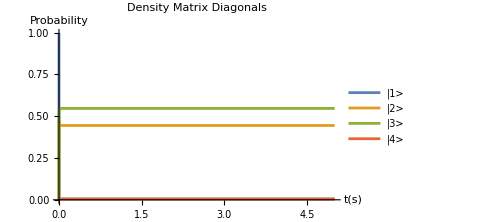

```mathematica
Flatten[{Table[Subscript[ρ, D1,i,i][t],{i,1,4}]}/.dynamicsD1];
Plot[%,{t,0,tmax},PlotRange-> Full,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLegends->{Style["|1> "],Style["|2> "],Style["|3>"],Style["|4>"]},ImageSize->Medium]
```

Diode D2

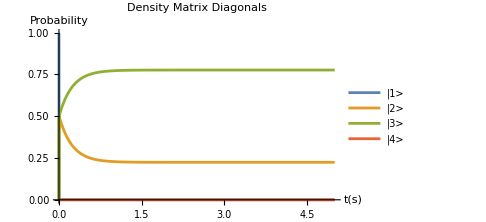

```mathematica
Flatten[{Table[Subscript[ρ, D2,i,i][t],{i,1,4}]}/.dynamicsD2];
Plot[%,{t,0,tmax},PlotRange-> Full,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLegends->{Style["|1> "],Style["|2> "],Style["|3>"],Style["|4>"]},ImageSize->Medium]
```

Transition Rates

```mathematica
Subscript[Γ, d_,P_,j_,i_]=-Subscript[ρ, d,i,i][t] Subscript[𝒥, P][Subscript[ω, d,j,i]]Subscript[n, P][Subscript[ω, d,j,i]]+Subscript[ρ, d,j,j][t]Subscript[𝒥, P][Subscript[ω, d,j,i]](1+Subscript[n, P][Subscript[ω, d,j,i]]);
```

Steady State Solutions for density matrices and energy flows

Diode D1

```mathematica
varFuncD1[TL_,TM_,ωL_,ωM_,gLMs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{NBEassum,Jassum,ωassum1D1,ωassum2D1,μassum,κassum,unitassum,Subscript[T, L]-> TL,Subscript[T, M1]-> TM,Subscript[ω, L]->ωL,Subscript[ω, M]->ωM,Subscript[g, LM]->gLMs}];
temp1=N[Subscript[sol, D1]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, D1,i_,j_]'[t]-> 0,Subscript[ρ, D1,i_,j_][t]-> Subscript[ρ, D1,i,j]},1==∑_(i=1)^4 Subscript[ρ, D1,i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, D1,i,j],{i,1,4},{j,1,4}]]]]];
Re[{Flatten[Table[Subscript[ρ, D1,i,i],{i,1,4}]/.temp3],Flatten[{Subscript[J, D1,L],Subscript[J, D1,M1]}//.Flatten[{Subscript[ρ, D1,i_,j_][t]->Subscript[ρ, D1,i,j],temp0}]/.temp3]}]]
```

```mathematica
varFuncD1[10,5 ,1,3,20,unitassum]
```

{{0.00464783,0.444335,0.54634,0.00467666},{0.000374704,-0.000374704}}

Diode D2

```mathematica
varFuncD2[TR_,TM_,ωR_,ωM_,gMRs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{NBEassum,Jassum,ωassum1D2,ωassum2D2,μassum,κassum,unitassum,Subscript[T, R]-> TR,Subscript[T, M2]-> TM,Subscript[ω, R]->ωR,Subscript[ω, M]->ωM,Subscript[g, MR]->gMRs}];
temp1=N[Subscript[sol, D2]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, D2,i_,j_]'[t]-> 0,Subscript[ρ, D2,i_,j_][t]-> Subscript[ρ, D2,i,j]},1==∑_(i=1)^4 Subscript[ρ, D2,i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, D2,i,j],{i,1,4},{j,1,4}]]]]];
Re[{Flatten[Table[Subscript[ρ, D2,i,i],{i,1,4}]/.temp3],Flatten[{Subscript[J, D2,M2],Subscript[J, D2,R]}//.Flatten[{Subscript[ρ, D2,i_,j_][t]->Subscript[ρ, D2,i,j],temp0}]/.temp3]}]]
```

```mathematica
varFuncD2[0.2,5 ,2,3,20,unitassum]
```

{{0.0000710668,0.224108,0.775752,0.0000687427},{5.88835×10^-6,-5.88835×10^-6}}

Plots for adjusting  T_M (at steady state)

Energy Inflows

Diode D1

```mathematica
varEngyFuncD1[TL_,TM_,ωL_,ωM_,gLMs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{NBEassum,Jassum,ωassum1D1,ωassum2D1,μassum,κassum,unitassum,Subscript[T, L]-> TL,Subscript[T, M1]-> TM,Subscript[ω, L]->ωL,Subscript[ω, M]->ωM,Subscript[g, LM]->gLMs}];
temp1=N[Subscript[sol, D1]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, D1,i_,j_]'[t]-> 0,Subscript[ρ, D1,i_,j_][t]-> Subscript[ρ, D1,i,j]},1==∑_(i=1)^4 Subscript[ρ, D1,i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, D1,i,j],{i,1,4},{j,1,4}]]]]];
Re[Flatten[{Subscript[J, D1,L]}//.Flatten[{Subscript[ρ, D1,i_,j_][t]->Subscript[ρ, D1,i,j],temp0}]/.temp3]]]
```

```mathematica
PlotEngyFlowsWithTMD1[Tmin_,Tmax_,Tres_,TL_,ωL_,ωM_,gLMs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T},{T,Tmin,Tmax,Tres}];
tempy1=10^4 Table[varEngyFuncD1[TL,TM,ωL,ωM,gLMs,unitassum],{TM,Tmin,Tmax,Tres}];
temp=Table[MapThread[List,{tempx[[;;,1]],tempy1[[;;,1]]}]];
ListPlot[temp,AxesStyle->Directive[Black,23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T_M",23.5,FontFamily->"Times New Roman"],Style["10^-4J_(D1, L)/ℏΔ^2",23.5,FontFamily->"Times New Roman"]},Joined->True,PlotStyle->{Thickness->Large,Orange},PlotRange->plotrange,ImageSize->Large]]
```

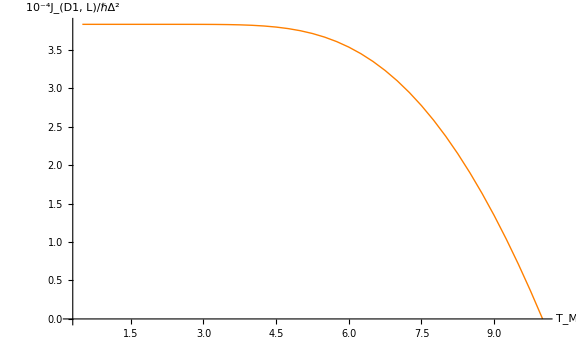

```mathematica
PlotEngyFlowsWithTMD1[0.5,10,0.25,10 ,1,3,20,Full]
```

Diode D2

```mathematica
varEngyFuncD2[TR_,TM_,ωR_,ωM_,gMRs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{NBEassum,Jassum,ωassum1D2,ωassum2D2,μassum,κassum,unitassum,Subscript[T, R]-> TR,Subscript[T, M2]-> TM,Subscript[ω, R]->ωR,Subscript[ω, M]->ωM,Subscript[g, MR]->gMRs}];
temp1=N[Subscript[sol, D2]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ, D2,i_,j_]'[t]-> 0,Subscript[ρ, D2,i_,j_][t]-> Subscript[ρ, D2,i,j]},1==∑_(i=1)^4 Subscript[ρ, D2,i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ, D2,i,j],{i,1,4},{j,1,4}]]]]];
Re[Flatten[{Subscript[J, D2,M2]}//.Flatten[{Subscript[ρ, D2,i_,j_][t]->Subscript[ρ, D2,i,j],temp0}]/.temp3]]]
```

```mathematica
PlotEngyFlowsWithTMD2[Tmin_,Tmax_,Tres_,TR_,ωR_,ωM_,gMRs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T},{T,Tmin,Tmax,Tres}];
tempy1=10^4 Table[varEngyFuncD2[TR,TM,ωR,ωM,gMRs,unitassum],{TM,Tmin,Tmax,Tres}];
temp=Table[MapThread[List,{tempx[[;;,1]],tempy1[[;;,1]]}]];
ListPlot[temp,AxesStyle->Directive[Black,23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T_M",23.5,FontFamily->"Times New Roman"],Style["10^-4J_(D2, M2)/ℏΔ^2",23.5,FontFamily->"Times New Roman"]},Joined->True,PlotStyle->{Thickness->Large,Green},PlotRange->plotrange,ImageSize->Large]]
```

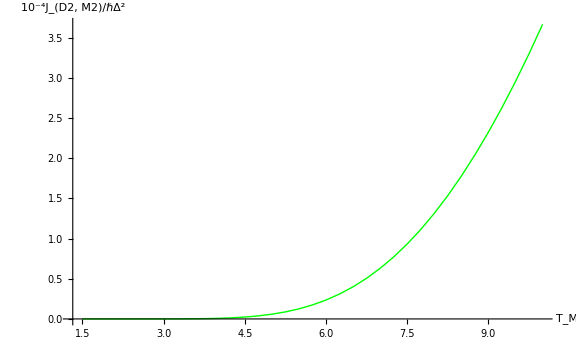

```mathematica
PlotEngyFlowsWithTMD2[0.5,10,0.25,0.2 ,2,3,20,Full]
```

Both diode characteristics in a single plot

```mathematica
varEngyFuncD1D2[TL_,TM_,TR_,ωL_,ωM_,ωR_,gLMs_,gMRs_,unitassum_]:=
Module[{temp0,temp1D1,temp2D1,temp3D1,temp1D2,temp2D2,temp3D2},
temp0=Flatten[{NBEassum,Jassum,ωassum1D1,ωassum2D1,ωassum1D2,ωassum2D2,μassum,κassum,unitassum,Subscript[T, L]-> TL,Subscript[T, R]-> TR,Subscript[T, M1]-> TM,Subscript[T, M2]-> TM,Subscript[ω, L]->ωL,Subscript[ω, R]->ωR,Subscript[ω, M]->ωM,Subscript[g, LM]->gLMs,Subscript[g, MR]->gMRs}];
temp1D1=N[Subscript[sol, D1]//.temp0];
temp1D2=N[Subscript[sol, D2]//.temp0];
temp2D1=Flatten[{temp1D1/.{Subscript[ρ, D1,i_,j_]'[t]-> 0,Subscript[ρ, D1,i_,j_][t]-> Subscript[ρ, D1,i,j]},1==∑_(i=1)^4 Subscript[ρ, D1,i,i]}];
temp2D2=Flatten[{temp1D2/.{Subscript[ρ, D2,i_,j_]'[t]-> 0,Subscript[ρ, D2,i_,j_][t]-> Subscript[ρ, D2,i,j]},1==∑_(i=1)^4 Subscript[ρ, D2,i,i]}];
temp3D1=Quiet[Flatten[Solve[temp2D1,Flatten[Table[{Subscript[ρ, D1,i,j]},{i,1,4},{j,1,4}]]]]];
temp3D2=Quiet[Flatten[Solve[temp2D2,Flatten[Table[{Subscript[ρ, D2,i,j]},{i,1,4},{j,1,4}]]]]];
Re[Flatten[{{Subscript[J, D1,L]}//.Flatten[{Subscript[ρ, D1,i_,j_][t]->Subscript[ρ, D1,i,j],temp0}]/.{temp3D1},{Subscript[J, D2,M2]}//.Flatten[{Subscript[ρ, D2,i_,j_][t]->Subscript[ρ, D2,i,j],temp0}]/.{temp3D2}}]]]
```

```mathematica
varEngyFuncD1D2[10,5,0.2,1,2,3,20,20,unitassum]
```

{0.000375929,6.47782×10^-6}

```mathematica
PlotEngyFlowsWithTMD1D2[Tmin_,Tmax_,Tres_,TL_,TR_,ωL_,ωM_,ωR_,gLMs_,gMRs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T,T},{T,Tmin,Tmax,Tres}];
tempy1=10^4 Table[varEngyFuncD1D2[TL,TM,TR,ωL,ωM,ωR,gLMs,gMRs,unitassum],{TM,Tmin,Tmax,Tres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy1[[;;,i]]}],{i,1,2}];
ListPlot[temp,AxesStyle->Directive[Black,23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T_M",23.5,FontFamily->"Times New Roman"],Style["10^-4/ℏΔ^2",23.5,FontFamily->"Times New Roman"]},Joined->True,PlotStyle->{{Thickness->Large,Orange},{Thickness->Large,Green}},PlotRange->plotrange,ImageSize->Large,PlotLabels->{Style["J_(D1, L)",23.5,FontFamily->"Times New Roman"],Style["J_(D2, M)",23.5,FontFamily->"Times New Roman"]}]]
```

```mathematica
D12=PlotEngyFlowsWithTMD1D2[0.5,10,0.25,10 ,0.2,1,2,3,20,20,Full]
```

```mathematica
D12=-Graphics-;
```

```mathematica
Export["DiodethermalFlows.pdf",D12,"PDF","AllowRasterization"->False]
```

DiodethermalFlows.pdf

## Equivalent Model with Crossing Dissipation

For cross dissipation

```mathematica
Subscript[ℒ̄, P_,Q_]:=Subscript[ℒ̄, P,Q]=∑_(α=1)^120 ∑_(β=1)^120 ((Sqrt[Subscript[𝒥, P][Part[OverBar[ωMatrix],1,α]]*(1+Subscript[n, P][Part[OverBar[ωMatrix],1,α]])*Subscript[𝒥, Q][Part[OverBar[ωMatrix],1,β]]*(1+Subscript[n, Q][Part[OverBar[ωMatrix],1,β]])]((Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]].OverBar[ρMatrix][t].Subscript[OverBar[AMatrix], Q,Part[OverBar[ωMatrix],1,β]] ᵀ- 1/2*Subscript[OverBar[AMatrix], Q,Part[OverBar[ωMatrix],1,β]] ᵀ.Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]].OverBar[ρMatrix][t]- 1/2*OverBar[ρMatrix][t].Subscript[OverBar[AMatrix], Q,Part[OverBar[ωMatrix],1,β]] ᵀ.Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]])+(Subscript[OverBar[AMatrix], Q,Part[OverBar[ωMatrix],1,β]].OverBar[ρMatrix][t].Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]] ᵀ- 1/2*Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]] ᵀ.Subscript[OverBar[AMatrix], Q,Part[OverBar[ωMatrix],1,β]].OverBar[ρMatrix][t]- 1/2*OverBar[ρMatrix][t].Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]] ᵀ.Subscript[OverBar[AMatrix], Q,Part[OverBar[ωMatrix],1,β]])))+(Sqrt[Subscript[𝒥, P][Part[OverBar[ωMatrix],1,α]]* Subscript[n, P][Part[OverBar[ωMatrix],1,α]]*Subscript[𝒥, Q][Part[OverBar[ωMatrix],1,β]] *Subscript[n, Q][Part[OverBar[ωMatrix],1,β]]]((Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]] ᵀ.OverBar[ρMatrix][t].Subscript[OverBar[AMatrix], Q,Part[OverBar[ωMatrix],1,β]]- 1/2*Subscript[OverBar[AMatrix], Q,Part[OverBar[ωMatrix],1,β]].Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]] ᵀ.OverBar[ρMatrix][t]- 1/2*OverBar[ρMatrix][t].Subscript[OverBar[AMatrix], Q,Part[OverBar[ωMatrix],1,β]].Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]] ᵀ)+(Subscript[OverBar[AMatrix], Q,Part[OverBar[ωMatrix],1,β]] ᵀ.OverBar[ρMatrix][t].Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]]-1/2* Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]].Subscript[OverBar[AMatrix], Q,Part[OverBar[ωMatrix],1,β]] ᵀ.OverBar[ρMatrix][t]- 1/2*OverBar[ρMatrix][t].Subscript[OverBar[AMatrix], P,Part[OverBar[ωMatrix],1,α]].Subscript[OverBar[AMatrix], Q,Part[OverBar[ωMatrix],1,β]] ᵀ))));
```

### Master Equation

```mathematica
OverBar[dρ1]=MatrixForm[Subscript[ℒ̄, L]+Subscript[ℒ̄, M1]+Subscript[ℒ̄, M2]+Subscript[ℒ̄, R]+Subscript[ℒ̄, M1,M2]-(ⅈ/ℏ(Subscript[H, S̄].OverBar[ρMatrix][t]-OverBar[ρMatrix][t].Subscript[H, S̄]))]//.{-Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] +(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>Subscript[Γ̄, P,j,i],Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] -(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>-Subscript[Γ̄, P,j,i],- 1/2 Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] +1/2(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>1/2 Subscript[Γ̄, P,j,i],1/2 Subscript[n, P_][Subscript[ω, j_,i_]]Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] -1/2(1+Subscript[n, P_][Subscript[ω, j_,i_]])Subscript[𝒥, P_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>-1/2 Subscript[Γ̄, P,j,i],Subscript[n, X_][Subscript[ω, i_,j_]]Subscript[𝒥, X_][Subscript[ω, i_,j_]]:>Subscript[X, i,j,Pls],(1+Subscript[n, X_][Subscript[ω, i_,j_]]) Subscript[𝒥, X_][Subscript[ω, i_,j_]]:>Subscript[X, i,j,Mns],Subscript[n, X_][Subscript[ω, i_,j_]]Subscript[𝒥, X_][Subscript[ω, i_,j_]]:>Subscript[X, i,j,Pls],(1+Subscript[n, X_][Subscript[ω, i_,j_]])Subscript[𝒥, X_][Subscript[ω, i_,j_]]:>Subscript[X, i,j,Mns],Subscript[n, X_][Subscript[ω, i_,j_]]Subscript[𝒥, Y_][Subscript[ω, a_,b_]]Subscript[n, Y_][Subscript[ω, a_,b_]]Subscript[𝒥, X_][Subscript[ω, i_,j_]]:>Subscript[Y, a,b,Pls] Subscript[X, i,j,Pls] ,(1+Subscript[n, Q_][Subscript[ω, i_,j_]])Subscript[𝒥, P_][Subscript[ω, a_,b_]] (1+Subscript[n, P_][Subscript[ω, a_,b_]]) Subscript[𝒥, Q_][Subscript[ω, i_,j_]]:>Subscript[Q, i,j,Mns] Subscript[P, a,b,Mns]};
```

#### Thermal Energy Flows

```mathematica
Subscript[OverBar[J1], P_]:=Subscript[OverBar[J1], P]=Tr[Subscript[ℒ̄, P].OverBar[HsMatrix]]//.{-Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] +(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>Subscript[Γ, Q,j,i],Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, i_,i_][t] -(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ, j_,j_][t]:>-Subscript[Γ, Q,j,i]};
```

```mathematica
Subscript[OverBar[J1], M]=Tr[(Subscript[ℒ̄, M1]+Subscript[ℒ̄, M2]+Subscript[ℒ̄, M1,M2]).OverBar[HsMatrix]]//.{-Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] +(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>Subscript[Γ̄, Q,j,i],Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] -(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>-Subscript[Γ̄, Q,j,i],1/2(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]-1/2 Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] :>1/2 Subscript[Γ̄, Q,j,i],1/2 Subscript[n, Q_][Subscript[ω, j_,i_]]Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, i_,i_][t] -1/2(1+Subscript[n, Q_][Subscript[ω, j_,i_]])Subscript[𝒥, Q_][Subscript[ω, j_,i_]]Subscript[ρ̄, j_,j_][t]:>-1/2 Subscript[Γ̄, Q,j,i]};
```

### Simulations

```mathematica
OverBar[RHS1]=Subscript[ℒ̄, L]+Subscript[ℒ̄, M1]+Subscript[ℒ̄, M2]+Subscript[ℒ̄, R]+Subscript[ℒ̄, M1,M2]-(ⅈ/ℏ(Subscript[H, S̄].OverBar[ρMatrix][t]-OverBar[ρMatrix][t].Subscript[H, S̄]));
OverBar[LHS1]=D[OverBar[ρMatrix][t], t];
```

```mathematica
OverBar[sol1]=Flatten[Solve[OverBar[LHS1]==OverBar[RHS1],Flatten[Table[Subscript[ρ̄, i,j]'[t],{i,1,16},{j,1,16}]]]/.Rule->Equal];
```

Separate diagonal and off diagonal equations,

```mathematica
OverBar[soldiag1]=OverBar[sol1][[1;; ;;17]];
OverBar[soloffdiag1]=Delete[OverBar[sol1],Table[{1+17i},{i,0,15}]];
```

Off diagonal Solutions

```mathematica
Flatten[{OverBar[soloffdiag1]/.{Subscript[ρ̄, i_,j_]'[t]-> 0,Subscript[ρ̄, i_,j_][t]-> Subscript[ρ̄, i,j]}}];
OverBar[soloffdiagstat1]=Solve[%,DeleteCases[Flatten[Table[Subscript[ρ̄, i,j]-i,j Subscript[ρ̄, i,j],{i,1,16},{j,1,16}]],0]]
```

{{(ρ̄)_(1,2)→0,(ρ̄)_(1,3)→0,(ρ̄)_(1,4)→0,(ρ̄)_(1,5)→0,(ρ̄)_(1,6)→0,(ρ̄)_(1,7)→0,(ρ̄)_(1,8)→0,(ρ̄)_(1,9)→0,(ρ̄)_(1,10)→0,(ρ̄)_(1,11)→0,(ρ̄)_(1,12)→0,(ρ̄)_(1,13)→0,(ρ̄)_(1,14)→0,(ρ̄)_(1,15)→0,(ρ̄)_(1,16)→0,(ρ̄)_(2,1)→0,(ρ̄)_(2,3)→0,(ρ̄)_(2,4)→0,(ρ̄)_(2,5)→0,(ρ̄)_(2,6)→0,(ρ̄)_(2,7)→0,(ρ̄)_(2,8)→0,(ρ̄)_(2,9)→0,(ρ̄)_(2,10)→0,(ρ̄)_(2,11)→0,(ρ̄)_(2,12)→0,(ρ̄)_(2,13)→0,(ρ̄)_(2,14)→0,(ρ̄)_(2,15)→0,(ρ̄)_(2,16)→0,(ρ̄)_(3,1)→0,(ρ̄)_(3,2)→0,(ρ̄)_(3,4)→0,(ρ̄)_(3,5)→-((ρ̄)_(3,3) √(n_M1[ω_(1,5)] n_M2[ω_(1,3)] 𝒥_M1[ω_(1,5)] 𝒥_M2[ω_(1,3)])+(ρ̄)_(5,5) √(n_M1[ω_(1,5)] n_M2[ω_(1,3)] 𝒥_M1[ω_(1,5)] 𝒥_M2[ω_(1,3)])-2 (ρ̄)_(1,1) √((1+n_M1[ω_(1,5)]) (1+n_M2[ω_(1,3)]) 𝒥_M1[ω_(1,5)] 𝒥_M2[ω_(1,3)])-2 (ρ̄)_(7,7) √(n_M1[ω_(3,7)] n_M2[ω_(5,7)] 𝒥_M1[ω_(3,7)] 𝒥_M2[ω_(5,7)])+(ρ̄)_(3,3) √((1+n_M1[ω_(3,7)]) (1+n_M2[ω_(5,7)]) 𝒥_M1[ω_(3,7)] 𝒥_M2[ω_(5,7)])+(ρ̄)_(5,5) √((1+n_M1[ω_(3,7)]) (1+n_M2[ω_(5,7)]) 𝒥_M1[ω_(3,7)] 𝒥_M2[ω_(5,7)]))/(8 ⅈ g_LM-8 ⅈ g_MR+𝒥_L[ω_(3,11)]+n_L[ω_(3,11)] 𝒥_L[ω_(3,11)]+𝒥_L[ω_(5,13)]+n_L[ω_(5,13)] 𝒥_L[ω_(5,13)]+n_M1[ω_(1,5)] 𝒥_M1[ω_(1,5)]+𝒥_M1[ω_(3,7)]+n_M1[ω_(3,7)] 𝒥_M1[ω_(3,7)]+n_M2[ω_(1,3)] 𝒥_M2[ω_(1,3)]+𝒥_M2[ω_(5,7)]+n_M2[ω_(5,7)] 𝒥_M2[ω_(5,7)]+𝒥_R[ω_(3,4)]+n_R[ω_(3,4)] 𝒥_R[ω_(3,4)]+𝒥_R[ω_(5,6)]+n_R[ω_(5,6)] 𝒥_R[ω_(5,6)]),(ρ̄)_(3,6)→0,(ρ̄)_(3,7)→0,(ρ̄)_(3,8)→0,(ρ̄)_(3,9)→0,(ρ̄)_(3,10)→0,(ρ̄)_(3,11)→0,(ρ̄)_(3,12)→0,(ρ̄)_(3,13)→0,(ρ̄)_(3,14)→0,(ρ̄)_(3,15)→0,(ρ̄)_(3,16)→0,(ρ̄)_(4,1)→0,(ρ̄)_(4,2)→0,(ρ̄)_(4,3)→0,(ρ̄)_(4,5)→0,(ρ̄)_(4,6)→-((ρ̄)_(4,4) √(n_M1[ω_(2,6)] n_M2[ω_(2,4)] 𝒥_M1[ω_(2,6)] 𝒥_M2[ω_(2,4)])+(ρ̄)_(6,6) √(n_M1[ω_(2,6)] n_M2[ω_(2,4)] 𝒥_M1[ω_(2,6)] 𝒥_M2[ω_(2,4)])-2 (ρ̄)_(2,2) √((1+n_M1[ω_(2,6)]) (1+n_M2[ω_(2,4)]) 𝒥_M1[ω_(2,6)] 𝒥_M2[ω_(2,4)])-2 (ρ̄)_(8,8) √(n_M1[ω_(4,8)] n_M2[ω_(6,8)] 𝒥_M1[ω_(4,8)] 𝒥_M2[ω_(6,8)])+(ρ̄)_(4,4) √((1+n_M1[ω_(4,8)]) (1+n_M2[ω_(6,8)]) 𝒥_M1[ω_(4,8)] 𝒥_M2[ω_(6,8)])+(ρ̄)_(6,6) √((1+n_M1[ω_(4,8)]) (1+n_M2[ω_(6,8)]) 𝒥_M1[ω_(4,8)] 𝒥_M2[ω_(6,8)]))/(8 ⅈ g_LM-16 ⅈ g_M+8 ⅈ g_MR+𝒥_L[ω_(4,12)]+n_L[ω_(4,12)] 𝒥_L[ω_(4,12)]+𝒥_L[ω_(6,14)]+n_L[ω_(6,14)] 𝒥_L[ω_(6,14)]+n_M1[ω_(2,6)] 𝒥_M1[ω_(2,6)]+𝒥_M1[ω_(4,8)]+n_M1[ω_(4,8)] 𝒥_M1[ω_(4,8)]+n_M2[ω_(2,4)] 𝒥_M2[ω_(2,4)]+𝒥_M2[ω_(6,8)]+n_M2[ω_(6,8)] 𝒥_M2[ω_(6,8)]+n_R[ω_(3,4)] 𝒥_R[ω_(3,4)]+n_R[ω_(5,6)] 𝒥_R[ω_(5,6)]),(ρ̄)_(4,7)→0,(ρ̄)_(4,8)→0,(ρ̄)_(4,9)→0,(ρ̄)_(4,10)→0,(ρ̄)_(4,11)→0,(ρ̄)_(4,12)→0,(ρ̄)_(4,13)→0,(ρ̄)_(4,14)→0,(ρ̄)_(4,15)→0,(ρ̄)_(4,16)→0,(ρ̄)_(5,1)→0,(ρ̄)_(5,2)→0,(ρ̄)_(5,3)→-((ρ̄)_(3,3) √(n_M1[ω_(1,5)] n_M2[ω_(1,3)] 𝒥_M1[ω_(1,5)] 𝒥_M2[ω_(1,3)])+(ρ̄)_(5,5) √(n_M1[ω_(1,5)] n_M2[ω_(1,3)] 𝒥_M1[ω_(1,5)] 𝒥_M2[ω_(1,3)])-2 (ρ̄)_(1,1) √((1+n_M1[ω_(1,5)]) (1+n_M2[ω_(1,3)]) 𝒥_M1[ω_(1,5)] 𝒥_M2[ω_(1,3)])-2 (ρ̄)_(7,7) √(n_M1[ω_(3,7)] n_M2[ω_(5,7)] 𝒥_M1[ω_(3,7)] 𝒥_M2[ω_(5,7)])+(ρ̄)_(3,3) √((1+n_M1[ω_(3,7)]) (1+n_M2[ω_(5,7)]) 𝒥_M1[ω_(3,7)] 𝒥_M2[ω_(5,7)])+(ρ̄)_(5,5) √((1+n_M1[ω_(3,7)]) (1+n_M2[ω_(5,7)]) 𝒥_M1[ω_(3,7)] 𝒥_M2[ω_(5,7)]))/(-8 ⅈ g_LM+8 ⅈ g_MR+𝒥_L[ω_(3,11)]+n_L[ω_(3,11)] 𝒥_L[ω_(3,11)]+𝒥_L[ω_(5,13)]+n_L[ω_(5,13)] 𝒥_L[ω_(5,13)]+n_M1[ω_(1,5)] 𝒥_M1[ω_(1,5)]+𝒥_M1[ω_(3,7)]+n_M1[ω_(3,7)] 𝒥_M1[ω_(3,7)]+n_M2[ω_(1,3)] 𝒥_M2[ω_(1,3)]+𝒥_M2[ω_(5,7)]+n_M2[ω_(5,7)] 𝒥_M2[ω_(5,7)]+𝒥_R[ω_(3,4)]+n_R[ω_(3,4)] 𝒥_R[ω_(3,4)]+𝒥_R[ω_(5,6)]+n_R[ω_(5,6)] 𝒥_R[ω_(5,6)]),(ρ̄)_(5,4)→0,(ρ̄)_(5,6)→0,(ρ̄)_(5,7)→0,(ρ̄)_(5,8)→0,(ρ̄)_(5,9)→0,(ρ̄)_(5,10)→0,(ρ̄)_(5,11)→0,(ρ̄)_(5,12)→0,(ρ̄)_(5,13)→0,(ρ̄)_(5,14)→0,(ρ̄)_(5,15)→0,(ρ̄)_(5,16)→0,(ρ̄)_(6,1)→0,(ρ̄)_(6,2)→0,(ρ̄)_(6,3)→0,(ρ̄)_(6,4)→-((ρ̄)_(4,4) √(n_M1[ω_(2,6)] n_M2[ω_(2,4)] 𝒥_M1[ω_(2,6)] 𝒥_M2[ω_(2,4)])+(ρ̄)_(6,6) √(n_M1[ω_(2,6)] n_M2[ω_(2,4)] 𝒥_M1[ω_(2,6)] 𝒥_M2[ω_(2,4)])-2 (ρ̄)_(2,2) √((1+n_M1[ω_(2,6)]) (1+n_M2[ω_(2,4)]) 𝒥_M1[ω_(2,6)] 𝒥_M2[ω_(2,4)])-2 (ρ̄)_(8,8) √(n_M1[ω_(4,8)] n_M2[ω_(6,8)] 𝒥_M1[ω_(4,8)] 𝒥_M2[ω_(6,8)])+(ρ̄)_(4,4) √((1+n_M1[ω_(4,8)]) (1+n_M2[ω_(6,8)]) 𝒥_M1[ω_(4,8)] 𝒥_M2[ω_(6,8)])+(ρ̄)_(6,6) √((1+n_M1[ω_(4,8)]) (1+n_M2[ω_(6,8)]) 𝒥_M1[ω_(4,8)] 𝒥_M2[ω_(6,8)]))/(-8 ⅈ g_LM+16 ⅈ g_M-8 ⅈ g_MR+𝒥_L[ω_(4,12)]+n_L[ω_(4,12)] 𝒥_L[ω_(4,12)]+𝒥_L[ω_(6,14)]+n_L[ω_(6,14)] 𝒥_L[ω_(6,14)]+n_M1[ω_(2,6)] 𝒥_M1[ω_(2,6)]+𝒥_M1[ω_(4,8)]+n_M1[ω_(4,8)] 𝒥_M1[ω_(4,8)]+n_M2[ω_(2,4)] 𝒥_M2[ω_(2,4)]+𝒥_M2[ω_(6,8)]+n_M2[ω_(6,8)] 𝒥_M2[ω_(6,8)]+n_R[ω_(3,4)] 𝒥_R[ω_(3,4)]+n_R[ω_(5,6)] 𝒥_R[ω_(5,6)]),(ρ̄)_(6,5)→0,(ρ̄)_(6,7)→0,(ρ̄)_(6,8)→0,(ρ̄)_(6,9)→0,(ρ̄)_(6,10)→0,(ρ̄)_(6,11)→0,(ρ̄)_(6,12)→0,(ρ̄)_(6,13)→0,(ρ̄)_(6,14)→0,(ρ̄)_(6,15)→0,(ρ̄)_(6,16)→0,(ρ̄)_(7,1)→0,(ρ̄)_(7,2)→0,(ρ̄)_(7,3)→0,(ρ̄)_(7,4)→0,(ρ̄)_(7,5)→0,(ρ̄)_(7,6)→0,(ρ̄)_(7,8)→0,(ρ̄)_(7,9)→0,(ρ̄)_(7,10)→0,(ρ̄)_(7,11)→0,(ρ̄)_(7,12)→0,(ρ̄)_(7,13)→0,(ρ̄)_(7,14)→0,(ρ̄)_(7,15)→0,(ρ̄)_(7,16)→0,(ρ̄)_(8,1)→0,(ρ̄)_(8,2)→0,(ρ̄)_(8,3)→0,(ρ̄)_(8,4)→0,(ρ̄)_(8,5)→0,(ρ̄)_(8,6)→0,(ρ̄)_(8,7)→0,(ρ̄)_(8,9)→0,(ρ̄)_(8,10)→0,(ρ̄)_(8,11)→0,(ρ̄)_(8,12)→0,(ρ̄)_(8,13)→0,(ρ̄)_(8,14)→0,(ρ̄)_(8,15)→0,(ρ̄)_(8,16)→0,(ρ̄)_(9,1)→0,(ρ̄)_(9,2)→0,(ρ̄)_(9,3)→0,(ρ̄)_(9,4)→0,(ρ̄)_(9,5)→0,(ρ̄)_(9,6)→0,(ρ̄)_(9,7)→0,(ρ̄)_(9,8)→0,(ρ̄)_(9,10)→0,(ρ̄)_(9,11)→0,(ρ̄)_(9,12)→0,(ρ̄)_(9,13)→0,(ρ̄)_(9,14)→0,(ρ̄)_(9,15)→0,(ρ̄)_(9,16)→0,(ρ̄)_(10,1)→0,(ρ̄)_(10,2)→0,(ρ̄)_(10,3)→0,(ρ̄)_(10,4)→0,(ρ̄)_(10,5)→0,(ρ̄)_(10,6)→0,(ρ̄)_(10,7)→0,(ρ̄)_(10,8)→0,(ρ̄)_(10,9)→0,(ρ̄)_(10,11)→0,(ρ̄)_(10,12)→0,(ρ̄)_(10,13)→0,(ρ̄)_(10,14)→0,(ρ̄)_(10,15)→0,(ρ̄)_(10,16)→0,(ρ̄)_(11,1)→0,(ρ̄)_(11,2)→0,(ρ̄)_(11,3)→0,(ρ̄)_(11,4)→0,(ρ̄)_(11,5)→0,(ρ̄)_(11,6)→0,(ρ̄)_(11,7)→0,(ρ̄)_(11,8)→0,(ρ̄)_(11,9)→0,(ρ̄)_(11,10)→0,(ρ̄)_(11,12)→0,(ρ̄)_(11,13)→-(((ρ̄)_(11,11) √(n_M1[ω_(9,13)] n_M2[ω_(9,11)] 𝒥_M1[ω_(9,13)] 𝒥_M2[ω_(9,11)])+(ρ̄)_(13,13) √(n_M1[ω_(9,13)] n_M2[ω_(9,11)] 𝒥_M1[ω_(9,13)] 𝒥_M2[ω_(9,11)])-2 (ρ̄)_(9,9) √((1+n_M1[ω_(9,13)]) (1+n_M2[ω_(9,11)]) 𝒥_M1[ω_(9,13)] 𝒥_M2[ω_(9,11)])-2 (ρ̄)_(15,15) √(n_M1[ω_(11,15)] n_M2[ω_(13,15)] 𝒥_M1[ω_(11,15)] 𝒥_M2[ω_(13,15)])+(ρ̄)_(11,11) √((1+n_M1[ω_(11,15)]) (1+n_M2[ω_(13,15)]) 𝒥_M1[ω_(11,15)] 𝒥_M2[ω_(13,15)])+(ρ̄)_(13,13) √((1+n_M1[ω_(11,15)]) (1+n_M2[ω_(13,15)]) 𝒥_M1[ω_(11,15)] 𝒥_M2[ω_(13,15)]))/(-8 ⅈ g_LM+16 ⅈ g_M-8 ⅈ g_MR+n_L[ω_(3,11)] 𝒥_L[ω_(3,11)]+n_L[ω_(5,13)] 𝒥_L[ω_(5,13)]+n_M1[ω_(9,13)] 𝒥_M1[ω_(9,13)]+𝒥_M1[ω_(11,15)]+n_M1[ω_(11,15)] 𝒥_M1[ω_(11,15)]+n_M2[ω_(9,11)] 𝒥_M2[ω_(9,11)]+𝒥_M2[ω_(13,15)]+n_M2[ω_(13,15)] 𝒥_M2[ω_(13,15)]+𝒥_R[ω_(11,12)]+n_R[ω_(11,12)] 𝒥_R[ω_(11,12)]+𝒥_R[ω_(13,14)]+n_R[ω_(13,14)] 𝒥_R[ω_(13,14)])),(ρ̄)_(11,14)→0,(ρ̄)_(11,15)→0,(ρ̄)_(11,16)→0,(ρ̄)_(12,1)→0,(ρ̄)_(12,2)→0,(ρ̄)_(12,3)→0,(ρ̄)_(12,4)→0,(ρ̄)_(12,5)→0,(ρ̄)_(12,6)→0,(ρ̄)_(12,7)→0,(ρ̄)_(12,8)→0,(ρ̄)_(12,9)→0,(ρ̄)_(12,10)→0,(ρ̄)_(12,11)→0,(ρ̄)_(12,13)→0,(ρ̄)_(12,14)→-(((ρ̄)_(12,12) √(n_M1[ω_(10,14)] n_M2[ω_(10,12)] 𝒥_M1[ω_(10,14)] 𝒥_M2[ω_(10,12)])+(ρ̄)_(14,14) √(n_M1[ω_(10,14)] n_M2[ω_(10,12)] 𝒥_M1[ω_(10,14)] 𝒥_M2[ω_(10,12)])-2 (ρ̄)_(10,10) √((1+n_M1[ω_(10,14)]) (1+n_M2[ω_(10,12)]) 𝒥_M1[ω_(10,14)] 𝒥_M2[ω_(10,12)])-2 (ρ̄)_(16,16) √(n_M1[ω_(12,16)] n_M2[ω_(14,16)] 𝒥_M1[ω_(12,16)] 𝒥_M2[ω_(14,16)])+(ρ̄)_(12,12) √((1+n_M1[ω_(12,16)]) (1+n_M2[ω_(14,16)]) 𝒥_M1[ω_(12,16)] 𝒥_M2[ω_(14,16)])+(ρ̄)_(14,14) √((1+n_M1[ω_(12,16)]) (1+n_M2[ω_(14,16)]) 𝒥_M1[ω_(12,16)] 𝒥_M2[ω_(14,16)]))/(-8 ⅈ g_LM+8 ⅈ g_MR+n_L[ω_(4,12)] 𝒥_L[ω_(4,12)]+n_L[ω_(6,14)] 𝒥_L[ω_(6,14)]+n_M1[ω_(10,14)] 𝒥_M1[ω_(10,14)]+𝒥_M1[ω_(12,16)]+n_M1[ω_(12,16)] 𝒥_M1[ω_(12,16)]+n_M2[ω_(10,12)] 𝒥_M2[ω_(10,12)]+𝒥_M2[ω_(14,16)]+n_M2[ω_(14,16)] 𝒥_M2[ω_(14,16)]+n_R[ω_(11,12)] 𝒥_R[ω_(11,12)]+n_R[ω_(13,14)] 𝒥_R[ω_(13,14)])),(ρ̄)_(12,15)→0,(ρ̄)_(12,16)→0,(ρ̄)_(13,1)→0,(ρ̄)_(13,2)→0,(ρ̄)_(13,3)→0,(ρ̄)_(13,4)→0,(ρ̄)_(13,5)→0,(ρ̄)_(13,6)→0,(ρ̄)_(13,7)→0,(ρ̄)_(13,8)→0,(ρ̄)_(13,9)→0,(ρ̄)_(13,10)→0,(ρ̄)_(13,11)→-(((ρ̄)_(11,11) √(n_M1[ω_(9,13)] n_M2[ω_(9,11)] 𝒥_M1[ω_(9,13)] 𝒥_M2[ω_(9,11)])+(ρ̄)_(13,13) √(n_M1[ω_(9,13)] n_M2[ω_(9,11)] 𝒥_M1[ω_(9,13)] 𝒥_M2[ω_(9,11)])-2 (ρ̄)_(9,9) √((1+n_M1[ω_(9,13)]) (1+n_M2[ω_(9,11)]) 𝒥_M1[ω_(9,13)] 𝒥_M2[ω_(9,11)])-2 (ρ̄)_(15,15) √(n_M1[ω_(11,15)] n_M2[ω_(13,15)] 𝒥_M1[ω_(11,15)] 𝒥_M2[ω_(13,15)])+(ρ̄)_(11,11) √((1+n_M1[ω_(11,15)]) (1+n_M2[ω_(13,15)]) 𝒥_M1[ω_(11,15)] 𝒥_M2[ω_(13,15)])+(ρ̄)_(13,13) √((1+n_M1[ω_(11,15)]) (1+n_M2[ω_(13,15)]) 𝒥_M1[ω_(11,15)] 𝒥_M2[ω_(13,15)]))/(8 ⅈ g_LM-16 ⅈ g_M+8 ⅈ g_MR+n_L[ω_(3,11)] 𝒥_L[ω_(3,11)]+n_L[ω_(5,13)] 𝒥_L[ω_(5,13)]+n_M1[ω_(9,13)] 𝒥_M1[ω_(9,13)]+𝒥_M1[ω_(11,15)]+n_M1[ω_(11,15)] 𝒥_M1[ω_(11,15)]+n_M2[ω_(9,11)] 𝒥_M2[ω_(9,11)]+𝒥_M2[ω_(13,15)]+n_M2[ω_(13,15)] 𝒥_M2[ω_(13,15)]+𝒥_R[ω_(11,12)]+n_R[ω_(11,12)] 𝒥_R[ω_(11,12)]+𝒥_R[ω_(13,14)]+n_R[ω_(13,14)] 𝒥_R[ω_(13,14)])),(ρ̄)_(13,12)→0,(ρ̄)_(13,14)→0,(ρ̄)_(13,15)→0,(ρ̄)_(13,16)→0,(ρ̄)_(14,1)→0,(ρ̄)_(14,2)→0,(ρ̄)_(14,3)→0,(ρ̄)_(14,4)→0,(ρ̄)_(14,5)→0,(ρ̄)_(14,6)→0,(ρ̄)_(14,7)→0,(ρ̄)_(14,8)→0,(ρ̄)_(14,9)→0,(ρ̄)_(14,10)→0,(ρ̄)_(14,11)→0,(ρ̄)_(14,12)→-(((ρ̄)_(12,12) √(n_M1[ω_(10,14)] n_M2[ω_(10,12)] 𝒥_M1[ω_(10,14)] 𝒥_M2[ω_(10,12)])+(ρ̄)_(14,14) √(n_M1[ω_(10,14)] n_M2[ω_(10,12)] 𝒥_M1[ω_(10,14)] 𝒥_M2[ω_(10,12)])-2 (ρ̄)_(10,10) √((1+n_M1[ω_(10,14)]) (1+n_M2[ω_(10,12)]) 𝒥_M1[ω_(10,14)] 𝒥_M2[ω_(10,12)])-2 (ρ̄)_(16,16) √(n_M1[ω_(12,16)] n_M2[ω_(14,16)] 𝒥_M1[ω_(12,16)] 𝒥_M2[ω_(14,16)])+(ρ̄)_(12,12) √((1+n_M1[ω_(12,16)]) (1+n_M2[ω_(14,16)]) 𝒥_M1[ω_(12,16)] 𝒥_M2[ω_(14,16)])+(ρ̄)_(14,14) √((1+n_M1[ω_(12,16)]) (1+n_M2[ω_(14,16)]) 𝒥_M1[ω_(12,16)] 𝒥_M2[ω_(14,16)]))/(8 ⅈ g_LM-8 ⅈ g_MR+n_L[ω_(4,12)] 𝒥_L[ω_(4,12)]+n_L[ω_(6,14)] 𝒥_L[ω_(6,14)]+n_M1[ω_(10,14)] 𝒥_M1[ω_(10,14)]+𝒥_M1[ω_(12,16)]+n_M1[ω_(12,16)] 𝒥_M1[ω_(12,16)]+n_M2[ω_(10,12)] 𝒥_M2[ω_(10,12)]+𝒥_M2[ω_(14,16)]+n_M2[ω_(14,16)] 𝒥_M2[ω_(14,16)]+n_R[ω_(11,12)] 𝒥_R[ω_(11,12)]+n_R[ω_(13,14)] 𝒥_R[ω_(13,14)])),(ρ̄)_(14,13)→0,(ρ̄)_(14,15)→0,(ρ̄)_(14,16)→0,(ρ̄)_(15,1)→0,(ρ̄)_(15,2)→0,(ρ̄)_(15,3)→0,(ρ̄)_(15,4)→0,(ρ̄)_(15,5)→0,(ρ̄)_(15,6)→0,(ρ̄)_(15,7)→0,(ρ̄)_(15,8)→0,(ρ̄)_(15,9)→0,(ρ̄)_(15,10)→0,(ρ̄)_(15,11)→0,(ρ̄)_(15,12)→0,(ρ̄)_(15,13)→0,(ρ̄)_(15,14)→0,(ρ̄)_(15,16)→0,(ρ̄)_(16,1)→0,(ρ̄)_(16,2)→0,(ρ̄)_(16,3)→0,(ρ̄)_(16,4)→0,(ρ̄)_(16,5)→0,(ρ̄)_(16,6)→0,(ρ̄)_(16,7)→0,(ρ̄)_(16,8)→0,(ρ̄)_(16,9)→0,(ρ̄)_(16,10)→0,(ρ̄)_(16,11)→0,(ρ̄)_(16,12)→0,(ρ̄)_(16,13)→0,(ρ̄)_(16,14)→0,(ρ̄)_(16,15)→0}}

```mathematica
Flatten[{OverBar[soloffdiag1]/.Subscript[ρ̄, i_,j_][t]-> i,j Subscript[ρ̄, i,j]}]
```

{(ρ̄)_(1,2)'[t]==0,(ρ̄)_(1,3)'[t]==0,(ρ̄)_(1,4)'[t]==0,(ρ̄)_(1,5)'[t]==0,(ρ̄)_(1,6)'[t]==0,(ρ̄)_(1,7)'[t]==0,(ρ̄)_(1,8)'[t]==0,(ρ̄)_(1,9)'[t]==0,(ρ̄)_(1,10)'[t]==0,(ρ̄)_(1,11)'[t]==0,(ρ̄)_(1,12)'[t]==0,(ρ̄)_(1,13)'[t]==0,(ρ̄)_(1,14)'[t]==0,(ρ̄)_(1,15)'[t]==0,(ρ̄)_(1,16)'[t]==0,(ρ̄)_(2,1)'[t]==0,(ρ̄)_(2,3)'[t]==0,(ρ̄)_(2,4)'[t]==0,(ρ̄)_(2,5)'[t]==0,(ρ̄)_(2,6)'[t]==0,(ρ̄)_(2,7)'[t]==0,(ρ̄)_(2,8)'[t]==0,(ρ̄)_(2,9)'[t]==0,(ρ̄)_(2,10)'[t]==0,(ρ̄)_(2,11)'[t]==0,(ρ̄)_(2,12)'[t]==0,(ρ̄)_(2,13)'[t]==0,(ρ̄)_(2,14)'[t]==0,(ρ̄)_(2,15)'[t]==0,(ρ̄)_(2,16)'[t]==0,(ρ̄)_(3,1)'[t]==0,(ρ̄)_(3,2)'[t]==0,(ρ̄)_(3,4)'[t]==0,(ρ̄)_(3,5)'[t]==1/4 (-(ρ̄)_(3,3) √(n_M1[ω_(1,5)] n_M2[ω_(1,3)] 𝒥_M1[ω_(1,5)] 𝒥_M2[ω_(1,3)])-(ρ̄)_(5,5) √(n_M1[ω_(1,5)] n_M2[ω_(1,3)] 𝒥_M1[ω_(1,5)] 𝒥_M2[ω_(1,3)])+2 (ρ̄)_(1,1) √((1+n_M1[ω_(1,5)]) (1+n_M2[ω_(1,3)]) 𝒥_M1[ω_(1,5)] 𝒥_M2[ω_(1,3)])+2 (ρ̄)_(7,7) √(n_M1[ω_(3,7)] n_M2[ω_(5,7)] 𝒥_M1[ω_(3,7)] 𝒥_M2[ω_(5,7)])-(ρ̄)_(3,3) √((1+n_M1[ω_(3,7)]) (1+n_M2[ω_(5,7)]) 𝒥_M1[ω_(3,7)] 𝒥_M2[ω_(5,7)])-(ρ̄)_(5,5) √((1+n_M1[ω_(3,7)]) (1+n_M2[ω_(5,7)]) 𝒥_M1[ω_(3,7)] 𝒥_M2[ω_(5,7)])),(ρ̄)_(3,6)'[t]==0,(ρ̄)_(3,7)'[t]==0,(ρ̄)_(3,8)'[t]==0,(ρ̄)_(3,9)'[t]==0,(ρ̄)_(3,10)'[t]==0,(ρ̄)_(3,11)'[t]==0,(ρ̄)_(3,12)'[t]==0,(ρ̄)_(3,13)'[t]==0,(ρ̄)_(3,14)'[t]==0,(ρ̄)_(3,15)'[t]==0,(ρ̄)_(3,16)'[t]==0,(ρ̄)_(4,1)'[t]==0,(ρ̄)_(4,2)'[t]==0,(ρ̄)_(4,3)'[t]==0,(ρ̄)_(4,5)'[t]==0,(ρ̄)_(4,6)'[t]==1/4 (-(ρ̄)_(4,4) √(n_M1[ω_(2,6)] n_M2[ω_(2,4)] 𝒥_M1[ω_(2,6)] 𝒥_M2[ω_(2,4)])-(ρ̄)_(6,6) √(n_M1[ω_(2,6)] n_M2[ω_(2,4)] 𝒥_M1[ω_(2,6)] 𝒥_M2[ω_(2,4)])+2 (ρ̄)_(2,2) √((1+n_M1[ω_(2,6)]) (1+n_M2[ω_(2,4)]) 𝒥_M1[ω_(2,6)] 𝒥_M2[ω_(2,4)])+2 (ρ̄)_(8,8) √(n_M1[ω_(4,8)] n_M2[ω_(6,8)] 𝒥_M1[ω_(4,8)] 𝒥_M2[ω_(6,8)])-(ρ̄)_(4,4) √((1+n_M1[ω_(4,8)]) (1+n_M2[ω_(6,8)]) 𝒥_M1[ω_(4,8)] 𝒥_M2[ω_(6,8)])-(ρ̄)_(6,6) √((1+n_M1[ω_(4,8)]) (1+n_M2[ω_(6,8)]) 𝒥_M1[ω_(4,8)] 𝒥_M2[ω_(6,8)])),(ρ̄)_(4,7)'[t]==0,(ρ̄)_(4,8)'[t]==0,(ρ̄)_(4,9)'[t]==0,(ρ̄)_(4,10)'[t]==0,(ρ̄)_(4,11)'[t]==0,(ρ̄)_(4,12)'[t]==0,(ρ̄)_(4,13)'[t]==0,(ρ̄)_(4,14)'[t]==0,(ρ̄)_(4,15)'[t]==0,(ρ̄)_(4,16)'[t]==0,(ρ̄)_(5,1)'[t]==0,(ρ̄)_(5,2)'[t]==0,(ρ̄)_(5,3)'[t]==1/4 (-(ρ̄)_(3,3) √(n_M1[ω_(1,5)] n_M2[ω_(1,3)] 𝒥_M1[ω_(1,5)] 𝒥_M2[ω_(1,3)])-(ρ̄)_(5,5) √(n_M1[ω_(1,5)] n_M2[ω_(1,3)] 𝒥_M1[ω_(1,5)] 𝒥_M2[ω_(1,3)])+2 (ρ̄)_(1,1) √((1+n_M1[ω_(1,5)]) (1+n_M2[ω_(1,3)]) 𝒥_M1[ω_(1,5)] 𝒥_M2[ω_(1,3)])+2 (ρ̄)_(7,7) √(n_M1[ω_(3,7)] n_M2[ω_(5,7)] 𝒥_M1[ω_(3,7)] 𝒥_M2[ω_(5,7)])-(ρ̄)_(3,3) √((1+n_M1[ω_(3,7)]) (1+n_M2[ω_(5,7)]) 𝒥_M1[ω_(3,7)] 𝒥_M2[ω_(5,7)])-(ρ̄)_(5,5) √((1+n_M1[ω_(3,7)]) (1+n_M2[ω_(5,7)]) 𝒥_M1[ω_(3,7)] 𝒥_M2[ω_(5,7)])),(ρ̄)_(5,4)'[t]==0,(ρ̄)_(5,6)'[t]==0,(ρ̄)_(5,7)'[t]==0,(ρ̄)_(5,8)'[t]==0,(ρ̄)_(5,9)'[t]==0,(ρ̄)_(5,10)'[t]==0,(ρ̄)_(5,11)'[t]==0,(ρ̄)_(5,12)'[t]==0,(ρ̄)_(5,13)'[t]==0,(ρ̄)_(5,14)'[t]==0,(ρ̄)_(5,15)'[t]==0,(ρ̄)_(5,16)'[t]==0,(ρ̄)_(6,1)'[t]==0,(ρ̄)_(6,2)'[t]==0,(ρ̄)_(6,3)'[t]==0,(ρ̄)_(6,4)'[t]==1/4 (-(ρ̄)_(4,4) √(n_M1[ω_(2,6)] n_M2[ω_(2,4)] 𝒥_M1[ω_(2,6)] 𝒥_M2[ω_(2,4)])-(ρ̄)_(6,6) √(n_M1[ω_(2,6)] n_M2[ω_(2,4)] 𝒥_M1[ω_(2,6)] 𝒥_M2[ω_(2,4)])+2 (ρ̄)_(2,2) √((1+n_M1[ω_(2,6)]) (1+n_M2[ω_(2,4)]) 𝒥_M1[ω_(2,6)] 𝒥_M2[ω_(2,4)])+2 (ρ̄)_(8,8) √(n_M1[ω_(4,8)] n_M2[ω_(6,8)] 𝒥_M1[ω_(4,8)] 𝒥_M2[ω_(6,8)])-(ρ̄)_(4,4) √((1+n_M1[ω_(4,8)]) (1+n_M2[ω_(6,8)]) 𝒥_M1[ω_(4,8)] 𝒥_M2[ω_(6,8)])-(ρ̄)_(6,6) √((1+n_M1[ω_(4,8)]) (1+n_M2[ω_(6,8)]) 𝒥_M1[ω_(4,8)] 𝒥_M2[ω_(6,8)])),(ρ̄)_(6,5)'[t]==0,(ρ̄)_(6,7)'[t]==0,(ρ̄)_(6,8)'[t]==0,(ρ̄)_(6,9)'[t]==0,(ρ̄)_(6,10)'[t]==0,(ρ̄)_(6,11)'[t]==0,(ρ̄)_(6,12)'[t]==0,(ρ̄)_(6,13)'[t]==0,(ρ̄)_(6,14)'[t]==0,(ρ̄)_(6,15)'[t]==0,(ρ̄)_(6,16)'[t]==0,(ρ̄)_(7,1)'[t]==0,(ρ̄)_(7,2)'[t]==0,(ρ̄)_(7,3)'[t]==0,(ρ̄)_(7,4)'[t]==0,(ρ̄)_(7,5)'[t]==0,(ρ̄)_(7,6)'[t]==0,(ρ̄)_(7,8)'[t]==0,(ρ̄)_(7,9)'[t]==0,(ρ̄)_(7,10)'[t]==0,(ρ̄)_(7,11)'[t]==0,(ρ̄)_(7,12)'[t]==0,(ρ̄)_(7,13)'[t]==0,(ρ̄)_(7,14)'[t]==0,(ρ̄)_(7,15)'[t]==0,(ρ̄)_(7,16)'[t]==0,(ρ̄)_(8,1)'[t]==0,(ρ̄)_(8,2)'[t]==0,(ρ̄)_(8,3)'[t]==0,(ρ̄)_(8,4)'[t]==0,(ρ̄)_(8,5)'[t]==0,(ρ̄)_(8,6)'[t]==0,(ρ̄)_(8,7)'[t]==0,(ρ̄)_(8,9)'[t]==0,(ρ̄)_(8,10)'[t]==0,(ρ̄)_(8,11)'[t]==0,(ρ̄)_(8,12)'[t]==0,(ρ̄)_(8,13)'[t]==0,(ρ̄)_(8,14)'[t]==0,(ρ̄)_(8,15)'[t]==0,(ρ̄)_(8,16)'[t]==0,(ρ̄)_(9,1)'[t]==0,(ρ̄)_(9,2)'[t]==0,(ρ̄)_(9,3)'[t]==0,(ρ̄)_(9,4)'[t]==0,(ρ̄)_(9,5)'[t]==0,(ρ̄)_(9,6)'[t]==0,(ρ̄)_(9,7)'[t]==0,(ρ̄)_(9,8)'[t]==0,(ρ̄)_(9,10)'[t]==0,(ρ̄)_(9,11)'[t]==0,(ρ̄)_(9,12)'[t]==0,(ρ̄)_(9,13)'[t]==0,(ρ̄)_(9,14)'[t]==0,(ρ̄)_(9,15)'[t]==0,(ρ̄)_(9,16)'[t]==0,(ρ̄)_(10,1)'[t]==0,(ρ̄)_(10,2)'[t]==0,(ρ̄)_(10,3)'[t]==0,(ρ̄)_(10,4)'[t]==0,(ρ̄)_(10,5)'[t]==0,(ρ̄)_(10,6)'[t]==0,(ρ̄)_(10,7)'[t]==0,(ρ̄)_(10,8)'[t]==0,(ρ̄)_(10,9)'[t]==0,(ρ̄)_(10,11)'[t]==0,(ρ̄)_(10,12)'[t]==0,(ρ̄)_(10,13)'[t]==0,(ρ̄)_(10,14)'[t]==0,(ρ̄)_(10,15)'[t]==0,(ρ̄)_(10,16)'[t]==0,(ρ̄)_(11,1)'[t]==0,(ρ̄)_(11,2)'[t]==0,(ρ̄)_(11,3)'[t]==0,(ρ̄)_(11,4)'[t]==0,(ρ̄)_(11,5)'[t]==0,(ρ̄)_(11,6)'[t]==0,(ρ̄)_(11,7)'[t]==0,(ρ̄)_(11,8)'[t]==0,(ρ̄)_(11,9)'[t]==0,(ρ̄)_(11,10)'[t]==0,(ρ̄)_(11,12)'[t]==0,(ρ̄)_(11,13)'[t]==1/4 (-(ρ̄)_(11,11) √(n_M1[ω_(9,13)] n_M2[ω_(9,11)] 𝒥_M1[ω_(9,13)] 𝒥_M2[ω_(9,11)])-(ρ̄)_(13,13) √(n_M1[ω_(9,13)] n_M2[ω_(9,11)] 𝒥_M1[ω_(9,13)] 𝒥_M2[ω_(9,11)])+2 (ρ̄)_(9,9) √((1+n_M1[ω_(9,13)]) (1+n_M2[ω_(9,11)]) 𝒥_M1[ω_(9,13)] 𝒥_M2[ω_(9,11)])+2 (ρ̄)_(15,15) √(n_M1[ω_(11,15)] n_M2[ω_(13,15)] 𝒥_M1[ω_(11,15)] 𝒥_M2[ω_(13,15)])-(ρ̄)_(11,11) √((1+n_M1[ω_(11,15)]) (1+n_M2[ω_(13,15)]) 𝒥_M1[ω_(11,15)] 𝒥_M2[ω_(13,15)])-(ρ̄)_(13,13) √((1+n_M1[ω_(11,15)]) (1+n_M2[ω_(13,15)]) 𝒥_M1[ω_(11,15)] 𝒥_M2[ω_(13,15)])),(ρ̄)_(11,14)'[t]==0,(ρ̄)_(11,15)'[t]==0,(ρ̄)_(11,16)'[t]==0,(ρ̄)_(12,1)'[t]==0,(ρ̄)_(12,2)'[t]==0,(ρ̄)_(12,3)'[t]==0,(ρ̄)_(12,4)'[t]==0,(ρ̄)_(12,5)'[t]==0,(ρ̄)_(12,6)'[t]==0,(ρ̄)_(12,7)'[t]==0,(ρ̄)_(12,8)'[t]==0,(ρ̄)_(12,9)'[t]==0,(ρ̄)_(12,10)'[t]==0,(ρ̄)_(12,11)'[t]==0,(ρ̄)_(12,13)'[t]==0,(ρ̄)_(12,14)'[t]==1/4 (-(ρ̄)_(12,12) √(n_M1[ω_(10,14)] n_M2[ω_(10,12)] 𝒥_M1[ω_(10,14)] 𝒥_M2[ω_(10,12)])-(ρ̄)_(14,14) √(n_M1[ω_(10,14)] n_M2[ω_(10,12)] 𝒥_M1[ω_(10,14)] 𝒥_M2[ω_(10,12)])+2 (ρ̄)_(10,10) √((1+n_M1[ω_(10,14)]) (1+n_M2[ω_(10,12)]) 𝒥_M1[ω_(10,14)] 𝒥_M2[ω_(10,12)])+2 (ρ̄)_(16,16) √(n_M1[ω_(12,16)] n_M2[ω_(14,16)] 𝒥_M1[ω_(12,16)] 𝒥_M2[ω_(14,16)])-(ρ̄)_(12,12) √((1+n_M1[ω_(12,16)]) (1+n_M2[ω_(14,16)]) 𝒥_M1[ω_(12,16)] 𝒥_M2[ω_(14,16)])-(ρ̄)_(14,14) √((1+n_M1[ω_(12,16)]) (1+n_M2[ω_(14,16)]) 𝒥_M1[ω_(12,16)] 𝒥_M2[ω_(14,16)])),(ρ̄)_(12,15)'[t]==0,(ρ̄)_(12,16)'[t]==0,(ρ̄)_(13,1)'[t]==0,(ρ̄)_(13,2)'[t]==0,(ρ̄)_(13,3)'[t]==0,(ρ̄)_(13,4)'[t]==0,(ρ̄)_(13,5)'[t]==0,(ρ̄)_(13,6)'[t]==0,(ρ̄)_(13,7)'[t]==0,(ρ̄)_(13,8)'[t]==0,(ρ̄)_(13,9)'[t]==0,(ρ̄)_(13,10)'[t]==0,(ρ̄)_(13,11)'[t]==1/4 (-(ρ̄)_(11,11) √(n_M1[ω_(9,13)] n_M2[ω_(9,11)] 𝒥_M1[ω_(9,13)] 𝒥_M2[ω_(9,11)])-(ρ̄)_(13,13) √(n_M1[ω_(9,13)] n_M2[ω_(9,11)] 𝒥_M1[ω_(9,13)] 𝒥_M2[ω_(9,11)])+2 (ρ̄)_(9,9) √((1+n_M1[ω_(9,13)]) (1+n_M2[ω_(9,11)]) 𝒥_M1[ω_(9,13)] 𝒥_M2[ω_(9,11)])+2 (ρ̄)_(15,15) √(n_M1[ω_(11,15)] n_M2[ω_(13,15)] 𝒥_M1[ω_(11,15)] 𝒥_M2[ω_(13,15)])-(ρ̄)_(11,11) √((1+n_M1[ω_(11,15)]) (1+n_M2[ω_(13,15)]) 𝒥_M1[ω_(11,15)] 𝒥_M2[ω_(13,15)])-(ρ̄)_(13,13) √((1+n_M1[ω_(11,15)]) (1+n_M2[ω_(13,15)]) 𝒥_M1[ω_(11,15)] 𝒥_M2[ω_(13,15)])),(ρ̄)_(13,12)'[t]==0,(ρ̄)_(13,14)'[t]==0,(ρ̄)_(13,15)'[t]==0,(ρ̄)_(13,16)'[t]==0,(ρ̄)_(14,1)'[t]==0,(ρ̄)_(14,2)'[t]==0,(ρ̄)_(14,3)'[t]==0,(ρ̄)_(14,4)'[t]==0,(ρ̄)_(14,5)'[t]==0,(ρ̄)_(14,6)'[t]==0,(ρ̄)_(14,7)'[t]==0,(ρ̄)_(14,8)'[t]==0,(ρ̄)_(14,9)'[t]==0,(ρ̄)_(14,10)'[t]==0,(ρ̄)_(14,11)'[t]==0,(ρ̄)_(14,12)'[t]==1/4 (-(ρ̄)_(12,12) √(n_M1[ω_(10,14)] n_M2[ω_(10,12)] 𝒥_M1[ω_(10,14)] 𝒥_M2[ω_(10,12)])-(ρ̄)_(14,14) √(n_M1[ω_(10,14)] n_M2[ω_(10,12)] 𝒥_M1[ω_(10,14)] 𝒥_M2[ω_(10,12)])+2 (ρ̄)_(10,10) √((1+n_M1[ω_(10,14)]) (1+n_M2[ω_(10,12)]) 𝒥_M1[ω_(10,14)] 𝒥_M2[ω_(10,12)])+2 (ρ̄)_(16,16) √(n_M1[ω_(12,16)] n_M2[ω_(14,16)] 𝒥_M1[ω_(12,16)] 𝒥_M2[ω_(14,16)])-(ρ̄)_(12,12) √((1+n_M1[ω_(12,16)]) (1+n_M2[ω_(14,16)]) 𝒥_M1[ω_(12,16)] 𝒥_M2[ω_(14,16)])-(ρ̄)_(14,14) √((1+n_M1[ω_(12,16)]) (1+n_M2[ω_(14,16)]) 𝒥_M1[ω_(12,16)] 𝒥_M2[ω_(14,16)])),(ρ̄)_(14,13)'[t]==0,(ρ̄)_(14,15)'[t]==0,(ρ̄)_(14,16)'[t]==0,(ρ̄)_(15,1)'[t]==0,(ρ̄)_(15,2)'[t]==0,(ρ̄)_(15,3)'[t]==0,(ρ̄)_(15,4)'[t]==0,(ρ̄)_(15,5)'[t]==0,(ρ̄)_(15,6)'[t]==0,(ρ̄)_(15,7)'[t]==0,(ρ̄)_(15,8)'[t]==0,(ρ̄)_(15,9)'[t]==0,(ρ̄)_(15,10)'[t]==0,(ρ̄)_(15,11)'[t]==0,(ρ̄)_(15,12)'[t]==0,(ρ̄)_(15,13)'[t]==0,(ρ̄)_(15,14)'[t]==0,(ρ̄)_(15,16)'[t]==0,(ρ̄)_(16,1)'[t]==0,(ρ̄)_(16,2)'[t]==0,(ρ̄)_(16,3)'[t]==0,(ρ̄)_(16,4)'[t]==0,(ρ̄)_(16,5)'[t]==0,(ρ̄)_(16,6)'[t]==0,(ρ̄)_(16,7)'[t]==0,(ρ̄)_(16,8)'[t]==0,(ρ̄)_(16,9)'[t]==0,(ρ̄)_(16,10)'[t]==0,(ρ̄)_(16,11)'[t]==0,(ρ̄)_(16,12)'[t]==0,(ρ̄)_(16,13)'[t]==0,(ρ̄)_(16,14)'[t]==0,(ρ̄)_(16,15)'[t]==0}

Diagonal Solutions using NDSolve

Assumptions for the calculations

```mathematica
OverBar[dynamics1]=NDSolve[Flatten[{OverBar[sol1]//.Flatten[{Jassum,NBEassum,OverBar[Tassum],unitassum,μassum,κassum,OverBar[ωassum1]}],Table[Subscript[ρ̄, i,j][0]==i,j i,3 1,{i,1,16},{j,1,16}]}],Flatten[Table[Subscript[ρ̄, i,j],{i,1,16},{j,1,16}]],{t,0,tmax}];
```

#### Density Matrix Element Plots

density matrix diagonals

```mathematica
Flatten[{Table[Subscript[ρ̄, i,i][t],{i,1,16}]}/. OverBar[dynamics1]];
Plot[%,{t,0,tmax},PlotRange-> Full,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLabels->{Style["|1> "],Style["|2> "],Style["|3>"],Style["|4>"],Style["|5>"],Style["|6>"],Style["|7>"],Style["|8>"],Style["|9>"],Style["|10>"],Style["|11> "],Style["|12>"],Style["|13>"],Style["|14>"],Style["|15>"],Style["|16>"]},ImageSize->Medium]
```

-Graphics-

density matrix off-diagonals

```mathematica
Flatten[{{Subscript[ρ̄, 3,5][t],Subscript[ρ̄, 4,6][t],Subscript[ρ̄, 11,13][t],Subscript[ρ̄, 12,14][t]}}/. OverBar[dynamics1]];
Plot[%,{t,0,tmax},PlotRange-> Automatic,PlotLabel->  Style["Density Matrix Diagonals"],AxesLabel->{Style["t(s)"],Style["Probability"]}, 
PlotLabels->{Style["(ρ̄)_(3, 5)[t]"],Style["(ρ̄)_(4, 6)[t]"],Style["(ρ̄)_(11, 13)[t]"],Style["(ρ̄)_(12, 14)[t]"]},ImageSize->Medium]
```

-Graphics-

#### Transition Rates

```mathematica
Subscript[Γ̄, P_,j_,i_]=-Subscript[ρ̄, i,i][t] Subscript[𝒥, P][Subscript[ω, j,i]]Subscript[n, P][Subscript[ω, j,i]]+Subscript[ρ̄, j,j][t]Subscript[𝒥, P][Subscript[ω, j,i]](1+Subscript[n, P][Subscript[ω, j,i]]);
```

#### Steady State Solutions for density matrices, transition rates and energy flows

```mathematica
OverBar[varFunc1][TL_,TM_,TR_,ωL_,ωR_,ωM_,gs_,gMs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,NBEassum,unitassum,μassum,κassum,OverBar[ωassum1],OverBar[ωassum2],Subscript[T, L]-> TL,Subscript[T, R]-> TR,Subscript[T, M1]-> TM,Subscript[T, M2]-> TM,Subscript[ω, L]->ωL,Subscript[ω, R]->ωR,Subscript[ω, M]->ωM,Subscript[g, LM]->gs,Subscript[g, MR]->gs,Subscript[g, M]->gMs}];
temp1=N[OverBar[sol1]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ̄, i_,j_]'[t]-> 0,Subscript[ρ̄, i_,j_][t]-> Subscript[ρ̄, i,j]},1==∑_(i=1)^16 Subscript[ρ̄, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ̄, i,j],{i,1,16},{j,1,16}]]]]];
Re[{Flatten[Table[Subscript[ρ̄, i,i],{i,1,16}]/.temp3],Flatten[{Subscript[OverBar[J1], L],Subscript[OverBar[J1], M],Subscript[OverBar[J1], R]}//.Flatten[{Subscript[ρ̄, i_,j_][t]->Subscript[ρ̄, i,j],temp0}]/.temp3]}]]
```

```mathematica
OverBar[varFunc1][10,5,0.2 ,1,2,3,20,20,unitassum]
```

{{1.16483×10^-7,0.0000940069,2.57884×10^-7,0.000162055,2.57884×10^-7,0.000162055,0.969142,0.0000851937,0.0000135034,0.00646186,0.0000337835,0.0117694,0.0000337835,0.0117694,0.000272286,1.29577×10^-8},{5.92962×10^-6,-6.04749×10^-9,-5.92357×10^-6}}

#### Energy Inflows

```mathematica
OverBar[varEngyFunc1][TL_,TM_,TR_,ωL_,ωR_,ωM_,gs_,gMs_,unitassum_]:=
Module[{temp0,temp1,temp2,temp3},
temp0=Flatten[{Jassum,NBEassum,unitassum,μassum,κassum,OverBar[ωassum1],OverBar[ωassum2],Subscript[T, L]-> TL,Subscript[T, R]-> TR,Subscript[T, M1]-> TM,Subscript[T, M2]-> TM,Subscript[ω, L]->ωL,Subscript[ω, R]->ωR,Subscript[ω, M]->ωM,Subscript[g, LM]->gs,Subscript[g, MR]->gs,Subscript[g, M]->gMs}];
temp1=N[OverBar[sol1]//.temp0];
temp2=Flatten[{temp1/.{Subscript[ρ̄, i_,j_]'[t]-> 0,Subscript[ρ̄, i_,j_][t]-> Subscript[ρ̄, i,j]},1==∑_(i=1)^16 Subscript[ρ̄, i,i]}];
temp3=Quiet[Flatten[Solve[temp2,Flatten[Table[Subscript[ρ̄, i,j],{i,1,16},{j,1,16}]]]]];
Re[Flatten[{Subscript[OverBar[J1], L],Subscript[OverBar[J1], M],Subscript[OverBar[J1], R]}//.Flatten[{Subscript[ρ̄, i_,j_][t]->Subscript[ρ̄, i,j],temp0}]/.temp3]]]
```

```mathematica
OverBar[PlotEngyFlowsWithTM1][Tmin_,Tmax_,Tres_,TL_,TR_,ωL_,ωR_,ωM_,gs_,gMs_,plotrange_]:= 
Module[{tempx,tempy1,tempy2,temp},
tempx=Table[{T,T,T},{T,Tmin,Tmax,Tres}];
tempy1=10^5 Table[OverBar[varEngyFunc1][TL,TM,TR,ωL,ωR,ωM,gs,gMs,unitassum],{TM,Tmin,Tmax,Tres}];
temp=Table[MapThread[List,{tempx[[;;,i]],tempy1[[;;,i]]}],{i,1,3}];
ListPlot[temp,AxesStyle->Directive[Black,23.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T_M",23.5,FontFamily->"Times New Roman"],Style["10^-5J_P/ℏΔ^2",23.5,FontFamily->"Times New Roman"]},Joined->True,PlotStyle->{{Dotted,Thickness->Large,Red},{Dotted,Thickness->Large,Darker[Green]},{Dotted,Thickness->Large,Blue}},PlotLegends->Placed[{Style["OverBar[J̄]_L",23.5,FontFamily->"Times New Roman"],Style["OverBar[J̄]_M",23.5,FontFamily->"Times New Roman"],Style["OverBar[J̄]_R",23.5,FontFamily->"Times New Roman"]},Below],PlotRange->plotrange,ImageSize->Large]]
```

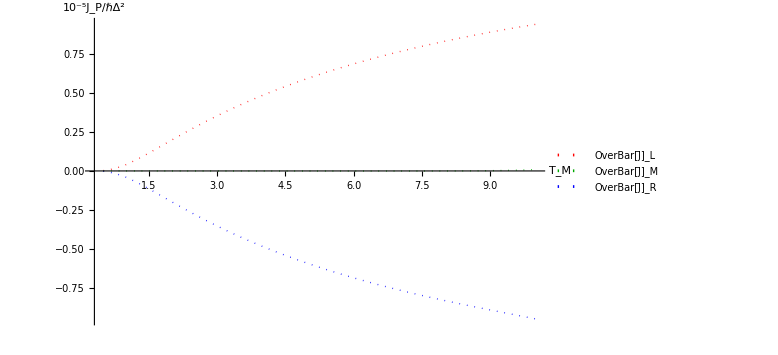

```mathematica
J3=OverBar[PlotEngyFlowsWithTM1][0.5,10,0.25,10,0.2 ,1,2,3,20,20,Full]
```

Thermal flows with and without crossing dissipation in same plot

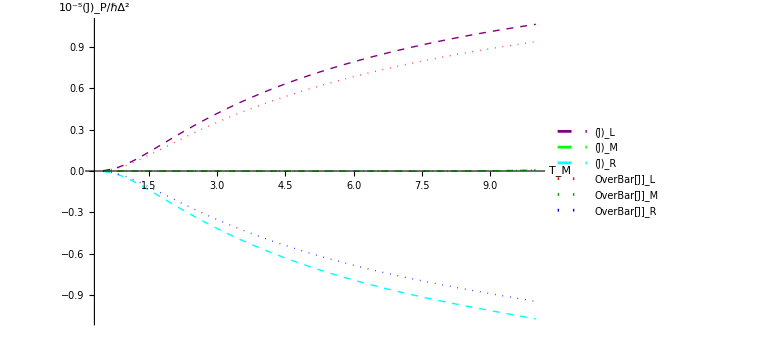

```mathematica
C1=Show[J2,J3]
```

```mathematica
Export["CrossDissipation.pdf",C1,"PDF","AllowRasterization"->False];
```

Percentage difference in energy flows

```mathematica
PlotPercentage[Tmin_,Tmax_,Tres_,TL_,TR_,ωL_,ωR_,ωM_,gs_,gMs_]:=
Module[{tempx,tempy1,tempy2,temp1,temp2,temp3,temp},
tempx=Table[{T,T,T},{T,Tmin,Tmax,Tres}];
tempy1=10^5 Table[OverBar[varEngyFunc][TL,TM,TR,ωL,ωR,ωM,gs,gMs,unitassum],{TM,Tmin,Tmax,Tres}];
tempy2=10^5 Table[OverBar[varEngyFunc1][TL,TM,TR,ωL,ωR,ωM,gs,gMs,unitassum],{TM,Tmin,Tmax,Tres}];
temp1= Table[{(tempy1[[i,;;]][[1]]-tempy2[[i,;;]][[1]])/(tempy1[[i,;;]][[1]])×100},{i,1,Length[tempx]}];
temp2= Table[{(tempy1[[i,;;]][[2]]-tempy2[[i,;;]][[2]])/(tempy1[[i,;;]][[2]])×100},{i,1,Length[tempx]}];
temp3= Table[{(tempy1[[i,;;]][[3]]-tempy2[[i,;;]][[3]])/(tempy1[[i,;;]][[3]])×100},{i,1,Length[tempx]}];
temp=Table[{MapThread[List,{tempx[[;;,1]],temp1[[;;,1]]}],MapThread[List,{tempx[[;;,1]],temp3[[;;,1]]}]}];
ListPlot[temp,AxesStyle->Directive[Black,19.5,FontFamily->"Times New Roman"],AxesLabel->{Style["T_M",19.5,FontFamily->"Times New Roman"],Style["Δ %",19.5,FontFamily->"Times New Roman"]},Joined->True,PlotStyle->{Red,Blue},LabelStyle->Directive[FontFamily->"Times New Roman",FontSize->19.5],ImageSize->Large]
]
```

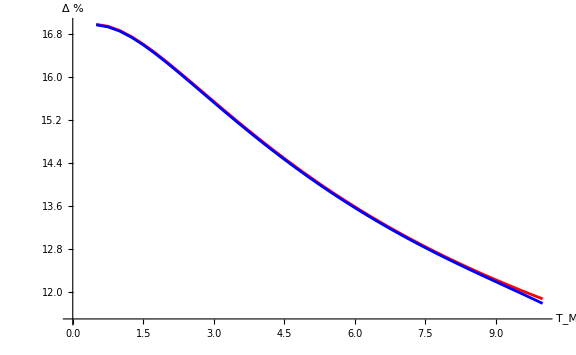

```mathematica
D1=PlotPercentage[0.5,10,0.25,10,0.2 ,1,2,3,20,20]
```

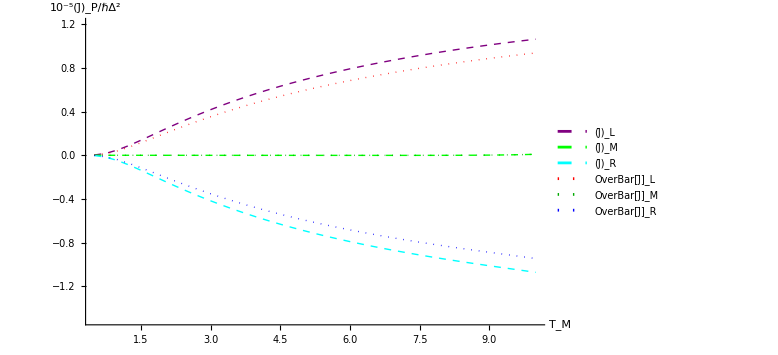

```mathematica
Show[C1,PlotRange->{Automatic,{-1.5,1.2}},Epilog->{Inset[Show[D1,Axes->True,AxesStyle->Gray, LabelStyle->Directive[15],AxesLabel->{Style["T_M",17,FontFamily->"Times New Roman",FontColor->Gray],Style["Δ(%)",17,FontFamily->"Times New Roman",FontColor->Gray]}],Scaled[{0.32,0.25}],Center,Scaled[0.5]]},ImageSize->Large]
```